# Liver slices MFA

Model fitting to data from donors 5,8,10,16,20

This version adds an unlabeled acetate source to represent fatty acid oxidation

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
<<NilssonLab`NetworkLayout`
<<NilssonLab`OpenFLUX`
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\code\liver-flux-analysis\flux-analysis-liver

```mathematica
liverProjectPath="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo";
```

## Functions

### EMU mixtures

Recover fitted MIDs as mixing x target MIDs

```mathematica
MixTargetMIDs[emuMixing_,targetMIDs_]:=
Block[{ix},
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.targetMIDs⟦ix⟧,
{em,emuMixing}]]
```

### Random flux states

Generating random flux states from the min/max vectors, scaled to output = 100.
We always include a small component of the mean vectors to avoid zeros.

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Isotope correction

The matrix T_n for an n-carbon MID. An observed MID x is related to a corrected MID y at x=T_n y

```mathematica
CorrectionMatrix[n_,p_]:=
Transpose[Table[
Join[Table[0,{i}],PDF[BinomialDistribution[n-i,p],Range[0,n-i]]],
{i,0,n}]]
```

```mathematica
IsotopeCorrect[x_?VectorQ,p_]:=
LinearSolve[CorrectionMatrix[Length[x]-1,p],x]
```

```mathematica
IsotopeCorrect[x_?VectorQ]:=IsotopeCorrect[x,0.0106]
```

For an incomplete MID vector, assuming remaining elelments are zero

```mathematica
IsotopeCorrect[x_?VectorQ,n_Integer]:=
Take[
LinearSolve[CorrectionMatrix[n,0.0106],PadRight[x,n+1]],
Length[x]]
```

### Q-Q plots

```mathematica
QQData[q:{_Real..},opts:OptionsPattern[]]:=
Block[{n,ix,q0},
n=Length[q];
ix=Ordering[q];
q0=Quantile[NormalDistribution[0,1],N[(Range[n]-1/2)/n]];
Transpose[{q⟦ix⟧,q0}]]
```

```mathematica
QQPlot[q:{_Real..},opts:OptionsPattern[]]:=
ListPlot[QQData[q],opts]
```

```mathematica
QQPlot[q:{_Real..},labels:{_String..},opts:OptionsPattern[]]:=
Block[{n,ix,q0},
n=Length[q];
ix=Ordering[q];
q0=Quantile[NormalDistribution[0,1],N[(Range[n]-1/2)/n]];
ListPlot[Thread[Tooltip[Transpose[{q⟦ix⟧,q0}],labels⟦ix⟧]],opts]]
```

## Import model

```mathematica
modelDir="C:\\code\\liver-flux-models\\Models\\liver-model-fatty-acids-2";
```

```mathematica
modelId="liver-model-fatty-acids-2";
```

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
{net,atomMaps,targets}=OpenFLUXImport[FileNameJoin[{modelDir,modelId<>".txt"}]];
```

```mathematica
TableForm[Table[{ReactionID[r],ReactionFormula[net,r]},{r,Reactions[net]}],TableHeadings->{Automatic,None}]
```

1 | 2AMACHYD | 2amac_c + h2o_c ==> nh4_c + pyr_c
2 | ACONTm | cit_m <=> icit_m
3 | ADK1 | amp_c + atp_c ==> 2 adp_c
4 | AKGDm | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
5 | AKGtm | akg_c <=> akg_m
6 | ALATA_L | akg_c + ala-L_c <=> glu-L_c + pyr_c
7 | ALAmix | ala-L_v ==> ala-L_e
8 | ALAtl | ala-L_l ==> ala-L_c
9 | ALAtin | ala-L_v ==> ala-L_c
10 | ALAtout | ala-L_c ==> ala-L_e
11 | ARGN | arg-L_c + h2o_c ==> orn_c + urea_c
12 | ARGSL | argsuc_c ==> arg-L_c + fum_c
13 | ARGSS | asp-L_c + atp_c + citr-L_c ==> amp_c + argsuc_c + h_c + ppi_c
14 | ARGmix | arg-L_v ==> arg-L_e
15 | ARGtl | arg-L_l ==> arg-L_c
16 | ARGtin | arg-L_v ==> arg-L_c
17 | ARGtout | arg-L_c ==> arg-L_e
18 | ASPTA | akg_c + asp-L_c <=> glu-L_c + oaa_c
19 | ASPTAm | glu-L_m + oaa_m <=> akg_m + asp-L_m
20 | ASPtl | asp-L_l ==> asp-L_c
21 | ASPmix | asp-L_v ==> asp-L_e
22 | ASPtin | asp-L_v ==> asp-L_c
23 | ASPtout | asp-L_c ==> asp-L_e
24 | ASPtm | asp-L_m <=> asp-L_c
25 | ATPS4m | adp_m + 4 h_ims_m + pi_m ==> atp_m + h2o_m + 3 h_m
26 | ATPtm | adp_c + atp_m <=> adp_m + atp_c
27 | CBPSam | 2 atp_m + hco3_m + nh4_m ==> 2 adp_m + cbp_m + 2 h_m + pi_m
28 | ATPASES | atp_c + h2o_c ==> adp_c + h_c + pi_c
29 | CO2tm | co2_c <=> co2_m
30 | CSm | accoa_m + h2o_m + oaa_m ==> cit_m + coa_m + h_m
31 | CYOOm | 4 focytC_m + 8 h_m + o2_m ==> 4 ficytC_m + 2 h2o_m + 4 h_ims_m
32 | CYOR-u10m | 2 ficytC_m + 2 h_m + q10h2_m ==> 2 focytC_m + 4 h_ims_m + q10_m
33 | ENO | 2pg_c <=> h2o_c + pep_c
34 | ETF | fadh2_m + q10_m ==> fad_m + q10h2_m
35 | FAO16 | coa_m + fad_m + h2o_m + nad_m + pmtcoa_m ==> accoa_m + fadh2_m + h_m + nadh_m + tdcoa_m
36 | FAO14 | coa_m + fad_m + h2o_m + nad_m + tdcoa_m ==> accoa_m + ddcacoa_m + fadh2_m + h_m + nadh_m
37 | FAO12 | coa_m + ddcacoa_m + fad_m + h2o_m + nad_m ==> accoa_m + dcacoa_m + fadh2_m + h_m + nadh_m
38 | FAO10 | coa_m + dcacoa_m + fad_m + h2o_m + nad_m ==> accoa_m + fadh2_m + h_m + nadh_m + occoa_m
39 | FAO8 | coa_m + fad_m + h2o_m + nad_m + occoa_m ==> accoa_m + fadh2_m + hexcoa_m + h_m + nadh_m
40 | FAO6 | coa_m + fad_m + h2o_m + hexcoa_m + nad_m ==> accoa_m + btcoa_m + fadh2_m + h_m + nadh_m
41 | FAO4 | btcoa_m + coa_m + fad_m + h2o_m + nad_m ==> 2 accoa_m + fadh2_m + h_m + nadh_m
42 | FBA | fdp_c <=> dhap_c + g3p_c
43 | FBP | fdp_c + h2o_c ==> f6p_c + pi_c
44 | FUMm | fum_m + h2o_m ==> mal-L_m
45 | FUMtm | fum_c ==> fum_m
46 | G3PD1 | dhap_c + h_c + nadh_c ==> glyc3p_c + nad_c
47 | G5SDxm | glu5sa_m + h2o_m + nad_m ==> glu-L_m + 2 h_m + nadh_m
48 | G6PDH2r | g6p_c + nadp_c ==> 6pgl_c + h_c + nadph_c
49 | G6PPer | g6p_r + h2o_r ==> glc-D_r + pi_r
50 | G6Pter | g6p_c <=> g6p_r
51 | GAPD | g3p_c + nad_c + pi_c <=> 13dpg_c + h_c + nadh_c
52 | GHMT2r | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c
53 | GLCmix | glc-D_v ==> glc-D_e
54 | GLCtin | glc-D_v ==> glc-D_c
55 | GLCtout | glc-D_r ==> glc-D_e
56 | GLNmix | gln-L_v ==> gln-L_e
57 | GLNtin | gln-L_v ==> gln-L_c
58 | GLNtl | gln-L_l ==> gln-L_c
59 | GLNtout | gln-L_c ==> gln-L_e
60 | GLNtm | gln-L_c <=> gln-L_m
61 | GLNS | atp_c + glu-L_c + nh4_c ==> adp_c + gln-L_c + h_c + pi_c
62 | GLUDxm | glu-L_m + h2o_m + nad_m <=> akg_m + h_m + nadh_m + nh4_m
63 | GLUNm | gln-L_m + h2o_m ==> glu-L_m + nh4_m
64 | GLUtl | glu-L_l ==> glu-L_c
65 | GLUt2m | glu-L_c <=> glu-L_m
66 | GLUmix | glu-L_v ==> glu-L_e
67 | GLUtin | glu-L_v ==> glu-L_c
68 | GLUtout | glu-L_c ==> glu-L_e
69 | GLYtl | gly_l ==> gly_c
70 | GLYmix | gly_v ==> gly_e
71 | GLYtin | gly_v ==> gly_c
72 | GLYtout | gly_c ==> gly_e
73 | GLYCOGEN_BREAK | glycogen_c + pi_c ==> g1p_c
74 | GLYCPH | glyc3p_c + h2o_c ==> glyc_c + pi_c
75 | GND | 6pgc_c + nadp_c ==> co2_c + nadph_c + ru5p-D_c
76 | H2Oter | h2o_c ==> h2o_r
77 | H2Otm | h2o_c <=> h2o_m
78 | HCO3Em | co2_m + h2o_m ==> hco3_m + h_m
79 | HEX1 | atp_c + glc-D_c ==> adp_c + g6p_c + h_c
80 | Htm2 | h_m <=> h_c
81 | ICDHxm | icit_m + nad_m <=> akg_m + co2_m + nadh_m
82 | LDH_L | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
83 | MALtm | mal-L_c <=> mal-L_m
84 | MDH | mal-L_c + nad_c <=> h_c + nadh_c + oaa_c
85 | MDHm | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
86 | NADH2-u10m | 5 h_m + nadh_m + q10_m ==> 4 h_ims_m + nad_m + q10h2_m
87 | NADPH_REDOX | 2 nadph_c + o2_c ==> h2o_c + 2 nadp_c
88 | NDPK1 | atp_c + gdp_c ==> adp_c + gtp_c
89 | NH4tm | nh4_c <=> nh4_m
90 | O2tm | o2_c ==> o2_m
91 | ORNTArm | akg_m + orn_m ==> glu5sa_m + glu-L_m
92 | OCBTm | cbp_m + orn_m ==> citr-L_m + h_m + pi_m
93 | ORNtm | orn_c ==> orn_m
94 | ORNt4m | citr-L_m + orn_c ==> citr-L_c + orn_m
95 | PCm | atp_m + hco3_m + pyr_m ==> adp_m + h_m + oaa_m + pi_m
96 | PDHm | coa_m + nad_m + pyr_m ==> accoa_m + co2_m + nadh_m
97 | PEPCK | gtp_c + oaa_c ==> co2_c + gdp_c + pep_c
98 | PFK | atp_c + f6p_c ==> adp_c + fdp_c + h_c
99 | PGCD | 3pg_c + nad_c ==> 3php_c + h_c + nadh_c
100 | PGI | g6p_c <=> f6p_c
101 | PGK | 13dpg_c + adp_c <=> 3pg_c + atp_c
102 | PGL | 6pgl_c + h2o_c ==> 6pgc_c + h_c
103 | PGM | 3pg_c <=> 2pg_c
104 | PGMT | g1p_c ==> g6p_c
105 | PIt2m | pi_c ==> pi_m
106 | PIter | pi_r ==> pi_c
107 | PPA | h2o_c + ppi_c ==> h_c + 2 pi_c
108 | PMTtm | pmt_c ==> pmt_m
109 | PMTCOAT | coa_m + pmt_m ==> pmtcoa_m
110 | PROTDEG_ALA | prot_ala_l ==> ala-L_l
111 | PROTDEG_ARG | prot_arg_l ==> arg-L_l
112 | PROTDEG_ASP | prot_asp_l ==> asp-L_l
113 | PROTDEG_GLN | prot_gln_l ==> gln-L_l
114 | PROTDEG_GLU | prot_glu_l ==> glu-L_l
115 | PROTDEG_GLY | prot_gly_l ==> gly_l
116 | PROTDEG_SER | prot_ser_l ==> ser-L_l
117 | PROTSYN_ALA | ala-L_c ==> prot_ala_c
118 | PROTSYN_ARG | arg-L_c ==> prot_arg_c
119 | PROTSYN_ASP | asp-L_c ==> prot_asp_c
120 | PROTSYN_GLN | gln-L_c ==> prot_gln_c
121 | PROTSYN_GLU | glu-L_c ==> prot_glu_c
122 | PROTSYN_GLY | gly_c ==> prot_gly_c
123 | PROTSYN_SER | ser-L_c ==> prot_ser_c
124 | PROTSYN_ATP | 4 atp_c + 4 h2o_c ==> 4 adp_c + 4 h_c + 4 pi_c
125 | PSERT | 3php_c + glu-L_c ==> akg_c + pser-L_c
126 | PSP_L | h2o_c + pser-L_c ==> pi_c + ser-L_c
127 | PYK | adp_c + h_c + pep_c ==> atp_c + pyr_c
128 | PYRt2m | pyr_c <=> pyr_m
129 | RPE | ru5p-D_c ==> xu5p-D_c
130 | RPI | ru5p-D_c ==> r5p_c
131 | SERHL | ser-L_c ==> 2amac_c + h2o_c
132 | SERmix | ser-L_v ==> ser-L_e
133 | SERtl | ser-L_l ==> ser-L_c
134 | SERtin | ser-L_v ==> ser-L_c
135 | SERtout | ser-L_c ==> ser-L_e
136 | SUCD1m | q10_m + succ_m ==> fum_m + q10h2_m
137 | SUCOASm | adp_m + pi_m + succoa_m ==> atp_m + coa_m + succ_m
138 | TALA | g3p_c + s7p_c ==> e4p_c + f6p_c
139 | TKT1 | r5p_c + xu5p-D_c ==> g3p_c + s7p_c
140 | TKT2 | e4p_c + xu5p-D_c ==> f6p_c + g3p_c
141 | TPI | dhap_c <=> g3p_c

```mathematica
Length[Metabolites[net]]
```

145

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 48 boundary fluxes>

```mathematica
BoundaryFluxNames[bnet]
```

{ala-L_IN,arg-L_IN,asp-L_IN,co2_IN,glc-D_IN,gln-L_IN,glu-L_IN,glycogen_IN,gly_IN,h2o_IN,h_IN,mlthf_IN,nh4_IN,o2_IN,pmt_IN,prot_ala_IN,prot_arg_IN,prot_asp_IN,prot_gln_IN,prot_glu_IN,prot_gly_IN,prot_ser_IN,ser-L_IN,thf_IN,ala-L_OUT,arg-L_OUT,asp-L_OUT,co2_OUT,glc-D_OUT,gln-L_OUT,glu-L_OUT,glyc_OUT,gly_OUT,h2o_OUT,h_OUT,lac-L_OUT,mlthf_OUT,nh4_OUT,prot_ala_OUT,prot_arg_OUT,prot_asp_OUT,prot_gln_OUT,prot_glu_OUT,prot_gly_OUT,prot_ser_OUT,ser-L_OUT,thf_OUT,urea_OUT}

#### Fix the atom map for FAO4

Currently OpenFLUXImport doesn’t handle stoichiometries > 1 for metabolites with mapped atoms

```mathematica
Block[{i},
i=Position[ReactionID/@Reactions[net],"FAO4"]⟦1,1⟧;
atomMaps⟦i,2⟧=Join[atomMaps⟦i,2⟧,atomMaps⟦i,2⟧/.{a_Atom,1}->{a,2}]];
```

```mathematica
Block[{i},
i=Position[ReactionID/@Reactions[net],"FAO4"]⟦1,1⟧;
Transpose[{EductList[atomMaps⟦i⟧],ProductList[atomMaps⟦i⟧]}]//TableForm]
```

<btcoa_m(C1)>
1 | <accoa_m(C1)>
1
<btcoa_m(C2)>
1 | <accoa_m(C2)>
1
<btcoa_m(C3)>
1 | <accoa_m(C1)>
2
<btcoa_m(C4)>
1 | <accoa_m(C2)>
2

### Substrate distributions

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID[FileNameJoin[{modelDir,"substrate-distributions.txt"}]]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.99}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.99}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.99}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.99}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.99}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.99}],glu-L_i→NaturalIsotopomerDistribution[{5},{0.99}],gly_i→NaturalIsotopomerDistribution[{2},{0.99}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],mlthf_i→NaturalIsotopomerDistribution[{1},{0.0107}],pmt_i→NaturalIsotopomerDistribution[{16},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_asp_i→NaturalIsotopomerDistribution[{4},{0.0107}],prot_gln_i→NaturalIsotopomerDistribution[{5},{0.0107}],prot_glu_i→NaturalIsotopomerDistribution[{5},{0.0107}],prot_gly_i→NaturalIsotopomerDistribution[{2},{0.0107}],prot_ser_i→NaturalIsotopomerDistribution[{3},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.99}],thf_i→NaturalIsotopomerDistribution[{1},{0.0107}]}

### Check atom map

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMaps]
```

{}

```mathematica
Block[{i},
i=Position[ReactionID/@Reactions[net],"FAO4"]⟦1,1⟧;
Transpose[{First/@EductList[atomMaps⟦i⟧],First/@ProductList[atomMaps⟦i⟧]}]//TableForm]
```

<btcoa_m(C1)> | <accoa_m(C1)>
<btcoa_m(C2)> | <accoa_m(C2)>
<btcoa_m(C3)> | <accoa_m(C1)>
<btcoa_m(C4)> | <accoa_m(C2)>

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmaps=BoundaryAtomMaps[net,atomMaps];
bmaps//Length
```

48

#### Visualizations

```mathematica
atomGraph=AdjacencyGraph[
AtomList[atomMaps],
AtomToAtomAdjacencyMatrix[net,atomMaps]]
```

Thread::tdlen: Objects of unequal length in {{<btcoa_m(C1)>,<btcoa_m(C2)>,<btcoa_m(C3)>,<btcoa_m(C4)>},{<accoa_m(C1)>,<accoa_m(C2)>}} cannot be combined.

SparseArray::posd: The left-hand side of {106,107,108,109}→1 in {{4,461}→1,{5,462}→1,{6,463}→1,{111,307}→1,{112,310}→1,{113,309}→1,{114,312}→1,{115,311}→1,{116,308}→1,{307,111}→1,{310,112}→1,{309,113}→1,{312,114}→1,{311,115}→1,{308,116}→1,{35,501}→1,{36,500}→1,{37,503}→1,{38,502}→1,{39,130}→1,{501,35}→1,{500,36}→1,«8»,{35,30}→1,{36,31}→1,{37,32}→1,{38,33}→1,{39,34}→1,{30,255}→1,{31,256}→1,{32,257}→1,{33,258}→1,{34,259}→1,{40,461}→1,{41,462}→1,{42,463}→1,{255,30}→1,{256,31}→1,{257,32}→1,{258,33}→1,{259,34}→1,{461,40}→1,{462,41}→1,«710»} is not a position or a pattern that will match the position of an element in an array with dimensions {523,523}.

AdjacencyGraph::matsq: Argument SparseArray[{{4,461}→1,{5,462}→1,{6,463}→1,{111,307}→1,{112,310}→1,{113,309}→1,{114,312}→1,{115,311}→1,{116,308}→1,{307,111}→1,{310,112}→1,{309,113}→1,{312,114}→1,{311,115}→1,{308,116}→1,{35,501}→1,{36,500}→1,{37,503}→1,{38,502}→1,{39,130}→1,{501,35}→1,«9»,{35,30}→1,{36,31}→1,{37,32}→1,{38,33}→1,{39,34}→1,{30,255}→1,{31,256}→1,{32,257}→1,{33,258}→1,{34,259}→1,{40,461}→1,{41,462}→1,{42,463}→1,{255,30}→1,{256,31}→1,{257,32}→1,{258,33}→1,{259,34}→1,{461,40}→1,{462,41}→1,«710»},{«1»}] at position 2 is not a non-empty square matrix.

AdjacencyGraph[{<13dpg_c(C1)>,<13dpg_c(C2)>,<13dpg_c(C3)>,<2amac_c(C1)>,<2amac_c(C2)>,<2amac_c(C3)>,<2pg_c(C1)>,<2pg_c(C2)>,<2pg_c(C3)>,<3pg_c(C1)>,<3pg_c(C2)>,<3pg_c(C3)>,<3php_c(C1)>,<3php_c(C2)>,<3php_c(C3)>,<6pgc_c(C1)>,<6pgc_c(C2)>,<6pgc_c(C3)>,<6pgc_c(C4)>,<6pgc_c(C5)>,<6pgc_c(C6)>,<6pgl_c(C1)>,<6pgl_c(C2)>,<6pgl_c(C3)>,<6pgl_c(C4)>,<6pgl_c(C5)>,<6pgl_c(C6)>,<accoa_m(C1)>,<accoa_m(C2)>,<akg_c(C1)>,<akg_c(C2)>,<akg_c(C3)>,<akg_c(C4)>,<akg_c(C5)>,<akg_m(C1)>,<akg_m(C2)>,<akg_m(C3)>,<akg_m(C4)>,<akg_m(C5)>,<ala-L_c(C1)>,<ala-L_c(C2)>,<ala-L_c(C3)>,<ala-L_e(C1)>,<ala-L_e(C2)>,<ala-L_e(C3)>,<ala-L_l(C1)>,<ala-L_l(C2)>,<ala-L_l(C3)>,<ala-L_v(C1)>,<ala-L_v(C2)>,<ala-L_v(C3)>,<arg-L_c(C1)>,<arg-L_c(C2)>,<arg-L_c(C3)>,<arg-L_c(C4)>,<arg-L_c(C5)>,<arg-L_c(C6)>,<arg-L_e(C1)>,<arg-L_e(C2)>,<arg-L_e(C3)>,<arg-L_e(C4)>,<arg-L_e(C5)>,<arg-L_e(C6)>,<arg-L_l(C1)>,<arg-L_l(C2)>,<arg-L_l(C3)>,<arg-L_l(C4)>,<arg-L_l(C5)>,<arg-L_l(C6)>,<arg-L_v(C1)>,<arg-L_v(C2)>,<arg-L_v(C3)>,<arg-L_v(C4)>,<arg-L_v(C5)>,<arg-L_v(C6)>,<argsuc_c(C1)>,<argsuc_c(C2)>,<argsuc_c(C3)>,<argsuc_c(C4)>,<argsuc_c(C5)>,<argsuc_c(C6)>,<argsuc_c(C7)>,<argsuc_c(C8)>,<argsuc_c(C9)>,<argsuc_c(C10)>,<asp-L_c(C1)>,<asp-L_c(C2)>,<asp-L_c(C3)>,<asp-L_c(C4)>,<asp-L_e(C1)>,<asp-L_e(C2)>,<asp-L_e(C3)>,<asp-L_e(C4)>,<asp-L_l(C1)>,<asp-L_l(C2)>,<asp-L_l(C3)>,<asp-L_l(C4)>,<asp-L_m(C1)>,<asp-L_m(C2)>,<asp-L_m(C3)>,<asp-L_m(C4)>,<asp-L_v(C1)>,<asp-L_v(C2)>,<asp-L_v(C3)>,<asp-L_v(C4)>,<btcoa_m(C1)>,<btcoa_m(C2)>,<btcoa_m(C3)>,<btcoa_m(C4)>,<cbp_m(C1)>,<cit_m(C1)>,<cit_m(C2)>,<cit_m(C3)>,<cit_m(C4)>,<cit_m(C5)>,<cit_m(C6)>,<citr-L_c(C1)>,<citr-L_c(C2)>,<citr-L_c(C3)>,<citr-L_c(C4)>,<citr-L_c(C5)>,<citr-L_c(C6)>,<citr-L_m(C1)>,<citr-L_m(C2)>,<citr-L_m(C3)>,<citr-L_m(C4)>,<citr-L_m(C5)>,<citr-L_m(C6)>,<co2_c(C1)>,<co2_m(C1)>,<dcacoa_m(C1)>,<dcacoa_m(C2)>,<dcacoa_m(C3)>,<dcacoa_m(C4)>,<dcacoa_m(C5)>,<dcacoa_m(C6)>,<dcacoa_m(C7)>,<dcacoa_m(C8)>,<dcacoa_m(C9)>,<dcacoa_m(C10)>,<ddcacoa_m(C1)>,<ddcacoa_m(C2)>,<ddcacoa_m(C3)>,<ddcacoa_m(C4)>,<ddcacoa_m(C5)>,<ddcacoa_m(C6)>,<ddcacoa_m(C7)>,<ddcacoa_m(C8)>,<ddcacoa_m(C9)>,<ddcacoa_m(C10)>,<ddcacoa_m(C11)>,<ddcacoa_m(C12)>,<dhap_c(C1)>,<dhap_c(C2)>,<dhap_c(C3)>,<e4p_c(C1)>,<e4p_c(C2)>,<e4p_c(C3)>,<e4p_c(C4)>,<f6p_c(C1)>,<f6p_c(C2)>,<f6p_c(C3)>,<f6p_c(C4)>,<f6p_c(C5)>,<f6p_c(C6)>,<fdp_c(C1)>,<fdp_c(C2)>,<fdp_c(C3)>,<fdp_c(C4)>,<fdp_c(C5)>,<fdp_c(C6)>,<fum_c(C1)>,<fum_c(C2)>,<fum_c(C3)>,<fum_c(C4)>,<fum_m(C1)>,<fum_m(C2)>,<fum_m(C3)>,<fum_m(C4)>,<g1p_c(C1)>,<g1p_c(C2)>,<g1p_c(C3)>,<g1p_c(C4)>,<g1p_c(C5)>,<g1p_c(C6)>,<g3p_c(C1)>,<g3p_c(C2)>,<g3p_c(C3)>,<g6p_c(C1)>,<g6p_c(C2)>,<g6p_c(C3)>,<g6p_c(C4)>,<g6p_c(C5)>,<g6p_c(C6)>,<g6p_r(C1)>,<g6p_r(C2)>,<g6p_r(C3)>,<g6p_r(C4)>,<g6p_r(C5)>,<g6p_r(C6)>,<glc-D_c(C1)>,<glc-D_c(C2)>,<glc-D_c(C3)>,<glc-D_c(C4)>,<glc-D_c(C5)>,<glc-D_c(C6)>,<glc-D_r(C1)>,<glc-D_r(C2)>,<glc-D_r(C3)>,<glc-D_r(C4)>,<glc-D_r(C5)>,<glc-D_r(C6)>,<glc-D_e(C1)>,<glc-D_e(C2)>,<glc-D_e(C3)>,<glc-D_e(C4)>,<glc-D_e(C5)>,<glc-D_e(C6)>,<glc-D_v(C1)>,<glc-D_v(C2)>,<glc-D_v(C3)>,<glc-D_v(C4)>,<glc-D_v(C5)>,<glc-D_v(C6)>,<gln-L_c(C1)>,<gln-L_c(C2)>,<gln-L_c(C3)>,<gln-L_c(C4)>,<gln-L_c(C5)>,<gln-L_e(C1)>,<gln-L_e(C2)>,<gln-L_e(C3)>,<gln-L_e(C4)>,<gln-L_e(C5)>,<gln-L_l(C1)>,<gln-L_l(C2)>,<gln-L_l(C3)>,<gln-L_l(C4)>,<gln-L_l(C5)>,<gln-L_m(C1)>,<gln-L_m(C2)>,<gln-L_m(C3)>,<gln-L_m(C4)>,<gln-L_m(C5)>,<gln-L_v(C1)>,<gln-L_v(C2)>,<gln-L_v(C3)>,<gln-L_v(C4)>,<gln-L_v(C5)>,<glu5sa_m(C1)>,<glu5sa_m(C2)>,<glu5sa_m(C3)>,<glu5sa_m(C4)>,<glu5sa_m(C5)>,<glu-L_c(C1)>,<glu-L_c(C2)>,<glu-L_c(C3)>,<glu-L_c(C4)>,<glu-L_c(C5)>,<glu-L_e(C1)>,<glu-L_e(C2)>,<glu-L_e(C3)>,<glu-L_e(C4)>,<glu-L_e(C5)>,<glu-L_l(C1)>,<glu-L_l(C2)>,<glu-L_l(C3)>,<glu-L_l(C4)>,<glu-L_l(C5)>,<glu-L_m(C1)>,<glu-L_m(C2)>,<glu-L_m(C3)>,<glu-L_m(C4)>,<glu-L_m(C5)>,<glu-L_v(C1)>,<glu-L_v(C2)>,<glu-L_v(C3)>,<glu-L_v(C4)>,<glu-L_v(C5)>,<gly_c(C1)>,<gly_c(C2)>,<gly_e(C1)>,<gly_e(C2)>,<gly_l(C1)>,<gly_l(C2)>,<gly_v(C1)>,<gly_v(C2)>,<glyc_c(C1)>,<glyc_c(C2)>,<glyc_c(C3)>,<glyc3p_c(C1)>,<glyc3p_c(C2)>,<glyc3p_c(C3)>,<glycogen_c(C1)>,<glycogen_c(C2)>,<glycogen_c(C3)>,<glycogen_c(C4)>,<glycogen_c(C5)>,<glycogen_c(C6)>,<hco3_m(C1)>,<hexcoa_m(C1)>,<hexcoa_m(C2)>,<hexcoa_m(C3)>,<hexcoa_m(C4)>,<hexcoa_m(C5)>,<hexcoa_m(C6)>,<icit_m(C1)>,<icit_m(C2)>,<icit_m(C3)>,<icit_m(C4)>,<icit_m(C5)>,<icit_m(C6)>,<lac-L_c(C1)>,<lac-L_c(C2)>,<lac-L_c(C3)>,<mal-L_c(C1)>,<mal-L_c(C2)>,<mal-L_c(C3)>,<mal-L_c(C4)>,<mal-L_m(C1)>,<mal-L_m(C2)>,<mal-L_m(C3)>,<mal-L_m(C4)>,<mlthf_c(C1)>,<oaa_c(C1)>,<oaa_c(C2)>,<oaa_c(C3)>,<oaa_c(C4)>,<oaa_m(C1)>,<oaa_m(C2)>,<oaa_m(C3)>,<oaa_m(C4)>,<occoa_m(C1)>,<occoa_m(C2)>,<occoa_m(C3)>,<occoa_m(C4)>,<occoa_m(C5)>,<occoa_m(C6)>,<occoa_m(C7)>,<occoa_m(C8)>,<orn_c(C1)>,<orn_c(C2)>,<orn_c(C3)>,<orn_c(C4)>,<orn_c(C5)>,<orn_m(C1)>,<orn_m(C2)>,<orn_m(C3)>,<orn_m(C4)>,<orn_m(C5)>,<pep_c(C1)>,<pep_c(C2)>,<pep_c(C3)>,<pmt_c(C1)>,<pmt_c(C2)>,<pmt_c(C3)>,<pmt_c(C4)>,<pmt_c(C5)>,<pmt_c(C6)>,<pmt_c(C7)>,<pmt_c(C8)>,<pmt_c(C9)>,<pmt_c(C10)>,<pmt_c(C11)>,<pmt_c(C12)>,<pmt_c(C13)>,<pmt_c(C14)>,<pmt_c(C15)>,<pmt_c(C16)>,<pmt_m(C1)>,<pmt_m(C2)>,<pmt_m(C3)>,<pmt_m(C4)>,<pmt_m(C5)>,<pmt_m(C6)>,<pmt_m(C7)>,<pmt_m(C8)>,<pmt_m(C9)>,<pmt_m(C10)>,<pmt_m(C11)>,<pmt_m(C12)>,<pmt_m(C13)>,<pmt_m(C14)>,<pmt_m(C15)>,<pmt_m(C16)>,<pmtcoa_m(C1)>,<pmtcoa_m(C2)>,<pmtcoa_m(C3)>,<pmtcoa_m(C4)>,<pmtcoa_m(C5)>,<pmtcoa_m(C6)>,<pmtcoa_m(C7)>,<pmtcoa_m(C8)>,<pmtcoa_m(C9)>,<pmtcoa_m(C10)>,<pmtcoa_m(C11)>,<pmtcoa_m(C12)>,<pmtcoa_m(C13)>,<pmtcoa_m(C14)>,<pmtcoa_m(C15)>,<pmtcoa_m(C16)>,<prot_ala_c(C1)>,<prot_ala_c(C2)>,<prot_ala_c(C3)>,<prot_ala_l(C1)>,<prot_ala_l(C2)>,<prot_ala_l(C3)>,<prot_arg_c(C1)>,<prot_arg_c(C2)>,<prot_arg_c(C3)>,<prot_arg_c(C4)>,<prot_arg_c(C5)>,<prot_arg_c(C6)>,<prot_arg_l(C1)>,<prot_arg_l(C2)>,<prot_arg_l(C3)>,<prot_arg_l(C4)>,<prot_arg_l(C5)>,<prot_arg_l(C6)>,<prot_asp_c(C1)>,<prot_asp_c(C2)>,<prot_asp_c(C3)>,<prot_asp_c(C4)>,<prot_asp_l(C1)>,<prot_asp_l(C2)>,<prot_asp_l(C3)>,<prot_asp_l(C4)>,<prot_gln_c(C1)>,<prot_gln_c(C2)>,<prot_gln_c(C3)>,<prot_gln_c(C4)>,<prot_gln_c(C5)>,<prot_gln_l(C1)>,<prot_gln_l(C2)>,<prot_gln_l(C3)>,<prot_gln_l(C4)>,<prot_gln_l(C5)>,<prot_glu_c(C1)>,<prot_glu_c(C2)>,<prot_glu_c(C3)>,<prot_glu_c(C4)>,<prot_glu_c(C5)>,<prot_glu_l(C1)>,<prot_glu_l(C2)>,<prot_glu_l(C3)>,<prot_glu_l(C4)>,<prot_glu_l(C5)>,<prot_gly_c(C1)>,<prot_gly_c(C2)>,<prot_gly_l(C1)>,<prot_gly_l(C2)>,<prot_ser_c(C1)>,<prot_ser_c(C2)>,<prot_ser_c(C3)>,<prot_ser_l(C1)>,<prot_ser_l(C2)>,<prot_ser_l(C3)>,<pser-L_c(C1)>,<pser-L_c(C2)>,<pser-L_c(C3)>,<pyr_c(C1)>,<pyr_c(C2)>,<pyr_c(C3)>,<pyr_m(C1)>,<pyr_m(C2)>,<pyr_m(C3)>,<r5p_c(C1)>,<r5p_c(C2)>,<r5p_c(C3)>,<r5p_c(C4)>,<r5p_c(C5)>,<ru5p-D_c(C1)>,<ru5p-D_c(C2)>,<ru5p-D_c(C3)>,<ru5p-D_c(C4)>,<ru5p-D_c(C5)>,<s7p_c(C1)>,<s7p_c(C2)>,<s7p_c(C3)>,<s7p_c(C4)>,<s7p_c(C5)>,<s7p_c(C6)>,<s7p_c(C7)>,<ser-L_c(C1)>,<ser-L_c(C2)>,<ser-L_c(C3)>,<ser-L_e(C1)>,<ser-L_e(C2)>,<ser-L_e(C3)>,<ser-L_l(C1)>,<ser-L_l(C2)>,<ser-L_l(C3)>,<ser-L_v(C1)>,<ser-L_v(C2)>,<ser-L_v(C3)>,<succ_m(C1)>,<succ_m(C2)>,<succ_m(C3)>,<succ_m(C4)>,<succoa_m(C1)>,<succoa_m(C2)>,<succoa_m(C3)>,<succoa_m(C4)>,<tdcoa_m(C1)>,<tdcoa_m(C2)>,<tdcoa_m(C3)>,<tdcoa_m(C4)>,<tdcoa_m(C5)>,<tdcoa_m(C6)>,<tdcoa_m(C7)>,<tdcoa_m(C8)>,<tdcoa_m(C9)>,<tdcoa_m(C10)>,<tdcoa_m(C11)>,<tdcoa_m(C12)>,<tdcoa_m(C13)>,<tdcoa_m(C14)>,<urea_c(C1)>,<xu5p-D_c(C1)>,<xu5p-D_c(C2)>,<xu5p-D_c(C3)>,<xu5p-D_c(C4)>,<xu5p-D_c(C5)>},SparseArray[{{4,461}→1,{5,462}→1,{6,463}→1,{111,307}→1,{112,310}→1,{113,309}→1,{114,312}→1,{115,311}→1,{116,308}→1,{307,111}→1,{310,112}→1,{309,113}→1,{312,114}→1,{311,115}→1,{308,116}→1,{35,501}→1,{36,500}→1,{37,503}→1,{38,502}→1,{39,130}→1,{501,35}→1,{500,36}→1,{503,37}→1,{502,38}→1,{130,39}→1,{30,35}→1,{31,36}→1,{32,37}→1,{33,38}→1,{34,39}→1,{35,30}→1,{36,31}→1,{37,32}→1,{38,33}→1,{39,34}→1,{30,255}→1,{31,256}→1,{32,257}→1,{33,258}→1,{34,259}→1,{40,461}→1,{41,462}→1,{42,463}→1,{255,30}→1,{256,31}→1,{257,32}→1,{258,33}→1,{259,34}→1,{461,40}→1,{462,41}→1,{463,42}→1,{49,43}→1,{50,44}→1,{51,45}→1,{46,40}→1,{47,41}→1,{48,42}→1,{49,40}→1,{50,41}→1,{51,42}→1,{40,43}→1,{41,44}→1,{42,45}→1,{52,341}→1,{53,342}→1,{54,343}→1,{55,344}→1,{56,345}→1,{57,518}→1,{76,52}→1,{77,53}→1,{78,54}→1,{79,172}→1,{80,55}→1,{81,173}→1,{82,174}→1,{83,56}→1,{84,175}→1,{85,57}→1,{86,79}→1,{87,81}→1,{88,82}→1,{89,84}→1,{117,76}→1,{118,77}→1,{119,78}→1,{120,80}→1,{121,83}→1,{122,85}→1,{70,58}→1,{71,59}→1,{72,60}→1,{73,61}→1,{74,62}→1,{75,63}→1,{64,52}→1,{65,53}→1,{66,54}→1,{67,55}→1,{68,56}→1,{69,57}→1,{70,52}→1,{71,53}→1,{72,54}→1,{73,55}→1,{74,56}→1,{75,57}→1,{52,58}→1,{53,59}→1,{54,60}→1,{55,61}→1,{56,62}→1,{57,63}→1,{30,255}→1,{31,256}→1,{32,257}→1,{33,258}→1,{34,259}→1,{86,325}→1,{87,326}→1,{88,327}→1,{89,328}→1,{255,30}→1,{256,31}→1,{257,32}→1,{258,33}→1,{259,34}→1,{325,86}→1,{326,87}→1,{327,88}→1,{328,89}→1,{270,35}→1,{271,36}→1,{272,37}→1,{273,38}→1,{274,39}→1,{329,98}→1,{330,99}→1,{331,100}→1,{332,101}→1,{35,270}→1,{36,271}→1,{37,272}→1,{38,273}→1,{39,274}→1,{98,329}→1,{99,330}→1,{100,331}→1,{101,332}→1,{94,86}→1,{95,87}→1,{96,88}→1,{97,89}→1,{102,90}→1,{103,91}→1,{104,92}→1,{105,93}→1,{102,86}→1,{103,87}→1,{104,88}→1,{105,89}→1,{86,90}→1,{87,91}→1,{88,92}→1,{89,93}→1,{98,86}→1,{99,87}→1,{100,88}→1,{101,89}→1,{86,98}→1,{87,99}→1,{88,100}→1,{89,101}→1,{300,110}→1,{129,130}→1,{130,129}→1,{28,112}→1,{29,114}→1,{329,111}→1,{330,116}→1,{331,113}→1,{332,115}→1,{7,351}→1,{8,352}→1,{9,353}→1,{351,7}→1,{352,8}→1,{353,9}→1,{386,504}→1,{387,505}→1,{388,506}→1,{389,507}→1,{390,508}→1,{391,509}→1,{392,510}→1,{393,511}→1,{394,512}→1,{395,513}→1,{396,514}→1,{397,515}→1,{398,516}→1,{399,517}→1,{400,28}→1,{401,29}→1,{504,141}→1,{505,142}→1,{506,143}→1,{507,144}→1,{508,145}→1,{509,146}→1,{510,147}→1,{511,148}→1,{512,149}→1,{513,150}→1,{514,151}→1,{515,152}→1,{516,28}→1,{517,29}→1,{141,131}→1,{142,132}→1,{143,133}→1,{144,134}→1,{145,135}→1,{146,136}→1,{147,137}→1,{148,138}→1,{149,139}→1,{150,140}→1,{151,28}→1,{152,29}→1,{131,333}→1,{132,334}→1,{133,335}→1,{134,336}→1,{135,337}→1,{136,338}→1,{137,339}→1,{138,340}→1,{139,28}→1,{140,29}→1,{333,301}→1,{334,302}→1,{335,303}→1,{336,304}→1,{337,305}→1,{338,306}→1,{339,28}→1,{340,29}→1,{301,106}→1,{302,107}→1,{303,108}→1,{304,109}→1,{305,28}→1,{306,29}→1,{106,107,108,109}→1,{28,29}→1,{166,187}→1,{167,154}→1,{168,188}→1,{169,186}→1,{170,153}→1,{171,155}→1,{187,166}→1,{154,167}→1,{188,168}→1,{186,169}→1,{153,170}→1,{155,171}→1,{166,160}→1,{167,161}→1,{168,162}→1,{169,163}→1,{170,164}→1,{171,165}→1,{176,320}→1,{177,321}→1,{178,322}→1,{179,323}→1,{172,176}→1,{173,177}→1,{174,178}→1,{175,179}→1,{153,291}→1,{154,292}→1,{155,293}→1,{250,270}→1,{251,271}→1,{252,272}→1,{253,273}→1,{254,274}→1,{189,22}→1,{190,23}→1,{191,24}→1,{192,25}→1,{193,26}→1,{194,27}→1,{195,207}→1,{196,208}→1,{197,209}→1,{198,210}→1,{199,211}→1,{200,212}→1,{189,195}→1,{190,196}→1,{191,197}→1,{192,198}→1,{193,199}→1,{194,200}→1,{195,189}→1,{196,190}→1,{197,191}→1,{198,192}→1,{199,193}→1,{200,194}→1,{186,3}→1,{187,1}→1,{188,2}→1,{3,186}→1,{1,187}→1,{2,188}→1,{484,324}→1,{485,280}→1,{486,281}→1,{324,484}→1,{280,485}→1,{281,486}→1,{219,213}→1,{220,214}→1,{221,215}→1,{222,216}→1,{223,217}→1,{224,218}→1,{219,201}→1,{220,202}→1,{221,203}→1,{222,204}→1,{223,205}→1,{224,206}→1,{207,213}→1,{208,214}→1,{209,215}→1,{210,216}→1,{211,217}→1,{212,218}→1,{245,230}→1,{246,231}→1,{247,232}→1,{248,233}→1,{249,234}→1,{245,225}→1,{246,226}→1,{247,227}→1,{248,228}→1,{249,229}→1,{235,225}→1,{236,226}→1,{237,227}→1,{238,228}→1,{239,229}→1,{225,230}→1,{226,231}→1,{227,232}→1,{228,233}→1,{229,234}→1,{225,240}→1,{226,241}→1,{227,242}→1,{228,243}→1,{229,244}→1,{240,225}→1,{241,226}→1,{242,227}→1,{243,228}→1,{244,229}→1,{255,225}→1,{256,226}→1,{257,227}→1,{258,228}→1,{259,229}→1,{270,35}→1,{271,36}→1,{272,37}→1,{273,38}→1,{274,39}→1,{35,270}→1,{36,271}→1,{37,272}→1,{38,273}→1,{39,274}→1,{240,270}→1,{241,271}→1,{242,272}→1,{243,273}→1,{244,274}→1,{265,255}→1,{266,256}→1,{267,257}→1,{268,258}→1,{269,259}→1,{255,270}→1,{256,271}→1,{257,272}→1,{258,273}→1,{259,274}→1,{270,255}→1,{271,256}→1,{272,257}→1,{273,258}→1,{274,259}→1,{275,260}→1,{276,261}→1,{277,262}→1,{278,263}→1,{279,264}→1,{275,255}→1,{276,256}→1,{277,257}→1,{278,258}→1,{279,259}→1,{255,260}→1,{256,261}→1,{257,262}→1,{258,263}→1,{259,264}→1,{284,280}→1,{285,281}→1,{286,282}→1,{287,283}→1,{286,280}→1,{287,281}→1,{280,282}→1,{281,283}→1,{294,185}→1,{295,184}→1,{296,183}→1,{297,182}→1,{298,181}→1,{299,180}→1,{291,288}→1,{292,289}→1,{293,290}→1,{16,473}→1,{17,475}→1,{18,476}→1,{19,474}→1,{20,472}→1,{21,129}→1,{130,300}→1,{201,189}→1,{202,190}→1,{203,191}→1,{204,192}→1,{205,193}→1,{206,194}→1,{307,37}→1,{308,35}→1,{309,39}→1,{310,36}→1,{311,130}→1,{312,38}→1,{37,307}→1,{35,308}→1,{39,309}→1,{36,310}→1,{130,311}→1,{38,312}→1,{461,313}→1,{462,314}→1,{463,315}→1,{313,461}→1,{314,462}→1,{315,463}→1,{316,320}→1,{317,321}→1,{318,322}→1,{319,323}→1,{320,316}→1,{321,317}→1,{322,318}→1,{323,319}→1,{316,325}→1,{317,326}→1,{318,327}→1,{319,328}→1,{325,316}→1,{326,317}→1,{327,318}→1,{328,319}→1,{320,329}→1,{321,330}→1,{322,331}→1,{323,332}→1,{329,320}→1,{330,321}→1,{331,322}→1,{332,323}→1,{346,250}→1,{347,251}→1,{348,252}→1,{349,253}→1,{350,254}→1,{35,270}→1,{36,271}→1,{37,272}→1,{38,273}→1,{39,274}→1,{110,128}→1,{346,123}→1,{347,124}→1,{348,125}→1,{349,126}→1,{350,127}→1,{341,346}→1,{342,347}→1,{343,348}→1,{344,349}→1,{345,350}→1,{123,117}→1,{124,118}→1,{125,119}→1,{126,120}→1,{127,121}→1,{128,122}→1,{341,346}→1,{342,347}→1,{343,348}→1,{344,349}→1,{345,350}→1,{300,331}→1,{464,329}→1,{465,330}→1,{466,332}→1,{464,28}→1,{465,29}→1,{466,130}→1,{325,351}→1,{326,352}→1,{327,129}→1,{328,353}→1,{160,166}→1,{161,167}→1,{162,168}→1,{163,169}→1,{164,170}→1,{165,171}→1,{10,13}→1,{11,14}→1,{12,15}→1,{189,160}→1,{190,162}→1,{191,163}→1,{192,164}→1,{193,165}→1,{194,161}→1,{160,189}→1,{162,190}→1,{163,191}→1,{164,192}→1,{165,193}→1,{161,194}→1,{1,10}→1,{2,11}→1,{3,12}→1,{10,1}→1,{11,2}→1,{12,3}→1,{22,16}→1,{23,17}→1,{24,18}→1,{25,19}→1,{26,20}→1,{27,21}→1,{10,7}→1,{11,8}→1,{12,9}→1,{7,10}→1,{8,11}→1,{9,12}→1,{180,189}→1,{181,190}→1,{182,191}→1,{183,192}→1,{184,193}→1,{185,194}→1,{354,370}→1,{355,371}→1,{356,372}→1,{357,373}→1,{358,374}→1,{359,375}→1,{360,376}→1,{361,377}→1,{362,378}→1,{363,379}→1,{364,380}→1,{365,381}→1,{366,382}→1,{367,383}→1,{368,384}→1,{369,385}→1,{370,386}→1,{371,387}→1,{372,388}→1,{373,389}→1,{374,390}→1,{375,391}→1,{376,392}→1,{377,393}→1,{378,394}→1,{379,395}→1,{380,396}→1,{381,397}→1,{382,398}→1,{383,399}→1,{384,400}→1,{385,401}→1,{405,46}→1,{406,47}→1,{407,48}→1,{414,64}→1,{415,65}→1,{416,66}→1,{417,67}→1,{418,68}→1,{419,69}→1,{424,94}→1,{425,95}→1,{426,96}→1,{427,97}→1,{433,235}→1,{434,236}→1,{435,237}→1,{436,238}→1,{437,239}→1,{443,265}→1,{444,266}→1,{445,267}→1,{446,268}→1,{447,269}→1,{450,284}→1,{451,285}→1,{455,490}→1,{456,491}→1,{457,492}→1,{40,402}→1,{41,403}→1,{42,404}→1,{52,408}→1,{53,409}→1,{54,410}→1,{55,411}→1,{56,412}→1,{57,413}→1,{86,420}→1,{87,421}→1,{88,422}→1,{89,423}→1,{225,428}→1,{226,429}→1,{227,430}→1,{228,431}→1,{229,432}→1,{255,438}→1,{256,439}→1,{257,440}→1,{258,441}→1,{259,442}→1,{280,448}→1,{281,449}→1,{484,452}→1,{485,453}→1,{486,454}→1,{13,458}→1,{14,459}→1,{15,460}→1,{255,30}→1,{256,31}→1,{257,32}→1,{258,33}→1,{259,34}→1,{458,484}→1,{459,485}→1,{460,486}→1,{351,461}→1,{352,462}→1,{353,463}→1,{461,464}→1,{462,465}→1,{463,466}→1,{464,461}→1,{465,462}→1,{466,463}→1,{472,519}→1,{473,520}→1,{474,521}→1,{475,522}→1,{476,523}→1,{472,471}→1,{473,467}→1,{474,470}→1,{475,468}→1,{476,469}→1,{484,4}→1,{485,5}→1,{486,6}→1,{493,487}→1,{494,488}→1,{495,489}→1,{490,484}→1,{491,485}→1,{492,486}→1,{493,484}→1,{494,485}→1,{495,486}→1,{484,487}→1,{485,488}→1,{486,489}→1,{496,177}→1,{497,176}→1,{498,179}→1,{499,178}→1,{500,497}→1,{501,496}→1,{502,499}→1,{503,498}→1,{186,163}→1,{187,160}→1,{188,162}→1,{477,161}→1,{478,157}→1,{479,165}→1,{480,159}→1,{481,164}→1,{482,158}→1,{483,156}→1,{467,478}→1,{468,480}→1,{469,482}→1,{470,483}→1,{471,481}→1,{519,477}→1,{520,187}→1,{521,479}→1,{522,188}→1,{523,186}→1,{156,164}→1,{157,160}→1,{158,163}→1,{159,162}→1,{519,161}→1,{520,187}→1,{521,165}→1,{522,188}→1,{523,186}→1,{153,186}→1,{154,187}→1,{155,188}→1,{186,153}→1,{187,154}→1,{188,155}→1},{523,523}]]

```mathematica
Table[
NeighborhoodGraph[atomGraph,v,3,VertexLabels->Automatic],
{v,Cases[AtomList[atomMaps],Atom[Metabolite["btcoa","Mitochondria",__],__]]}]
```

NeighborhoodGraph::graph: A graph object is expected at position 1 in NeighborhoodGraph[AdjacencyGraph[{<13dpg_c(C1)>,<13dpg_c(C2)>,<13dpg_c(C3)>,<2amac_c(C1)>,<2amac_c(C2)>,<2amac_c(C3)>,<2pg_c(C1)>,<2pg_c(C2)>,<2pg_c(C3)>,<3pg_c(C1)>,<3pg_c(C2)>,<3pg_c(C3)>,<3php_c(C1)>,<3php_c(C2)>,<3php_c(C3)>,«22»,<akg_m(C4)>,<akg_m(C5)>,<ala-L_c(C1)>,<ala-L_c(C2)>,<ala-L_c(C3)>,<ala-L_e(C1)>,<ala-L_e(C2)>,<ala-L_e(C3)>,<ala-L_l(C1)>,<ala-L_l(C2)>,<ala-L_l(C3)>,<ala-L_v(C1)>,<ala-L_v(C2)>,«473»},«1»]].

General::stop: Further output of NeighborhoodGraph::graph will be suppressed during this calculation.

{1}
 |  |  |  |

### Symmetry

Note: this will not account for any symmeric metabolites in model that are absent from the database

```mathematica
(*symmetry=GetSymmetryMap[atomMaps]*)
```

```mathematica
symmetry={"fum"->{{1,2},{3,4}},"succ"->{{1,2},{3,4}}};
```

## Characterize the flux space

### Min/max fluxes (required to generate random flux vectors)

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{141,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]],10.^-6]];
```

```mathematica
Length[fluxMinMax]
```

282

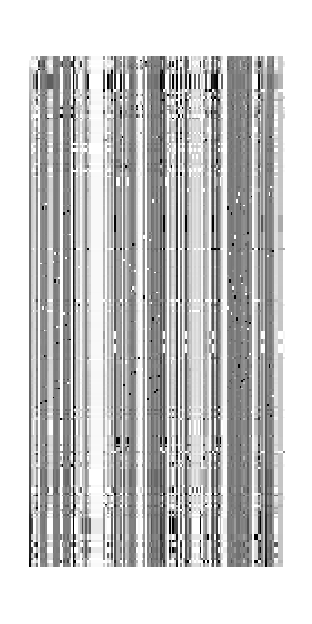

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Mina / max fluxes per reaction

```mathematica
TableForm[
Map[{Min[#],Max[#]}&,Transpose[NetFlux/@fluxMinMax]],
TableHeadings->{ReactionID/@Reactions[net],{"min","max"}}]
```

| min | max
2AMACHYD | 0 | 1000.
ACONTm | 0 | 705.882
ADK1 | 0 | 633.094
AKGDm | 0 | 666.667
AKGtm | -1000. | 1000.
ALATA_L | -1000. | 1000.
ALAmix | 0 | 1000.
ALAtl | 0 | 1000.
ALAtin | 0 | 1000.
ALAtout | 0 | 1000.
ARGN | 0 | 850.
ARGSL | 0 | 633.094
ARGSS | 0 | 633.094
ARGmix | 0 | 1000.
ARGtl | 0 | 1000.
ARGtin | 0 | 1000.
ARGtout | 0 | 1000.
ASPTA | -1000. | 1000.
ASPTAm | -1000. | 1000.
ASPtl | 0 | 1000.
ASPmix | 0 | 1000.
ASPtin | 0 | 1000.
ASPtout | 0 | 1000.
ASPtm | -1000. | 1000.
ATPS4m | 0 | 1000.
ATPtm | 0 | 1000.
CBPSam | 0 | 633.094
ATPASES | 0 | 1000.
CO2tm | -840. | 920.
CSm | 0 | 705.882
CYOOm | 0 | 333.333
CYOR-u10m | 0 | 666.667
ENO | -1000. | 1000.
ETF | 0 | 617.647
FAO16 | 0 | 88.2353
FAO14 | 0 | 88.2353
FAO12 | 0 | 88.2353
FAO10 | 0 | 88.2353
FAO8 | 0 | 88.2353
FAO6 | 0 | 88.2353
FAO4 | 0 | 88.2353
FBA | -400. | 1000.
FBP | 0 | 1000.
FUMm | 0 | 1000.
FUMtm | 0 | 633.094
G3PD1 | 0 | 1000.
G5SDxm | 0 | 685.714
G6PDH2r | 0 | 1000.
G6PPer | 0 | 1000.
G6Pter | 0 | 1000.
GAPD | -500. | 1000.
GHMT2r | -1000. | 1000.
GLCmix | 0 | 1000.
GLCtin | 0 | 1000.
GLCtout | 0 | 1000.
GLNmix | 0 | 1000.
GLNtin | 0 | 1000.
GLNtl | 0 | 1000.
GLNtout | 0 | 1000.
GLNtm | 0 | 1000.
GLNS | 0 | 1000.
GLUDxm | -1000. | 1000.
GLUNm | 0 | 1000.
GLUtl | 0 | 1000.
GLUt2m | -1000. | 1000.
GLUmix | 0 | 1000.
GLUtin | 0 | 1000.
GLUtout | 0 | 1000.
GLYtl | 0 | 1000.
GLYmix | 0 | 1000.
GLYtin | 0 | 1000.
GLYtout | 0 | 1000.
GLYCOGEN_BREAK | 0 | 1000.
GLYCPH | 0 | 1000.
GND | 0 | 1000.
H2Oter | 0 | 1000.
H2Otm | -1000. | 1000.
HCO3Em | 0 | 1000.
HEX1 | 0 | 1000.
Htm2 | -1000. | 1000.
ICDHxm | 0 | 705.882
LDH_L | 0 | 1000.
MALtm | -1000. | 1000.
MDH | -1000. | 1000.
MDHm | -1000. | 1000.
NADH2-u10m | 0 | 400.
NADPH_REDOX | 0 | 1000.
NDPK1 | 0 | 1000.
NH4tm | -1000. | 1000.
O2tm | 0 | 333.333
ORNTArm | 0 | 685.714
OCBTm | 0 | 633.094
ORNtm | 0 | 685.714
ORNt4m | 0 | 633.094
PCm | 0 | 1000.
PDHm | 0 | 600.
PEPCK | 0 | 1000.
PFK | 0 | 1000.
PGCD | 0 | 1000.
PGI | -1000. | 1000.
PGK | -500. | 1000.
PGL | 0 | 1000.
PGM | -1000. | 1000.
PGMT | 0 | 1000.
PIt2m | 0 | 1000.
PIter | 0 | 1000.
PPA | 0 | 633.094
PMTtm | 0 | 88.2353
PMTCOAT | 0 | 88.2353
PROTDEG_ALA | 0 | 1000.
PROTDEG_ARG | 0 | 1000.
PROTDEG_ASP | 0 | 1000.
PROTDEG_GLN | 0 | 1000.
PROTDEG_GLU | 0 | 1000.
PROTDEG_GLY | 0 | 1000.
PROTDEG_SER | 0 | 1000.
PROTSYN_ALA | 0 | 1000.
PROTSYN_ARG | 0 | 1000.
PROTSYN_ASP | 0 | 1000.
PROTSYN_GLN | 0 | 1000.
PROTSYN_GLU | 0 | 1000.
PROTSYN_GLY | 0 | 1000.
PROTSYN_SER | 0 | 1000.
PROTSYN_ATP | 0 | 666.667
PSERT | 0 | 1000.
PSP_L | 0 | 1000.
PYK | 0 | 1000.
PYRt2m | 0.0000351069 | 1000.
RPE | 0 | 666.667
RPI | 0 | 333.333
SERHL | 0 | 1000.
SERmix | 0 | 1000.
SERtl | 0 | 1000.
SERtin | 0 | 1000.
SERtout | 0 | 1000.
SUCD1m | 0 | 666.667
SUCOASm | 0 | 666.667
TALA | 0 | 333.333
TKT1 | 0 | 333.333
TKT2 | 0 | 333.333
TPI | -800. | 500.

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

{}

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]//TableForm
```

<Reaction ACONTm(rev)> | cit_m <=> icit_m
<Reaction AKGDm(rev)> | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
<Reaction ATPtm(rev)> | adp_c + atp_m <=> adp_m + atp_c
<Reaction G6Pter(rev)> | g6p_c <=> g6p_r
<Reaction GLNtm(rev)> | gln-L_c <=> gln-L_m
<Reaction ICDHxm(rev)> | icit_m + nad_m <=> akg_m + co2_m + nadh_m
<Reaction LDH_L(rev)> | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
<Reaction PYRt2m(rev)> | pyr_c <=> pyr_m

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[h,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[h2o,Output,Boundary]}

### Free fluxes

This is setup to select boundary fluxes first, then internal fluxes (typically controlling type II pathways)

```mathematica
freeFluxIndex=FindFreeFluxes[net]
```

{{10,17,23,59,68,72,89,98,106,124,128,131,135},{5,6,7,8,10,11,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48}}

```mathematica
Reactions[net]⟦freeFluxIndex⟦1⟧⟧
```

{<Reaction ALAtout>,<Reaction ARGtout>,<Reaction ASPtout>,<Reaction GLNtout>,<Reaction GLUtout>,<Reaction GLYtout>,<Reaction NH4tm(rev)>,<Reaction PFK>,<Reaction PIter>,<Reaction PROTSYN_ATP>,<Reaction PYRt2m(rev)>,<Reaction SERHL>,<Reaction SERtout>}

```mathematica
BoundaryFluxNames[bnet]⟦freeFluxIndex⟦2⟧⟧
```

{glc-D_IN,gln-L_IN,glu-L_IN,glycogen_IN,h2o_IN,h_IN,nh4_IN,o2_IN,pmt_IN,prot_ala_IN,prot_arg_IN,prot_asp_IN,prot_gln_IN,prot_glu_IN,prot_gly_IN,prot_ser_IN,ser-L_IN,thf_IN,ala-L_OUT,arg-L_OUT,asp-L_OUT,co2_OUT,glc-D_OUT,gln-L_OUT,glu-L_OUT,glyc_OUT,gly_OUT,h2o_OUT,h_OUT,lac-L_OUT,mlthf_OUT,nh4_OUT,prot_ala_OUT,prot_arg_OUT,prot_asp_OUT,prot_gln_OUT,prot_glu_OUT,prot_gly_OUT,prot_ser_OUT,ser-L_OUT,thf_OUT,urea_OUT}

Total # free variables

```mathematica
Length[Flatten[freeFluxIndex]]
```

55

## Generate EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMaps,bmaps,{"C"},targets,symmetry];
Length[emuReactions]
```

1573

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[172,<asp-L_c{(24)}>,<asp-L_m{(24)}>,1],EMUReaction[28,<akg_m{(1)}>,<succoa_m{(2)}>,1],EMUReaction[157,<ser-L_l{(123)}>,<ser-L_c{(123)}>,1],EMUReaction[22,<prot_ser_i{(2)}>,<prot_ser_l{(2)}>,1],EMUReaction[167,<co2_m{(1)} x succoa_m{(1234)}>,<akg_m{(12345)}>,1],EMUReaction[176,<dhap_c{(3)}>,<fdp_c{(6)}>,1],EMUReaction[185,<akg_m{(1234)}>,<icit_m{(1246)}>,1],EMUReaction[85,<glu-L_c{(1)}>,<gln-L_c{(1)}>,1],EMUReaction[133,<pmt_m{(fg)}>,<pmtcoa_m{(fg)}>,1],EMUReaction[170,<glu-L_c{(5)}>,<akg_c{(5)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

914

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["btcoa",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

FAO6_f | <hexcoa_m{(1)}> | <btcoa_m{(1)}>
FAO6_f | <hexcoa_m{(2)}> | <btcoa_m{(2)}>
FAO6_f | <hexcoa_m{(3)}> | <btcoa_m{(3)}>
FAO6_f | <hexcoa_m{(4)}> | <btcoa_m{(4)}>
FAO6_f | <hexcoa_m{(12)}> | <btcoa_m{(12)}>
FAO6_f | <hexcoa_m{(34)}> | <btcoa_m{(34)}>

```mathematica
Cases[emuReactions,
EMUReaction[i_,s:EMU[Metabolite["btcoa",__],_],p_EMU,k_]:>{emuReactionNames⟦i⟧,s,p,1}]//TableForm
```

FAO4_f | <btcoa_m{(12)}> | <accoa_m{(12)}> | 1
FAO4_f | <btcoa_m{(34)}> | <accoa_m{(12)}> | 1
FAO4_f | <btcoa_m{(1)}> | <accoa_m{(1)}> | 1
FAO4_f | <btcoa_m{(3)}> | <accoa_m{(1)}> | 1
FAO4_f | <btcoa_m{(2)}> | <accoa_m{(2)}> | 1
FAO4_f | <btcoa_m{(4)}> | <accoa_m{(2)}> | 1

```mathematica
Cases[emuReactions,
EMUReaction[i_,s:EMU[Metabolite["btcoa",__],_],p_EMU,_]]
```

{EMUReaction[65,<btcoa_m{(12)}>,<accoa_m{(12)}>,1],EMUReaction[65,<btcoa_m{(34)}>,<accoa_m{(12)}>,1],EMUReaction[65,<btcoa_m{(1)}>,<accoa_m{(1)}>,1],EMUReaction[65,<btcoa_m{(3)}>,<accoa_m{(1)}>,1],EMUReaction[65,<btcoa_m{(2)}>,<accoa_m{(2)}>,1],EMUReaction[65,<btcoa_m{(4)}>,<accoa_m{(2)}>,1]}

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 435 internals, 84 substrates, 0 condensations >
2 | <EMUEquation (2), 260 internals, 50 substrates, 5 condensations >
3 | <EMUEquation (3), 120 internals, 24 substrates, 6 condensations >
4 | <EMUEquation (4), 53 internals, 10 substrates, 4 condensations >
5 | <EMUEquation (5), 26 internals, 6 substrates, 2 condensations >
6 | <EMUEquation (6), 20 internals, 4 substrates, 6 condensations >

### Specify input isotopomers (tracers)

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

Check that all inputs are numeric

```mathematica
And@@NumericQ/@Flatten[Last/@irList]
```

True

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

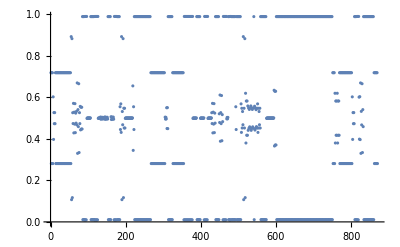
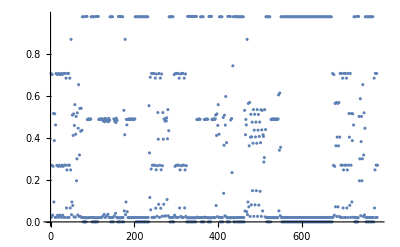
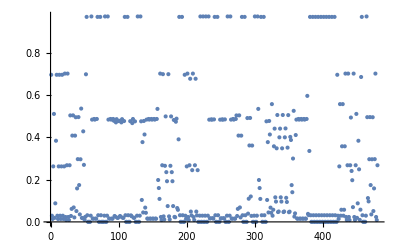
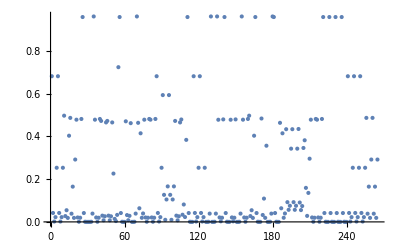
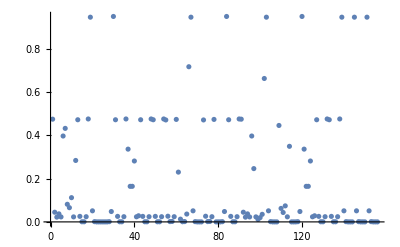
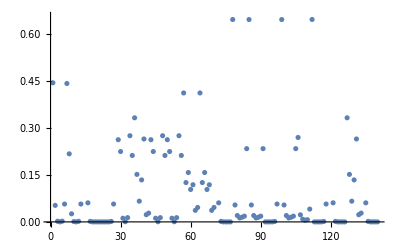

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## MID data

This directory must contain peak area data in .tsv format

```mathematica
lcmsDataDir=FileNameJoin[{liverProjectPath,"lcms-data"}]
```

C:\Users\rolnil\Linköpings universitet\13C MFA - Documents\Lever snitt ex vivo\lcms-data

Patient data sets used

```mathematica
patientIds={"L005","L008","L010","L016","L020"};
```

Experiment IDs as defined in the database

```mathematica
ExperimentId[patientId_]:="Human_liver_"<>patientId
```

### Import peak areas

Here we import a metabolite x samples matrix combining data from all experiments.

Despite its name, the ImportMIDTable function returns peak areas, not MI fractions.
Combines peak areas from the tissue extract and cells

```mathematica
CombinePeakAreaData[allMetIds_,allSampleIds_,allMIDs_]:=
((* verify that metabolite IDs are the same in all files *)
If[Length [Union[allMetIds]]≠1,Return[$Failed]];
(* combine the data tables *)
{First[allMetIds],
Join@@allSampleIds,
ArrayFlatten[{allMIDs}]})
```

Import data for each experiment

```mathematica
AddPatientId[{metIds_,sampleIds_,mids_},patientId_String]:=
{metIds,Thread[{patientId,sampleIds}],mids}
```

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=CombinePeakAreaData@@Transpose[
Join@@Table[
AddPatientId[
ImportMIDTable[
FileNameJoin[{lcmsDataDir,patientId,ExperimentId[patientId]<>suffix}]],
patientId],
{patientId,patientIds},{suffix,{".tsv","_medium.tsv"}}]];
```

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{3h2mbut,3mob,4mop,acrn,ade,adp,ahcys,akg,amp,ascb-L,asn-L,atp,creat,crn,dhdascb,f6p,fad,fru,g1p,g3pc,g6p,gchola,glcnt,glcur,gthox,gthrd,gudac,his-L,hivcrn,ile-L,imp,inost,ivcrn,Lcystin,leu-L,lpc_18_0,lpc_18_1,lys-L,met-L,nad,nadh,pc_18_1_16_0,pc_18_1_18_1,pc_22_6_16_0,phe-L,pmtcrn,pro-L,propcrn,r5p,sbt-D,thr-L,trp-L,tyr-L,udp,udpg,udpglcur,ump,urate,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[sampleIds]
```

176

Each measured metabolite ID is a list, since we may have peaks that represent multiple metabolites (unresolved peaks, e.g. leu/ile)

```mathematica
measuredMetIds
```

{{glc-D},{ala-L},{arg-L},{asp-L},{gln-L},{ser-L},{mal-L},{orn},{citr-L},{glyc3p},{glu-L},{gly},{cit}}

```mathematica
Length[measuredMetIds]
```

13

```mathematica
Dimensions[measuredMIDs]
```

{13,176}

### Sample annotations and experimental groups

Returns a list of tuples {{patientID, sampleID}, factor-list}

```mathematica
ImportSampleInfo[patientId_String,fileName_String]:=
Block[{sampleInfo,factorNames,sampleIds,factors},
sampleInfo=Import[fileName,"TSV"];
(* first row are factor names, first column is sample ID *)
factorNames=Rest[First[sampleInfo]];
sampleIds=Rest[First/@sampleInfo];
factors=Rest/@Rest[sampleInfo];
Transpose[
{Thread[{patientId,sampleIds}],
Table[Transpose[{factorNames,f}],{f,factors}]}]]
```

```mathematica
sampleInfo=Join@@Table[
ImportSampleInfo[
patientId,
FileNameJoin[{lcmsDataDir,patientId,ExperimentId[patientId]<>"_sampleinfo.tsv"}]],
{patientId,patientIds}];
```

Make a list of annotations for each sample ID

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule@@#&,sampleInfo],{1}];
```

```mathematica
Length[sampleInfo]
```

176

An experimental group is defined as the a set of samples with identical annotations

```mathematica
allGroups=Union[sampleInfo];
Length[allGroups]
```

77

Select experimental groups for tissue extracts and media based on sample annotations

```mathematica
tissueAnn={{"group","tissue slice 24h"},{"material","tissue extract"},{"medium","13C"}};
mediumAnn={{"group","spent medium 24h"},{"material","medium"},{"medium","13C"}};
```

```mathematica
GetSampleIndex[sampleInfo_,factorList_]:=
Flatten[Position[sampleInfo,fl_List/;SubsetQ[fl,factorList]]]
```

Get a subset of annotations for a specified list of factor names, in the specified order.
If the factor is not present, return Missing

```mathematica
SelectAnnotations[ann:{{_String,_String}..},factorNames:{_String..}]:=
Replace[factorNames,Append[Map[Rule@@#&,ann],_String->Missing],{1}]
```

```mathematica
SelectAnnotations[ann:{{_String,_String}..},factorName_String]:=
First[SelectAnnotations[ann,{factorName}]]
```

#### Tissue groups

```mathematica
tissueGroups=Cases[allGroups,fl_List/;SubsetQ[fl,tissueAnn]];
```

```mathematica
Table[SelectAnnotations[ann,{"patient","group","dietary_state"}],{ann,tissueGroups}]//TableForm
```

L005 | tissue slice 24h | Missing
L008 | tissue slice 24h | Missing
L010 | tissue slice 24h | Missing
L016 | tissue slice 24h | Missing
L020 | tissue slice 24h | fasted
L020 | tissue slice 24h | fed

```mathematica
tissueGroupIndex=Table[GetSampleIndex[sampleInfo,ann],{ann,tissueGroups}]
```

{{13,14,15},{46,47,48},{79,80,81},{111,112,113},{139,141,143},{140,142,144}}

```mathematica
mediumGroups=Cases[allGroups,fl_List/;SubsetQ[fl,mediumAnn]];
```

```mathematica
Table[SelectAnnotations[ann,{"patient","group","dietary_state"}],{ann,mediumGroups}]//TableForm
```

L005 | spent medium 24h | Missing
L008 | spent medium 24h | Missing
L010 | spent medium 24h | Missing
L016 | spent medium 24h | Missing
L020 | spent medium 24h | fasted
L020 | spent medium 24h | fed

```mathematica
mediumGroupIndex=Table[GetSampleIndex[sampleInfo,ann],{ann,mediumGroups}]
```

{{25,26,27},{52,53,54},{91,92,93},{117,118,119},{151,153,155},{152,154,156}}

Experiment group names, for naming result folders etc

```mathematica
expGroupNames=Table[
ListToString[Cases[SelectAnnotations[ann,{"patient","dietary_state"}],_String],"_"],
{ann,tissueGroups}]
```

{L005,L008,L010,L016,L020_fasted,L020_fed}

```mathematica
nGroups=Length[expGroupNames]
```

6

### Target-to-data mapping and mixing matrix

For each target, this gives a pair {measured metabolite ID, measurement name}.
Extracellular metabolites are given suffix _EC
Salvaged amp is treated as “extracellular” here merely to separate it from amp/atp/adp cofactors (which have no carbon mapping)

```mathematica
measuredMap=Table[
{First[Cases[measuredMetIds,ml_/;MemberQ[ml,MetaboliteID[Metabolite[target]]]]],
Replace[target,
{EMU[Metabolite["amp","Extracellular",_],_]:>"amp_salvage",
EMU[Metabolite[m_,"Extracellular",_],_]:>m<>"_EC",
EMU[Metabolite[m_,_,_],_]:>m}]},
{target,targets}];
```

```mathematica
TableForm[measuredMap,TableHeadings->{targets,None}]
```

<ala-L_c{(123)}> | ala-L | ala-L
<ala-L_e{(123)}> | ala-L | ala-L_EC
<ala-L_l{(123)}> | ala-L | ala-L
<arg-L_c{(123456)}> | arg-L | arg-L
<arg-L_e{(123456)}> | arg-L | arg-L_EC
<arg-L_l{(123456)}> | arg-L | arg-L
<asp-L_c{(1234)}> | asp-L | asp-L
<asp-L_e{(1234)}> | asp-L | asp-L_EC
<asp-L_l{(1234)}> | asp-L | asp-L
<asp-L_m{(1234)}> | asp-L | asp-L
<cit_m{(123456)}> | cit | cit
<citr-L_c{(123456)}> | citr-L | citr-L
<citr-L_m{(123456)}> | citr-L | citr-L
<glc-D_c{(123456)}> | glc-D | glc-D
<glc-D_r{(123456)}> | glc-D | glc-D
<glc-D_e{(123456)}> | glc-D | glc-D_EC
<gln-L_c{(12345)}> | gln-L | gln-L
<gln-L_e{(12345)}> | gln-L | gln-L_EC
<gln-L_l{(12345)}> | gln-L | gln-L
<gln-L_m{(12345)}> | gln-L | gln-L
<glu-L_c{(12345)}> | glu-L | glu-L
<glu-L_e{(12345)}> | glu-L | glu-L_EC
<glu-L_l{(12345)}> | glu-L | glu-L
<glu-L_m{(12345)}> | glu-L | glu-L
<gly_c{(12)}> | gly | gly
<gly_e{(12)}> | gly | gly_EC
<gly_l{(12)}> | gly | gly
<glyc3p_c{(123)}> | glyc3p | glyc3p
<mal-L_c{(1234)}> | mal-L | mal-L
<mal-L_m{(1234)}> | mal-L | mal-L
<orn_c{(12345)}> | orn | orn
<orn_m{(12345)}> | orn | orn
<ser-L_c{(123)}> | ser-L | ser-L
<ser-L_e{(123)}> | ser-L | ser-L_EC
<ser-L_l{(123)}> | ser-L | ser-L

```mathematica
measuredMetNames=Union[Last/@measuredMap]
```

{ala-L,ala-L_EC,arg-L,arg-L_EC,asp-L,asp-L_EC,cit,citr-L,glc-D,glc-D_EC,gln-L,gln-L_EC,glu-L,glu-L_EC,gly,glyc3p,gly_EC,mal-L,orn,ser-L,ser-L_EC}

```mathematica
measuredMetIds
```

{{glc-D},{ala-L},{arg-L},{asp-L},{gln-L},{ser-L},{mal-L},{orn},{citr-L},{glyc3p},{glu-L},{gly},{cit}}

```mathematica
emuMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[Last/@measuredMap,measuredMetNames],
Range[Length[targets]]}],1]],
{Length[measuredMetNames],Length[targets]}]
```

SparseArray[<35>, {21, 35}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

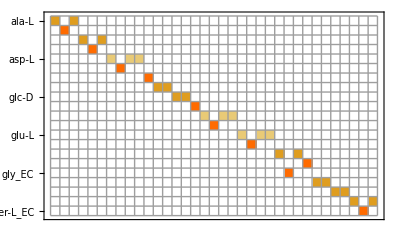

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetNames]],measuredMetNames}],None},Mesh->True]
```

### Get measured MIDs

MIDs to fit for each measurement.
Here we need to map measurements to measured metabolite ID and sample group

```mathematica
midsToFit=Block[{mapIndex,metIndex,sampleIndex},
mapIndex=ReindexList[measuredMetNames,measuredMap⟦All,2⟧];
metIndex=ReindexList[measuredMap⟦mapIndex,1⟧,measuredMetIds];
Table[
sampleIndex=If[
StringMatchQ[measuredMetNames⟦i⟧,"*_EC"],
mediumGroupIndex,
tissueGroupIndex];
Table[
Normal/@MIDNormalize/@measuredMIDs⟦metIndex⟦i⟧,ix⟧,
{ix,sampleIndex}],
{i,Length[measuredMetNames]}]];
```

This is now a measurement x groups x replicates array of MIDs

```mathematica
midsToFit//Dimensions
```

{21,6,3}

Compute mean and standard deviation, with a minimum

```mathematica
minSD=0.03;
```

```mathematica
midsToFitMean=Table[Mean/@midsToFit⟦All,i⟧, {i,nGroups}];
midsToFitMean//Dimensions
```

{6,21}

```mathematica
midsToFitSD=Table[Map[Max[StandardDeviation[#],minSD]&,midsToFit⟦All,i⟧],{i,nGroups}];
midsToFitSD//Dimensions
```

{6,21}

### Plot measured MIDs

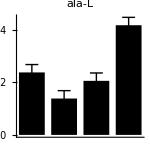
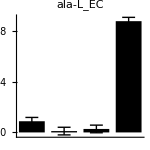
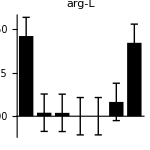
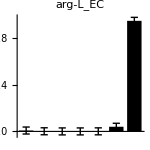
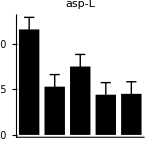
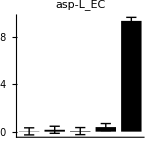
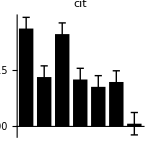
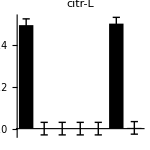

```mathematica
With[{j=1},
Table[
ErrorBarChart[
midsToFitMean⟦j,i⟧,
Table[midsToFitSD⟦j,i⟧,{Length[midsToFitMean⟦j,i⟧]}],
PlotRange->{0,All},AspectRatio->1,ImageSize->150,PlotLabel->measuredMetNames⟦i⟧],
{i,Length[measuredMetNames]}]]
```

Medium glucose M+0 fractions for L005 ... L020 fasted, for reviewer question

```mathematica
Block[{i=10, mediumGlc},
Print[measuredMetNames⟦i⟧];
mediumGlc={1040,619,619,619,619};
midsToFitMean⟦1;;5,i,1⟧*mediumGlc]
```

glc-D_EC

{46.397,46.906,72.1904,104.466,127.135}

```mathematica
expGroupNames
```

{L005,L008,L010,L016,L020_fasted,L020_fed}

## Uptake/release data

### Map uptake/release measurements to EMU fluxes (flux mixing matrix)

This map defines the measured reactions (linear combinations)

```mathematica
fluxMeasurementMap=Import[FileNameJoin[{modelDir,"measured-flux-mapping.tsv"}]];
```

```mathematica
fluxMeasurementMap⟦All,2⟧=StringReplace[fluxMeasurementMap⟦All,2⟧,
{s__~~"_R"~~EndOfLine:>s<>"_r",
s:(__~~("_IN"|"_OUT")~~EndOfLine)->s,
s__:>s<>"_f"}];
```

Ensure measurement names do not collide with flux names

```mathematica
fluxMeasurementMap⟦All,1⟧=Table[StringJoin["meas_",s],{s,fluxMeasurementMap⟦All,1⟧}];
```

```mathematica
measuredBoundaryIds=Union[fluxMeasurementMap⟦All,1⟧];
```

```mathematica
measReactions=Union[fluxMeasurementMap⟦All,2⟧];
```

```mathematica
fluxMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[fluxMeasurementMap⟦All,1⟧,measuredBoundaryIds],
ReindexList[fluxMeasurementMap⟦All,2⟧,measReactions]}],
fluxMeasurementMap⟦All,3⟧]],
{Length[measuredBoundaryIds],Length[measReactions]}]
```

SparseArray[<44>, {36, 44}]

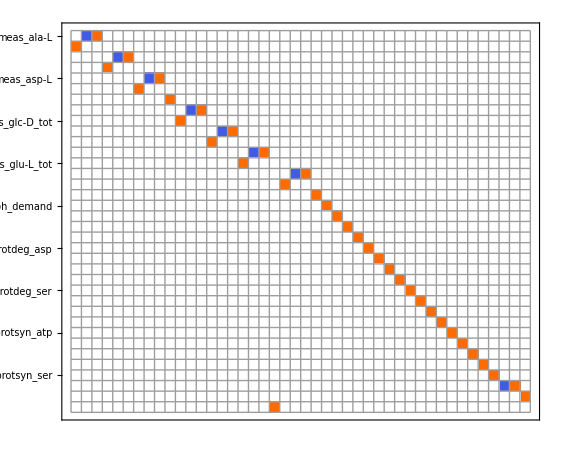

```mathematica
MatrixPlot[fluxMixing,
FrameTicks->{Transpose[{Range[Length[measuredBoundaryIds]],measuredBoundaryIds}],None},Mesh->True]
```

```mathematica
Transpose[
{measuredBoundaryIds⟦NonZeroIndices[fluxMixing]⟦All,1⟧⟧,
measReactions⟦NonZeroIndices[fluxMixing]⟦All,2⟧⟧,
NonZeroElements[fluxMixing]}]//TableForm
```

meas_ala-L | ALAtin_f | -1
meas_ala-L | ALAtout_f | 1
meas_ala-L_tot | ala-L_IN | 1
meas_arg-L | ARGtin_f | -1
meas_arg-L | ARGtout_f | 1
meas_arg-L_tot | arg-L_IN | 1
meas_asp-L | ASPtin_f | -1
meas_asp-L | ASPtout_f | 1
meas_asp-L_tot | asp-L_IN | 1
meas_atpases | ATPASES_f | 1
meas_glc-D | GLCtin_f | -1
meas_glc-D | GLCtout_f | 1
meas_glc-D_tot | glc-D_IN | 1
meas_gln-L | GLNtin_f | -1
meas_gln-L | GLNtout_f | 1
meas_gln-L_tot | gln-L_IN | 1
meas_glu-L | GLUtin_f | -1
meas_glu-L | GLUtout_f | 1
meas_glu-L_tot | glu-L_IN | 1
meas_gly | GLYtin_f | -1
meas_gly | GLYtout_f | 1
meas_gly_tot | gly_IN | 1
meas_lac-L | lac-L_OUT | 1
meas_nadph_demand | NADPH_REDOX_f | 1
meas_o2 | o2_IN | 1
meas_protdeg_ala | PROTDEG_ALA_f | 1
meas_protdeg_arg | PROTDEG_ARG_f | 1
meas_protdeg_asp | PROTDEG_ASP_f | 1
meas_protdeg_gln | PROTDEG_GLN_f | 1
meas_protdeg_glu | PROTDEG_GLU_f | 1
meas_protdeg_gly | PROTDEG_GLY_f | 1
meas_protdeg_ser | PROTDEG_SER_f | 1
meas_protsyn_ala | PROTSYN_ALA_f | 1
meas_protsyn_arg | PROTSYN_ARG_f | 1
meas_protsyn_asp | PROTSYN_ASP_f | 1
meas_protsyn_atp | PROTSYN_ATP_f | 1
meas_protsyn_gln | PROTSYN_GLN_f | 1
meas_protsyn_glu | PROTSYN_GLU_f | 1
meas_protsyn_gly | PROTSYN_GLY_f | 1
meas_protsyn_ser | PROTSYN_SER_f | 1
meas_ser-L | ser-L_IN | -1
meas_ser-L | ser-L_OUT | 1
meas_urea | urea_OUT | 1
meas_VLDL_TAG | glyc_OUT | 1

### Import uptake/release data

Map experimental groups to column names in the uptake/release data file

```mathematica
uptakeReleaseExpNames=Table[
ListToString[
Cases[
SelectAnnotations[group,{"patient","dietary_state"}],
_String]," "],
{group,tissueGroups}]
```

{L005,L008,L010,L016,L020 fasted,L020 fed}

Set priority for data source types (lower is better)

```mathematica
uptakeReleasePriority=Thread[Rule[#,Range[Length[#]]]]&[
{"clin chem","12C int std","elisa","peak ratio","imputed","literature","total"}]
```

{clin chem→1,12C int std→2,elisa→3,peak ratio→4,imputed→5,literature→6,total→7}

Import data. This gives an {experiment x metabolite x {mean, SD}} array

```mathematica
boundaryFlux=Block[{ur,urLabels,urMet,urPrio,cols,nonzeroIndex,rules},
ur=First[Import[
FileNameJoin[{liverProjectPath,"medium-concentrations","uptake-release-fluxes-all.xlsx"}]]];
urLabels=Drop[First[ur],2];
(* prevent name collision in GAMS *)
urMet=Map[StringJoin["meas_",#]&,Drop[ur,2]⟦All,1⟧];
(* priority *)
urPrio=Drop[ur,2]⟦All,2⟧/.uptakeReleasePriority;
ur=Drop[ur,2,2];
(* for each experiment group *)
Table[
cols=Position[urLabels,expName]⟦1,1⟧+{0,1};
nonzeroIndex=Flatten[Position[ur⟦All,cols⟧,{_Real,_Real}]];
(* make replacement rules *)
rules=Thread[Rule[urMet⟦nonzeroIndex⟧,ur⟦nonzeroIndex,cols⟧]];
(* sort by data source precedence *)
rules=Part[rules,Ordering[urPrio⟦nonzeroIndex⟧]];
(* extract mean and s.d. *)
Replace[measuredBoundaryIds,rules,{1}],
{expName,uptakeReleaseExpNames}]];
```

```mathematica
Dimensions[boundaryFlux]
```

{6,36,2}

### Summary table

```mathematica
Transpose[boundaryFlux]//Dimensions
```

{36,6,2}

```mathematica
TableForm[
Flatten/@Transpose[boundaryFlux],
TableHeadings->{measuredBoundaryIds,uptakeReleaseExpNames}]
```

| L005 | L008 | L010 | L016 | L020 fasted | L020 fed |  |  |  |  |  | 
meas_ala-L | -20.5801 | 18.4995 | -17.7902 | 9.67183 | 1.76065 | 3.59445 | -11.0685 | 7.44441 | 1.21418 | 2.88417 | -25.1644 | 3.09359
meas_ala-L_tot | 190.982 | 19.0982 | 113.68 | 11.368 | 113.68 | 11.368 | 113.68 | 11.368 | 113.68 | 11.368 | 227.36 | 22.736
meas_arg-L | -12.4918 | 0.790237 | -8.0829 | 2.40319 | -15.4673 | 0.19517 | -8.29496 | 1.4535 | -22.9542 | 9.3091 | -44.3099 | 3.25765
meas_arg-L_tot | 54.2691 | 5.42691 | 32.303 | 3.2303 | 32.303 | 3.2303 | 32.303 | 3.2303 | 32.303 | 3.2303 | 64.606 | 6.4606
meas_asp-L | -9.01105 | 1.13203 | -2.69869 | 0.438252 | -5.12774 | 0.263811 | -1.93634 | 1.26735 | -5.26635 | 1.424 | -7.55991 | 0.38817
meas_asp-L_tot | 42.7345 | 4.27345 | 25.4372 | 2.54372 | 25.4372 | 2.54372 | 25.4372 | 2.54372 | 25.4372 | 2.54372 | 50.8744 | 5.08744
meas_atpases | 2166.67 | 650. | 2166.67 | 650. | 2166.67 | 650. | 2166.67 | 650. | 2166.67 | 650. | 2166.67 | 650.
meas_glc-D | 26.2375 | 2.62375 | -5.622 | -0.5622 | 32.61 | 3.261 | 75.339 | 7.5339 | 30.361 | 3.0361 | 15.742 | 1.5742
meas_glc-D_tot | 1040. | 104. | 619.048 | 61.9048 | 619.048 | 61.9048 | 619.048 | 61.9048 | 619.048 | 61.9048 | 1238.1 | 123.81
meas_gln-L | -47.0367 | 13.5304 | -45.8353 | 8.20414 | -13.8731 | 13.4053 | -16.1411 | 12.3192 | -42.4842 | 5.05215 | -61.583 | 3.48136
meas_gln-L_tot | 378.182 | 37.8182 | 225.108 | 22.5108 | 225.108 | 22.5108 | 225.108 | 22.5108 | 225.108 | 22.5108 | 450.216 | 45.0216
meas_glu-L | 31.5873 | 5.41112 | 21.344 | 5.2498 | 22.6452 | 12.0562 | 26.6069 | 9.69125 | 18.0115 | 1.54489 | 26.4629 | 2.99284
meas_glu-L_tot | 64.2909 | 6.42909 | 38.2684 | 3.82684 | 38.2684 | 3.82684 | 38.2684 | 3.82684 | 38.2684 | 3.82684 | 76.5368 | 7.65368
meas_gly | -10.3426 | 6.94716 | 1.55876 | 3.96403 | 3.5892 | 5.14323 | -2.45657 | 6.8255 | -0.800331 | 3.77238 | -8.00394 | 6.25127
meas_gly_tot | 126.124 | 12.6124 | 75.0736 | 7.50736 | 75.0736 | 7.50736 | 75.0736 | 7.50736 | 75.0736 | 7.50736 | 150.147 | 15.0147
meas_lac-L | 61.8455 | 6.18455 | 115.82 | 11.582 | 159.673 | 15.9673 | 140.558 | 14.0558 | 65.219 | 6.5219 | 67.468 | 6.7468
meas_nadph_demand | 300. | 150. | 300. | 150. | 300. | 150. | 300. | 150. | 300. | 150. | 300. | 150.
meas_o2 | 2500. | 500. | 2500. | 500. | 2500. | 500. | 2500. | 500. | 2500. | 500. | 2500. | 500.
meas_protdeg_ala | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974
meas_protdeg_arg | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894
meas_protdeg_asp | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08
meas_protdeg_gln | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478
meas_protdeg_glu | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257
meas_protdeg_gly | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915
meas_protdeg_ser | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425
meas_protsyn_ala | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974 | 36.58 | 10.974
meas_protsyn_arg | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894 | 12.98 | 3.894
meas_protsyn_asp | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08 | 23.6 | 7.08
meas_protsyn_atp | 295. | 88.5 | 295. | 88.5 | 295. | 88.5 | 295. | 88.5 | 295. | 88.5 | 295. | 88.5
meas_protsyn_gln | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478 | 8.26 | 2.478
meas_protsyn_glu | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257 | 24.19 | 7.257
meas_protsyn_gly | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915 | 23.305 | 6.9915
meas_protsyn_ser | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425 | 14.75 | 4.425
meas_ser-L | 1.7778 | 0.557055 | 2.54013 | 0.722155 | -0.186258 | 1.07424 | -2.2805 | 2.45732 | 0.691824 | 0.501432 | -3.44604 | 3.00753
meas_urea | 125.666 | 15.6599 | 78.4195 | 7.81502 | 77.8912 | 18.6414 | 100. | 50. | 100. | 50. | 100. | 50.
meas_VLDL_TAG | 5.01164 | 0.14135 | 3.08242 | 0.192057 | 3.14685 | 0.0665498 | 4.75 | 1.89 | 4.75 | 1.89 | 4.75 | 1.89

## Setup GAMS parameters

```mathematica
gamsModelName=modelId
```

liver-model-fatty-acids-2

```mathematica
baseDir=NotebookDirectory[]
```

C:\code\liver-flux-analysis\flux-analysis-liver\

```mathematica
GAMSDirectory[groupName_String]:=FileNameJoin[{baseDir,groupName,"gams","fatty-acids-2"}]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
gamsExperiments={"experiment1"};
```

## Run restarts to find best initial vector

For any change made, we need to make sure differences in fit is not due to failure of optimization.
Run multiple restarts for each model, read back the results and fit the best chi2 score.
currently the only way to do this is to generate multiple gams files for each problem.

```mathematica
nRestarts=10;
```

This currently takes about 5 sec / GAMS model
For 60 models (10 for each donors) total ~5 min

### Setup directories

```mathematica
GAMSRestartDirectory[groupName_String]:=FileNameJoin[{baseDir,"gams","fatty-acids-2","restarts",groupName}]
```

```mathematica
GAMSRestartModelName[gamsModelName_String,i_Integer]:=gamsModelName<>"_restart_"<>ToString[i]
```

```mathematica
GAMSRestartDirectory/@expGroupNames
```

{C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L005,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L008,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L010,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L016,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L020_fasted,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\restarts\L020_fed}

```mathematica
Do[
If[!FileExistsQ[GAMSRestartDirectory[g]],
CreateDirectory[GAMSRestartDirectory[g]]],
{g,expGroupNames}]
```

### Generate optimization models

```mathematica
restartInitFlux=Table[RandomFluxState[10],{nGroups},{nRestarts}];
```

```mathematica
Do[
GAMSExport[
GAMSRestartDirectory[expGroupNames⟦i⟧],GAMSRestartModelName[gamsModelName,j],
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measuredBoundaryIds,measReactions,Sequence@@Transpose[boundaryFlux⟦i⟧],fluxMixing,
(* measured MIDs *)
gamsExperiments,measuredMetNames,{midsToFitMean⟦i⟧},{midsToFitSD⟦i⟧},
(* targets *)
targets,emuMixing,
(* random initial vector *)
restartInitFlux⟦i,j⟧,"FluxCI"->{}],
{i,nGroups},{j,nRestarts}]
```

### Run GAMS

Run gams.bat from the command line

### Pick initial vector by best initial value

Import objective values from GAMS

```mathematica
restartObjVal=Table[
Import[
FileNameJoin[{GAMSRestartDirectory[g],GAMSRestartModelName[gamsModelName,j]<>"_objval.tsv"}]]⟦1,1⟧,
{g,expGroupNames},{j,nRestarts}];
```

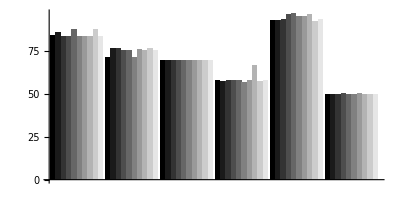

```mathematica
SimpleBarChart[Clip[restartObjVal,{0,300}],AspectRatio->1/2]
```

Pick best initial vectors

```mathematica
bestRestarts=First/@Ordering/@restartObjVal;
```

```mathematica
Table[restartObjVal⟦i,bestRestarts⟦i⟧⟧,{i,nGroups}]
```

{83.3801,71.1753,69.3751,56.4021,92.2429,49.4034}

## Optimal solution

### Import best restart solutions

```mathematica
emuMixingGams=Table[
ImportGAMSEmuMixing[
GAMSRestartDirectory[expGroupNames⟦i⟧],GAMSRestartModelName[gamsModelName,bestRestarts⟦i⟧],
measuredMetNames,targets],
{i,nGroups}];
```

```mathematica
midGams=Table[
First[ImportGAMSIsotopes[
GAMSRestartDirectory[expGroupNames⟦i⟧],GAMSRestartModelName[gamsModelName,bestRestarts⟦i⟧],
gamsExperiments,emus]],
{i,nGroups}];
```

```mathematica
fittedMIDs=Table[
MixTargetMIDs[emuMixingGams⟦i⟧,midGams⟦i,ReindexList[targets,emus]⟧],
{i,nGroups}];
```

```mathematica
fluxGams=Table[
ImportGAMSFluxes[
GAMSRestartDirectory[expGroupNames⟦i⟧],GAMSRestartModelName[gamsModelName,bestRestarts⟦i⟧],
net,EMUFluxMap[net]],
{i,nGroups}];
```

### Estimated mixing matrix

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixing];
TableForm[
Transpose[Map[Extract[#,ij]&,emuMixingGams]],
TableHeadings->{Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧}],expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
{ala-L,<ala-L_c{(123)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{ala-L,<ala-L_l{(123)}>} | 0 | 0 | 0 | 0 | 0 | 0
{ala-L_EC,<ala-L_e{(123)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{arg-L,<arg-L_c{(123456)}>} | 0.791711 | 0.731136 | 0.678018 | 0.524661 | 0.213703 | 0.276623
{arg-L,<arg-L_l{(123456)}>} | 0.208289 | 0.268864 | 0.321982 | 0.475339 | 0.786297 | 0.723377
{arg-L_EC,<arg-L_e{(123456)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{asp-L,<asp-L_c{(1234)}>} | 0.941121 | 0 | 0 | 0 | 0.870811 | 0.939741
{asp-L,<asp-L_l{(1234)}>} | 0.0588791 | 0 | 0.00815125 | 0.186729 | 0.0735154 | 0.0602593
{asp-L,<asp-L_m{(1234)}>} | 0 | 1. | 0.991849 | 0.813271 | 0.0556732 | 0
{asp-L_EC,<asp-L_e{(1234)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{cit,<cit_m{(123456)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{citr-L,<citr-L_c{(123456)}>} | 0.5 | 0.500002 | 0.500046 | 0.5 | 0.5 | 0.5
{citr-L,<citr-L_m{(123456)}>} | 0.5 | 0.499998 | 0.499954 | 0.5 | 0.5 | 0.5
{glc-D,<glc-D_c{(123456)}>} | 0.489621 | 0.258314 | 0.212646 | 0.290996 | 0.310836 | 0.500928
{glc-D,<glc-D_r{(123456)}>} | 0.510379 | 0.741686 | 0.787354 | 0.709004 | 0.689164 | 0.499072
{glc-D_EC,<glc-D_e{(123456)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{gln-L,<gln-L_c{(12345)}>} | 0.333333 | 0.333333 | 0.333345 | 0.33334 | 0.333331 | 0.333333
{gln-L,<gln-L_l{(12345)}>} | 0 | 0 | 0 | 0 | 0 | 0
{gln-L,<gln-L_m{(12345)}>} | 0.666667 | 0.666667 | 0.666655 | 0.66666 | 0.666669 | 0.666667
{gln-L_EC,<gln-L_e{(12345)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{glu-L,<glu-L_c{(12345)}>} | 0 | 0 | 0 | 0 | 0 | 0.980452
{glu-L,<glu-L_l{(12345)}>} | 0 | 0 | 0 | 0 | 0.040775 | 0.0195479
{glu-L,<glu-L_m{(12345)}>} | 1. | 1. | 1. | 1. | 0.959225 | 0
{glu-L_EC,<glu-L_e{(12345)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{gly,<gly_c{(12)}>} | 0.983733 | 1. | 1. | 0.783596 | 1. | 1.
{gly,<gly_l{(12)}>} | 0.0162674 | 0 | 0 | 0.216404 | 0 | 0
{glyc3p,<glyc3p_c{(123)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{gly_EC,<gly_e{(12)}>} | 1. | 1. | 1. | 1. | 1. | 1.
{mal-L,<mal-L_c{(1234)}>} | 0 | 0 | 0 | 0 | 1. | 1.
{mal-L,<mal-L_m{(1234)}>} | 1. | 1. | 1. | 1. | 0 | 0
{orn,<orn_c{(12345)}>} | 0.5 | 0.5 | 0.499976 | 0.500001 | 0.5 | 0.5
{orn,<orn_m{(12345)}>} | 0.5 | 0.5 | 0.500024 | 0.499999 | 0.5 | 0.5
{ser-L,<ser-L_c{(123)}>} | 0.955223 | 0.934674 | 0.992391 | 0.840419 | 1. | 1.
{ser-L,<ser-L_l{(123)}>} | 0.0447766 | 0.0653265 | 0.0076086 | 0.159581 | 0 | 0
{ser-L_EC,<ser-L_e{(123)}>} | 1. | 1. | 1. | 1. | 1. | 1.

### Fitted MIDs

Compare fitted MIDs (gray) with measured (black)

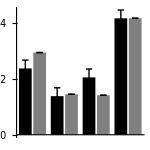
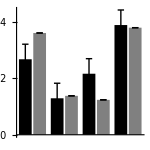
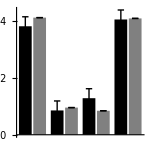
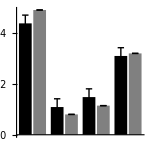
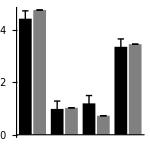
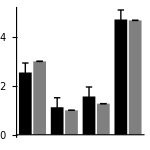
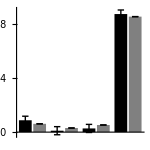
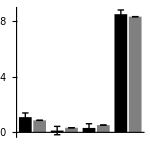
| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
ala-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
ala-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
arg-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
arg-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
asp-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
asp-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
cit | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
citr-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
glc-D | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
glc-D_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
gln-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
gln-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
glu-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
glu-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
gly | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
glyc3p | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
gly_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
mal-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
orn | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
ser-L | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
ser-L_EC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[
Table[
ErrorBarChart[
Transpose[{midsToFitMean⟦j,i⟧,fittedMIDs⟦j,i⟧}],
Table[{midsToFitSD⟦j,i⟧,0},{Length[midsToFitMean⟦j,i⟧]}],
PlotRange->{0,All},AspectRatio->1,ImageSize->150],
{i,Length[measuredMetNames]},{j,nGroups}],
TableHeadings->{measuredMetNames,expGroupNames}]
```

Scatter plot of all fitted MIDs

```mathematica
Table[
ListPlot[
Transpose[{Flatten[Mean/@midsToFit⟦All,i⟧],Flatten[fittedMIDs⟦i⟧]}],
PlotRange->{{0,1},{0,1}},AspectRatio->1],
{i,nGroups}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Fluxes at optimum

#### Flux tables

```mathematica
With[{i=1},
TableForm[
Transpose[{ForwardFlux[fluxGams⟦i⟧],ReverseFlux[fluxGams⟦i⟧],NetFlux[fluxGams⟦i⟧]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 187.607 | 0. | 187.607
<Reaction ACONTm(rev)> | 100000. | 99646.8 | 353.242
<Reaction ADK1> | 105.804 | 0. | 105.804
<Reaction AKGDm(rev)> | 479.41 | 89.349 | 390.061
<Reaction AKGtm(rev)> | 99413. | 100000. | -586.995
<Reaction ALATA_L(rev)> | 382.993 | 344.874 | 38.119
<Reaction ALAmix> | 115.311 | 0. | 115.311
<Reaction ALAtl> | 20.2245 | 0. | 20.2245
<Reaction ALAtin> | 80.6406 | 0. | 80.6406
<Reaction ALAtout> | 30.3823 | 0. | 30.3823
<Reaction ARGN> | 119.215 | 0. | 119.215
<Reaction ARGSL> | 105.804 | 0. | 105.804
<Reaction ARGSS> | 105.804 | 0. | 105.804
<Reaction ARGmix> | 41.5139 | 0. | 41.5139
<Reaction ARGtl> | 12.7505 | 0. | 12.7505
<Reaction ARGtin> | 12.7665 | 0. | 12.7665
<Reaction ARGtout> | 0.054799 | 0. | 0.054799
<Reaction ASPTA(rev)> | 100000. | 99271.8 | 728.241
<Reaction ASPTAm(rev)> | 823.465 | 0.001 | 823.464
<Reaction ASPtl> | 23.8544 | 0. | 23.8544
<Reaction ASPmix> | 32.8428 | 0. | 32.8428
<Reaction ASPtin> | 9.89195 | 0. | 9.89195
<Reaction ASPtout> | 0.847476 | 0. | 0.847476
<Reaction ASPtm(rev)> | 100000. | 99176.5 | 823.464
<Reaction ATPS4m> | 5039.19 | 0. | 5039.19
<Reaction ATPtm(rev)> | 4851.01 | 0.001 | 4851.01
<Reaction CBPSam> | 105.804 | 0. | 105.804
<Reaction ATPASES> | 1856.58 | 0. | 1856.58
<Reaction CO2tm(rev)> | 99495.5 | 100000. | -504.481
<Reaction CSm> | 353.242 | 0. | 353.242
<Reaction CYOOm> | 1106.79 | 0. | 1106.79
<Reaction CYOR-u10m> | 2213.57 | 0. | 2213.57
<Reaction ENO(rev)> | 100000. | 99978.8 | 21.2189
<Reaction ETF> | 104.673 | 0. | 104.673
<Reaction FAO16> | 14.9533 | 0. | 14.9533
<Reaction FAO14> | 14.9533 | 0. | 14.9533
<Reaction FAO12> | 14.9533 | 0. | 14.9533
<Reaction FAO10> | 14.9533 | 0. | 14.9533
<Reaction FAO8> | 14.9533 | 0. | 14.9533
<Reaction FAO6> | 14.9533 | 0. | 14.9533
<Reaction FAO4> | 14.9533 | 0. | 14.9533
<Reaction FBA(rev)> | 100000. | 99973.1 | 26.9163
<Reaction FBP> | 1529.73 | 0. | 1529.73
<Reaction FUMm> | 495.865 | 0. | 495.865
<Reaction FUMtm> | 105.804 | 0. | 105.804
<Reaction G3PD1> | 5.01089 | 0. | 5.01089
<Reaction G5SDxm> | 13.4108 | 0. | 13.4108
<Reaction G6PDH2r> | 455.287 | 0. | 455.287
<Reaction G6PPer> | 194.252 | 0. | 194.252
<Reaction G6Pter(rev)> | 194.253 | 0.001 | 194.252
<Reaction GAPD(rev)> | 100000. | 99799.4 | 200.584
<Reaction GHMT2r(rev)> | 99989.7 | 100000. | -10.3387
<Reaction GLCmix> | 938.464 | 0. | 938.464
<Reaction GLCtin> | 168.577 | 0. | 168.577
<Reaction GLCtout> | 194.252 | 0. | 194.252
<Reaction GLNmix> | 312.739 | 0. | 312.739
<Reaction GLNtin> | 63.8343 | 0. | 63.8343
<Reaction GLNtl> | 8.47258 | 0. | 8.47258
<Reaction GLNtout> | 16.1861 | 0. | 16.1861
<Reaction GLNtm(rev)> | 239.43 | 0.0300461 | 239.4
<Reaction GLNS> | 191.385 | 0. | 191.385
<Reaction GLUDxm(rev)> | 0.001 | 186.239 | -186.238
<Reaction GLUNm> | 239.4 | 0. | 239.4
<Reaction GLUtl> | 27.3289 | 0. | 27.3289
<Reaction GLUt2m(rev)> | 371.005 | 0.001 | 371.004
<Reaction GLUmix> | 65.0923 | 0. | 65.0923
<Reaction GLUtin> | 0.001 | 0. | 0.001
<Reaction GLUtout> | 29.4068 | 0. | 29.4068
<Reaction GLYtl> | 21.6745 | 0. | 21.6745
<Reaction GLYmix> | 109.893 | 0. | 109.893
<Reaction GLYtin> | 16.231 | 0. | 16.231
<Reaction GLYtout> | 5.08158 | 0. | 5.08158
<Reaction GLYCOGEN_BREAK> | 204.353 | 0. | 204.353
<Reaction GLYCPH> | 5.01089 | 0. | 5.01089
<Reaction GND> | 455.287 | 0. | 455.287
<Reaction H2Oter> | 194.252 | 0. | 194.252
<Reaction H2Otm(rev)> | 0.0262685 | 5760. | -5759.97
<Reaction HCO3Em> | 472.437 | 0. | 472.437
<Reaction HEX1> | 168.577 | 0. | 168.577
<Reaction Htm2(rev)> | 0.001 | 4492.98 | -4492.98
<Reaction ICDHxm(rev)> | 100000. | 99646.8 | 353.242
<Reaction LDH_L(rev)> | 60.7317 | 0.001 | 60.7307
<Reaction MALtm(rev)> | 314.209 | 0.001 | 314.208
<Reaction MDH(rev)> | 0.001 | 314.209 | -314.208
<Reaction MDHm(rev)> | 1739.51 | 929.437 | 810.073
<Reaction NADH2-u10m> | 1718.84 | 0. | 1718.84
<Reaction NADPH_REDOX> | 455.287 | 0. | 455.287
<Reaction NDPK1> | 414.034 | 0. | 414.034
<Reaction NH4tm(rev)> | 52.6436 | 0.001 | 52.6426
<Reaction O2tm> | 1106.79 | 0. | 1106.79
<Reaction ORNTArm> | 13.4108 | 0. | 13.4108
<Reaction OCBTm> | 105.804 | 0. | 105.804
<Reaction ORNtm> | 13.4108 | 0. | 13.4108
<Reaction ORNt4m> | 105.804 | 0. | 105.804
<Reaction PCm> | 366.633 | 0. | 366.633
<Reaction PDHm> | 233.615 | 0. | 233.615
<Reaction PEPCK> | 414.034 | 0. | 414.034
<Reaction PFK> | 1556.64 | 0. | 1556.64
<Reaction PGCD> | 179.365 | 0. | 179.365
<Reaction PGI(rev)> | 0.001 | 276.609 | -276.608
<Reaction PGK(rev)> | 100000. | 99799.4 | 200.584
<Reaction PGL> | 455.287 | 0. | 455.287
<Reaction PGM(rev)> | 100000. | 99978.8 | 21.2189
<Reaction PGMT> | 204.353 | 0. | 204.353
<Reaction PIt2m> | 4851.01 | 0. | 4851.01
<Reaction PIter> | 194.252 | 0. | 194.252
<Reaction PPA> | 105.804 | 0. | 105.804
<Reaction PMTtm> | 14.9533 | 0. | 14.9533
<Reaction PMTCOAT> | 14.9533 | 0. | 14.9533
<Reaction PROTDEG_ALA> | 20.2245 | 0. | 20.2245
<Reaction PROTDEG_ARG> | 12.7505 | 0. | 12.7505
<Reaction PROTDEG_ASP> | 23.8544 | 0. | 23.8544
<Reaction PROTDEG_GLN> | 8.47258 | 0. | 8.47258
<Reaction PROTDEG_GLU> | 27.3289 | 0. | 27.3289
<Reaction PROTDEG_GLY> | 21.6745 | 0. | 21.6745
<Reaction PROTDEG_SER> | 14.0969 | 0. | 14.0969
<Reaction PROTSYN_ALA> | 32.3637 | 0. | 32.3637
<Reaction PROTSYN_ARG> | 12.0514 | 0. | 12.0514
<Reaction PROTSYN_ASP> | 22.3172 | 0. | 22.3172
<Reaction PROTSYN_GLN> | 8.10606 | 0. | 8.10606
<Reaction PROTSYN_GLU> | 22.5292 | 0. | 22.5292
<Reaction PROTSYN_GLY> | 22.4853 | 0. | 22.4853
<Reaction PROTSYN_SER> | 14.4214 | 0. | 14.4214
<Reaction PROTSYN_ATP> | 272.006 | 0. | 272.006
<Reaction PSERT> | 179.365 | 0. | 179.365
<Reaction PSP_L> | 179.365 | 0. | 179.365
<Reaction PYK> | 435.253 | 0. | 435.253
<Reaction PYRt2m(rev)> | 600.249 | 0.001 | 600.248
<Reaction RPE> | 303.525 | 0. | 303.525
<Reaction RPI> | 151.762 | 0. | 151.762
<Reaction SERHL> | 187.607 | 0. | 187.607
<Reaction SERmix> | 63.5336 | 0. | 63.5336
<Reaction SERtl> | 14.0969 | 0. | 14.0969
<Reaction SERtin> | 16.9642 | 0. | 16.9642
<Reaction SERtout> | 18.7368 | 0. | 18.7368
<Reaction SUCD1m> | 390.061 | 0. | 390.061
<Reaction SUCOASm> | 390.061 | 0. | 390.061
<Reaction TALA> | 151.762 | 0. | 151.762
<Reaction TKT1> | 151.762 | 0. | 151.762
<Reaction TKT2> | 151.762 | 0. | 151.762
<Reaction TPI(rev)> | 1738.99 | 1717.09 | 21.9054

#### Boundary fluxes tables

```mathematica
TableForm[
Transpose[BoundaryFlux/@fluxGams],
TableHeadings->{BoundaryFluxNames[bnet],expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
ala-L_IN | 195.951 | 116.408 | 118.758 | 116.624 | 117.091 | 232.396
arg-L_IN | 54.2804 | 32.3476 | 32.3021 | 32.1768 | 31.2088 | 62.1204
asp-L_IN | 42.7347 | 25.4469 | 25.4631 | 25.4385 | 25.4787 | 50.9131
co2_IN | 98626.2 | 98655.9 | 98848.7 | 98774.4 | 98354.1 | 98366.9
glc-D_IN | 1107.04 | 676.742 | 691.351 | 602.418 | 512.572 | 1252.14
gln-L_IN | 376.574 | 224.587 | 226.077 | 227.584 | 228.935 | 452.289
glu-L_IN | 65.0933 | 38.1455 | 38.2678 | 38.5364 | 38.7154 | 76.7624
glycogen_IN | 204.353 | 191.119 | 271.889 | 291.672 | 307.657 | 232.356
gly_IN | 126.124 | 75.0732 | 75.0846 | 75.1273 | 74.001 | 150.487
h2o_IN | 0.001 | 0.001 | 0.001 | 0.001 | 0.257502 | 0.001
h_IN | 0.001 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
mlthf_IN | 27.9661 | 22.7484 | 42.1785 | 100000. | 1.64364 | 132.484
nh4_IN | 56.4222 | 0.001 | 0.001 | 0.001 | 0.001 | 0.001
o2_IN | 1562.07 | 1508.08 | 1231.77 | 1371.21 | 1709.59 | 1636.49
pmt_IN | 14.9533 | 16.495 | 8.83388 | 18.9763 | 8.04988 | 0.001
prot_ala_IN | 20.2245 | 27.5343 | 22.9169 | 22.6064 | 19.8267 | 22.4875
prot_arg_IN | 12.7505 | 12.2615 | 16.3352 | 16.1852 | 17.8936 | 25.2957
prot_asp_IN | 23.8544 | 23.5456 | 22.4321 | 23.8667 | 23.3285 | 23.394
prot_gln_IN | 8.47258 | 7.7653 | 7.37159 | 7.98952 | 8.08766 | 8.18572
prot_glu_IN | 27.3289 | 23.8945 | 26.0972 | 26.5867 | 25.5581 | 24.7844
prot_gly_IN | 21.6745 | 23.3296 | 19.8197 | 23.1614 | 21.4336 | 23.1469
prot_ser_IN | 14.0969 | 14.7649 | 13.5452 | 14.686 | 14.2717 | 14.8073
ser-L_IN | 80.4979 | 121.887 | 321.529 | 430.744 | 0.907413 | 168.729
thf_IN | 0.001 | 0.001 | 7.48076 | 0.0798698 | 5.78735 | 0.001
ala-L_OUT | 145.693 | 87.5066 | 118.975 | 101.59 | 117.993 | 206.697
arg-L_OUT | 41.5687 | 21.3145 | 16.8298 | 24.1423 | 27.4774 | 21.4752
asp-L_OUT | 33.6903 | 22.7365 | 20.3315 | 23.5099 | 20.2277 | 43.349
co2_OUT | 100000. | 100000. | 100000. | 100000. | 100000. | 100000.
glc-D_OUT | 1132.72 | 671.078 | 722.919 | 678.789 | 544.041 | 1267.85
gln-L_OUT | 328.925 | 176.353 | 209.403 | 205.569 | 185.952 | 390.335
glu-L_OUT | 94.499 | 58.5114 | 59.9562 | 63.7062 | 56.7504 | 102.995
glyc_OUT | 5.01089 | 3.08045 | 3.1467 | 4.75389 | 4.81738 | 4.73156
gly_OUT | 114.974 | 76.0986 | 78.7972 | 72.6604 | 74.8175 | 142.055
h2o_OUT | 692.879 | 615.072 | 416.537 | 430.558 | 772.76 | 692.754
h_OUT | 1055.16 | 1067.4 | 990.563 | 1019.93 | 1053.62 | 681.032
lac-L_OUT | 60.7307 | 109.491 | 155.05 | 140.966 | 66.6844 | 67.1171
mlthf_OUT | 17.6274 | 22.0863 | 49.6582 | 99997.9 | 7.42999 | 124.073
nh4_OUT | 0.001 | 3.18471 | 24.5099 | 27.8662 | 28.3977 | 216.344
prot_ala_OUT | 32.3637 | 30.3698 | 32.1614 | 36.2253 | 39.6118 | 35.2162
prot_arg_OUT | 12.0514 | 11.9634 | 10.809 | 11.9552 | 12.1112 | 12.3706
prot_asp_OUT | 22.3172 | 21.441 | 23.0773 | 23.9503 | 25.9597 | 23.1471
prot_gln_OUT | 8.10606 | 7.98145 | 8.23676 | 8.21388 | 8.45475 | 8.13993
prot_glu_OUT | 22.5292 | 21.4945 | 23.8398 | 24.36 | 26.645 | 23.3148
prot_gly_OUT | 22.4853 | 21.642 | 23.5868 | 23.54 | 26.4035 | 23.1685
prot_ser_OUT | 14.4214 | 14.0826 | 14.819 | 14.85 | 15.6302 | 14.7011
ser-L_OUT | 82.2705 | 124.409 | 321.347 | 428.494 | 1.61054 | 165.261
thf_OUT | 10.3397 | 0.663126 | 0.001 | 2.16823 | 0.001 | 8.41196
urea_OUT | 119.215 | 74.9567 | 29.0621 | 24.6324 | 24.926 | 64.9711

#### Comparison across groups

```mathematica
Length[Reactions[net]]
```

141

```mathematica
Block[{netFlux},
netFlux=Transpose[NetFlux/@fluxGams];
Table[
SimpleBarChart[netFlux⟦i⟧,PlotRange->All,PlotLabel->ReactionID[Reactions[net]⟦i⟧],ImageSize->120,AspectRatio->1],
{i,Length[Reactions[net]]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Fitted flux measurements

Uptake/release and specific measured (or literature) fluxes

```mathematica
fittedFluxes=Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
ix=ReindexList[measReactions,rl];
Table[
v=Join[EMUFluxMap[net][fluxGams⟦i⟧],BoundaryFlux[fluxGams⟦i⟧]];
fluxMixing.v⟦ix⟧,
{i,nGroups}]];
fittedFluxes//Dimensions
```

{6,36}

```mathematica
TableForm[
Flatten/@TransposeToFirst[
Table[
{fittedFluxes⟦i⟧,boundaryFlux⟦i,All,1⟧},
{i,nGroups}],3],
TableHeadings->{measuredBoundaryIds,Flatten[Outer[StringJoin,expGroupNames,{" fit"," meas"}]]}]
```

| L005 fit | L005 meas | L008 fit | L008 meas | L010 fit | L010 meas | L016 fit | L016 meas | L020_fasted fit | L020_fasted meas | L020_fed fit | L020_fed meas
meas_ala-L | -50.2583 | -20.5801 | -28.9014 | -17.7902 | 0.217792 | 1.76065 | -15.0348 | -11.0685 | 0.901374 | 1.21418 | -25.6993 | -25.1644
meas_ala-L_tot | 195.951 | 190.982 | 116.408 | 113.68 | 118.758 | 113.68 | 116.624 | 113.68 | 117.091 | 113.68 | 232.396 | 227.36
meas_arg-L | -12.7117 | -12.4918 | -11.0331 | -8.0829 | -15.4723 | -15.4673 | -8.03448 | -8.29496 | -3.73138 | -22.9542 | -40.6452 | -44.3099
meas_arg-L_tot | 54.2804 | 54.2691 | 32.3476 | 32.303 | 32.3021 | 32.303 | 32.1768 | 32.303 | 31.2088 | 32.303 | 62.1204 | 64.606
meas_asp-L | -9.04448 | -9.01105 | -2.71043 | -2.69869 | -5.13156 | -5.12774 | -1.92854 | -1.93634 | -5.25096 | -5.26635 | -7.56409 | -7.55991
meas_asp-L_tot | 42.7347 | 42.7345 | 25.4469 | 25.4372 | 25.4631 | 25.4372 | 25.4385 | 25.4372 | 25.4787 | 25.4372 | 50.9131 | 50.8744
meas_atpases | 1856.58 | 2166.67 | 1851.27 | 2166.67 | 1868.49 | 2166.67 | 2051.85 | 2166.67 | 2149.25 | 2166.67 | 2162.92 | 2166.67
meas_glc-D | 25.6749 | 26.2375 | -5.66355 | -5.622 | 31.5688 | 32.61 | 76.3714 | 75.339 | 31.4691 | 30.361 | 15.7119 | 15.742
meas_glc-D_tot | 1107.04 | 1040. | 676.742 | 619.048 | 691.351 | 619.048 | 602.418 | 619.048 | 512.572 | 619.048 | 1252.14 | 1238.1
meas_gln-L | -47.6482 | -47.0367 | -48.2338 | -45.8353 | -16.674 | -13.8731 | -22.0144 | -16.1411 | -42.9822 | -42.4842 | -61.954 | -61.583
meas_gln-L_tot | 376.574 | 378.182 | 224.587 | 225.108 | 226.077 | 225.108 | 227.584 | 225.108 | 228.935 | 225.108 | 452.289 | 450.216
meas_glu-L | 29.4058 | 31.5873 | 20.3659 | 21.344 | 21.6883 | 22.6452 | 25.1698 | 26.6069 | 18.035 | 18.0115 | 26.2326 | 26.4629
meas_glu-L_tot | 65.0933 | 64.2909 | 38.1455 | 38.2684 | 38.2678 | 38.2684 | 38.5364 | 38.2684 | 38.7154 | 38.2684 | 76.7624 | 76.5368
meas_gly | -11.1494 | -10.3426 | 1.0254 | 1.55876 | 3.71262 | 3.5892 | -2.46692 | -2.45657 | 0.816443 | -0.800331 | -8.43254 | -8.00394
meas_gly_tot | 126.124 | 126.124 | 75.0732 | 75.0736 | 75.0846 | 75.0736 | 75.1273 | 75.0736 | 74.001 | 75.0736 | 150.487 | 150.147
meas_lac-L | 60.7307 | 61.8455 | 109.491 | 115.82 | 155.05 | 159.673 | 140.966 | 140.558 | 66.6844 | 65.219 | 67.1171 | 67.468
meas_nadph_demand | 455.287 | 300. | 468.305 | 300. | 412.039 | 300. | 436.735 | 300. | 494.657 | 300. | 379.868 | 300.
meas_o2 | 1562.07 | 2500. | 1508.08 | 2500. | 1231.77 | 2500. | 1371.21 | 2500. | 1709.59 | 2500. | 1636.49 | 2500.
meas_protdeg_ala | 20.2245 | 36.58 | 27.5343 | 36.58 | 22.9169 | 36.58 | 22.6064 | 36.58 | 19.8267 | 36.58 | 22.4875 | 36.58
meas_protdeg_arg | 12.7505 | 12.98 | 12.2615 | 12.98 | 16.3352 | 12.98 | 16.1852 | 12.98 | 17.8936 | 12.98 | 25.2957 | 12.98
meas_protdeg_asp | 23.8544 | 23.6 | 23.5456 | 23.6 | 22.4321 | 23.6 | 23.8667 | 23.6 | 23.3285 | 23.6 | 23.394 | 23.6
meas_protdeg_gln | 8.47258 | 8.26 | 7.7653 | 8.26 | 7.37159 | 8.26 | 7.98952 | 8.26 | 8.08766 | 8.26 | 8.18572 | 8.26
meas_protdeg_glu | 27.3289 | 24.19 | 23.8945 | 24.19 | 26.0972 | 24.19 | 26.5867 | 24.19 | 25.5581 | 24.19 | 24.7844 | 24.19
meas_protdeg_gly | 21.6745 | 23.305 | 23.3296 | 23.305 | 19.8197 | 23.305 | 23.1614 | 23.305 | 21.4336 | 23.305 | 23.1469 | 23.305
meas_protdeg_ser | 14.0969 | 14.75 | 14.7649 | 14.75 | 13.5452 | 14.75 | 14.686 | 14.75 | 14.2717 | 14.75 | 14.8073 | 14.75
meas_protsyn_ala | 32.3637 | 36.58 | 30.3698 | 36.58 | 32.1614 | 36.58 | 36.2253 | 36.58 | 39.6118 | 36.58 | 35.2162 | 36.58
meas_protsyn_arg | 12.0514 | 12.98 | 11.9634 | 12.98 | 10.809 | 12.98 | 11.9552 | 12.98 | 12.1112 | 12.98 | 12.3706 | 12.98
meas_protsyn_asp | 22.3172 | 23.6 | 21.441 | 23.6 | 23.0773 | 23.6 | 23.9503 | 23.6 | 25.9597 | 23.6 | 23.1471 | 23.6
meas_protsyn_atp | 272.006 | 295. | 271.613 | 295. | 272.89 | 295. | 286.487 | 295. | 293.709 | 295. | 294.722 | 295.
meas_protsyn_gln | 8.10606 | 8.26 | 7.98145 | 8.26 | 8.23676 | 8.26 | 8.21388 | 8.26 | 8.45475 | 8.26 | 8.13993 | 8.26
meas_protsyn_glu | 22.5292 | 24.19 | 21.4945 | 24.19 | 23.8398 | 24.19 | 24.36 | 24.19 | 26.645 | 24.19 | 23.3148 | 24.19
meas_protsyn_gly | 22.4853 | 23.305 | 21.642 | 23.305 | 23.5868 | 23.305 | 23.54 | 23.305 | 26.4035 | 23.305 | 23.1685 | 23.305
meas_protsyn_ser | 14.4214 | 14.75 | 14.0826 | 14.75 | 14.819 | 14.75 | 14.85 | 14.75 | 15.6302 | 14.75 | 14.7011 | 14.75
meas_ser-L | 1.77259 | 1.7778 | 2.52235 | 2.54013 | -0.18219 | -0.186258 | -2.24965 | -2.2805 | 0.703127 | 0.691824 | -3.46863 | -3.44604
meas_urea | 119.215 | 125.666 | 74.9567 | 78.4195 | 29.0621 | 77.8912 | 24.6324 | 100. | 24.926 | 100. | 64.9711 | 100.
meas_VLDL_TAG | 5.01089 | 5.01164 | 3.08045 | 3.08242 | 3.1467 | 3.14685 | 4.75389 | 4.75 | 4.81738 | 4.75 | 4.73156 | 4.75

```mathematica
Table[
ErrorBarChart[
Transpose[{boundaryFlux⟦All,j,1⟧,fittedFluxes⟦All,j⟧}],
Thread[{boundaryFlux⟦All,j,2⟧,0}],
PlotRange->All,AspectRatio->1,PlotLabel->measuredBoundaryIds⟦j⟧],
{j,Length[measuredBoundaryIds]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

All constrained fluxes (fitted fluxes are linear combinations of these)

```mathematica
(*Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
TableForm[v⟦ix⟧,TableHeadings->{measReactions}]]*)
```

#### Metabolite balances

This does not show boundary reactions

```mathematica
Block[{i=2,rids,mids,v},
rids=ReactionID/@Reactions[net];
mids=MetaboliteShortName/@Metabolites[net];
v=NetFlux[fluxGams⟦i⟧];
TableForm[
Table[
(part@(Stoichiometry[net]⟦j⟧*v)).rids,
{j,Length[mids]},{part,{PositivePart,NegativePart}}],
TableHeadings->{mids,{expGroupNames⟦2⟧}}]]
```

| L008 | 
13dpg_c | 228.377 GAPD | 228.377 PGK
2amac_c | 109.54 SERHL | 109.54 2AMACHYD
2pg_c | 117.126 PGM | 117.126 ENO
3pg_c | 228.377 PGK | 111.251 PGCD+117.126 PGM
3php_c | 111.251 PGCD | 111.251 PSERT
6pgc_c | 458.36 PGL | 458.36 GND
6pgl_c | 458.36 G6PDH2r | 458.36 PGL
accoa_m | 15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+30.6801 FAO4+15.3401 FAO6+15.3401 FAO8+188.702 PDHm | 311.423 CSm
adp_c | 127.614 ADK1+1878.64 ATPASES+162.622 HEX1+453.273 NDPK1+1397.35 PFK+1094.57 PROTSYN_ATP | 4315.29 ATPtm+228.377 PGK+570.399 PYK
adp_m | 4315.29 ATPtm+127.614 CBPSam+408.163 PCm | 4498.13 ATPS4m+352.935 SUCOASm
akg_c | 595.496 AKGtm+111.251 PSERT | 26.5987 ALATA_L+680.148 ASPTA
akg_m | 740.357 ASPTAm+311.423 ICDHxm | 352.935 AKGDm+595.496 AKGtm+92.1715 GLUDxm+11.1771 ORNTArm
ala-L_c | 50.1123 ALAtin+27.7813 ALAtl | 26.5987 ALATA_L+20.9161 ALAtout+30.3788 PROTSYN_ALA
ala-L_e | 66.4336 ALAmix+20.9161 ALAtout | 0
ala-L_l | 27.7813 PROTDEG_ALA | 27.7813 ALAtl
ala-L_v | 0 | 66.4336 ALAmix+50.1123 ALAtin
amp_c | 63.8069 ARGSS | 63.8069 ADK1
arg-L_c | 63.8069 ARGSL+11.199 ARGtin+12.2173 ARGtl | 74.984 ARGN+0.202727 ARGtout+12.0365 PROTSYN_ARG
arg-L_e | 21.1483 ARGmix+0.202727 ARGtout | 0
arg-L_l | 12.2173 PROTDEG_ARG | 12.2173 ARGtl
arg-L_v | 0 | 21.1483 ARGmix+11.199 ARGtin
argsuc_c | 63.8069 ARGSS | 63.8069 ARGSL
asp-L_c | 4.47997 ASPtin+22.4166 ASPtl+740.357 ASPtm | 63.8069 ARGSS+680.148 ASPTA+1.77311 ASPtout+21.5252 PROTSYN_ASP
asp-L_e | 20.9579 ASPmix+1.77311 ASPtout | 0
asp-L_l | 22.4166 PROTDEG_ASP | 22.4166 ASPtl
asp-L_m | 740.357 ASPTAm | 740.357 ASPtm
asp-L_v | 0 | 20.9579 ASPmix+4.47997 ASPtin
atp_c | 4315.29 ATPtm+228.377 PGK+570.399 PYK | 63.8069 ADK1+63.8069 ARGSS+1878.64 ATPASES+162.622 HEX1+453.273 NDPK1+1397.35 PFK+1094.57 PROTSYN_ATP
atp_m | 4498.13 ATPS4m+352.935 SUCOASm | 4315.29 ATPtm+127.614 CBPSam+408.163 PCm
btcoa_m | 15.3401 FAO6 | 15.3401 FAO4
cbp_m | 63.8069 CBPSam | 63.8069 OCBTm
cit_m | 311.423 CSm | 311.423 ACONTm
citr-L_c | 63.8069 ORNt4m | 63.8069 ARGSS
citr-L_m | 63.8069 OCBTm | 63.8069 ORNt4m
co2_c | 381.091 CO2tm+458.36 GND+453.273 PEPCK | 0
co2_m | 352.935 AKGDm+311.423 ICDHxm+188.702 PDHm | 381.091 CO2tm+471.97 HCO3Em
coa_m | 311.423 CSm+352.935 SUCOASm | 352.935 AKGDm+15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8+188.702 PDHm+15.3401 PMTCOAT
dcacoa_m | 15.3401 FAO12 | 15.3401 FAO10
ddcacoa_m | 15.3401 FAO14 | 15.3401 FAO12
dhap_c | 39.3353 FBA | 3.08055 G3PD1+36.2547 TPI
e4p_c | 152.787 TALA | 152.787 TKT2
f6p_c | 1358.01 FBP+152.787 TALA+152.787 TKT2 | 1397.35 PFK+266.238 PGI
fadh2_m | 15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8 | 107.381 ETF
fad_m | 107.381 ETF | 15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8
fdp_c | 1397.35 PFK | 39.3353 FBA+1358.01 FBP
ficytC_m | 3966.76 CYOOm | 3966.76 CYOR-u10m
focytC_m | 3966.76 CYOR-u10m | 3966.76 CYOOm
fum_c | 63.8069 ARGSL | 63.8069 FUMtm
fum_m | 63.8069 FUMtm+352.935 SUCD1m | 416.742 FUMm
g1p_c | 186.459 GLYCOGEN_BREAK | 186.459 PGMT
g3p_c | 39.3353 FBA+152.787 TKT1+152.787 TKT2+36.2547 TPI | 228.377 GAPD+152.787 TALA
g6p_c | 162.622 HEX1+266.238 PGI+186.459 PGMT | 458.36 G6PDH2r+156.96 G6Pter
g6p_r | 156.96 G6Pter | 156.96 G6PPer
gdp_c | 453.273 PEPCK | 453.273 NDPK1
glc-D_c | 162.622 GLCtin | 162.622 HEX1
glc-D_e | 512.289 GLCmix+156.96 GLCtout | 0
glc-D_r | 156.96 G6PPer | 156.96 GLCtout
glc-D_v | 0 | 512.289 GLCmix+162.622 GLCtin
gln-L_c | 225.763 GLNtin+8.07869 GLNtl | 47.7544 GLNtm+178.003 GLNtout+8.0844 PROTSYN_GLN
gln-L_e | 0.001 GLNmix+178.003 GLNtout | 0
gln-L_l | 8.07869 PROTDEG_GLN | 8.07869 GLNtl
gln-L_m | 47.7544 GLNtm | 47.7544 GLUNm
gln-L_v | 0 | 0.001 GLNmix+225.763 GLNtin
glu5sa_m | 11.1771 ORNTArm | 11.1771 G5SDxm
glu-L_c | 26.5987 ALATA_L+680.148 ASPTA+0.001 GLUtin+24.3238 GLUtl | 578.077 GLUt2m+20.2564 GLUtout+21.4877 PROTSYN_GLU+111.251 PSERT
glu-L_e | 38.1756 GLUmix+20.2564 GLUtout | 0
glu-L_l | 24.3238 PROTDEG_GLU | 24.3238 GLUtl
glu-L_m | 11.1771 G5SDxm+92.1715 GLUDxm+47.7544 GLUNm+578.077 GLUt2m+11.1771 ORNTArm | 740.357 ASPTAm
glu-L_v | 0 | 38.1756 GLUmix+0.001 GLUtin
gly_c | 4.76888 GLYtin+23.0901 GLYtl | 0.268363 GHMT2r+5.83221 GLYtout+21.7584 PROTSYN_GLY
glyc3p_c | 3.08055 G3PD1 | 3.08055 GLYCPH
glyc_c | 3.08055 GLYCPH | 0
glycogen_c | 0 | 186.459 GLYCOGEN_BREAK
gly_e | 70.3042 GLYmix+5.83221 GLYtout | 0
gly_l | 23.0901 PROTDEG_GLY | 23.0901 GLYtl
gly_v | 0 | 70.3042 GLYmix+4.76888 GLYtin
gtp_c | 453.273 NDPK1 | 453.273 PEPCK
h2o_c | 117.126 ENO+5207.23 H2Otm+458.36 NADPH_REDOX+109.54 SERHL | 109.54 2AMACHYD+74.984 ARGN+1878.64 ATPASES+1358.01 FBP+0.268363 GHMT2r+3.08055 GLYCPH+156.96 H2Oter+458.36 PGL+63.8069 PPA+1094.57 PROTSYN_ATP+111.251 PSP_L
h2o_m | 4498.13 ATPS4m+1983.38 CYOOm+92.1715 GLUDxm | 311.423 CSm+15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8+416.742 FUMm+11.1771 G5SDxm+47.7544 GLUNm+5207.23 H2Otm+471.97 HCO3Em
h2o_r | 156.96 H2Oter | 156.96 G6PPer
h_c | 63.8069 ARGSS+1878.64 ATPASES+458.36 G6PDH2r+228.377 GAPD+162.622 HEX1+1397.35 PFK+111.251 PGCD+458.36 PGL+63.8069 PPA+1094.57 PROTSYN_ATP | 3.08055 G3PD1+3957.04 Htm2+109.672 LDH_L+226.875 MDH+570.399 PYK
hco3_m | 471.97 HCO3Em | 63.8069 CBPSam+408.163 PCm
hexcoa_m | 15.3401 FAO8 | 15.3401 FAO6
h_ims_m | 3966.76 CYOOm+7933.51 CYOR-u10m+6092.25 NADH2-u10m | 17992.5 ATPS4m
h_m | 13494.4 ATPS4m+127.614 CBPSam+311.423 CSm+15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8+22.3542 G5SDxm+471.97 HCO3Em+3957.04 Htm2+643.617 MDHm+63.8069 OCBTm+408.163 PCm | 7933.51 CYOOm+3966.76 CYOR-u10m+92.1715 GLUDxm+7615.32 NADH2-u10m
icit_m | 311.423 ACONTm | 311.423 ICDHxm
lac-L_c | 109.672 LDH_L | 0
mal-L_c | 226.875 MDH | 226.875 MALtm
mal-L_m | 416.742 FUMm+226.875 MALtm | 643.617 MDHm
mlthf_c | 0 | 0.268363 GHMT2r
nad_c | 3.08055 G3PD1+109.672 LDH_L+226.875 MDH | 228.377 GAPD+111.251 PGCD
nadh_c | 228.377 GAPD+111.251 PGCD | 3.08055 G3PD1+109.672 LDH_L+226.875 MDH
nadh_m | 352.935 AKGDm+15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8+11.1771 G5SDxm+311.423 ICDHxm+643.617 MDHm+188.702 PDHm | 92.1715 GLUDxm+1523.06 NADH2-u10m
nad_m | 92.1715 GLUDxm+1523.06 NADH2-u10m | 352.935 AKGDm+15.3401 FAO10+15.3401 FAO12+15.3401 FAO14+15.3401 FAO16+15.3401 FAO4+15.3401 FAO6+15.3401 FAO8+11.1771 G5SDxm+311.423 ICDHxm+643.617 MDHm+188.702 PDHm
nadp_c | 916.72 NADPH_REDOX | 458.36 G6PDH2r+458.36 GND
nadph_c | 458.36 G6PDH2r+458.36 GND | 916.72 NADPH_REDOX
nh4_c | 109.54 2AMACHYD | 108.224 NH4tm
nh4_m | 47.7544 GLUNm+108.224 NH4tm | 63.8069 CBPSam+92.1715 GLUDxm
o2_c | 0 | 458.36 NADPH_REDOX+991.689 O2tm
o2_m | 991.689 O2tm | 991.689 CYOOm
oaa_c | 680.148 ASPTA | 226.875 MDH+453.273 PEPCK
oaa_m | 643.617 MDHm+408.163 PCm | 740.357 ASPTAm+311.423 CSm
occoa_m | 15.3401 FAO10 | 15.3401 FAO8
orn_c | 74.984 ARGN | 63.8069 ORNt4m+11.1771 ORNtm
orn_m | 63.8069 ORNt4m+11.1771 ORNtm | 63.8069 OCBTm+11.1771 ORNTArm
pep_c | 117.126 ENO+453.273 PEPCK | 570.399 PYK
pi_c | 1878.64 ATPASES+1358.01 FBP+3.08055 GLYCPH+156.96 PIter+127.614 PPA+1094.57 PROTSYN_ATP+111.251 PSP_L | 228.377 GAPD+186.459 GLYCOGEN_BREAK+4315.29 PIt2m
pi_m | 63.8069 CBPSam+63.8069 OCBTm+408.163 PCm+4315.29 PIt2m | 4498.13 ATPS4m+352.935 SUCOASm
pi_r | 156.96 G6PPer | 156.96 PIter
pmt_c | 0 | 15.3401 PMTtm
pmtcoa_m | 15.3401 PMTCOAT | 15.3401 FAO16
pmt_m | 15.3401 PMTtm | 15.3401 PMTCOAT
ppi_c | 63.8069 ARGSS | 63.8069 PPA
prot_ala_c | 30.3788 PROTSYN_ALA | 0
prot_ala_l | 0 | 27.7813 PROTDEG_ALA
prot_arg_c | 12.0365 PROTSYN_ARG | 0
prot_arg_l | 0 | 12.2173 PROTDEG_ARG
prot_asp_c | 21.5252 PROTSYN_ASP | 0
prot_asp_l | 0 | 22.4166 PROTDEG_ASP
prot_gln_c | 8.0844 PROTSYN_GLN | 0
prot_gln_l | 0 | 8.07869 PROTDEG_GLN
prot_glu_c | 21.4877 PROTSYN_GLU | 0
prot_glu_l | 0 | 24.3238 PROTDEG_GLU
prot_gly_c | 21.7584 PROTSYN_GLY | 0
prot_gly_l | 0 | 23.0901 PROTDEG_GLY
prot_ser_c | 14.1285 PROTSYN_SER | 0
prot_ser_l | 0 | 14.6725 PROTDEG_SER
pser-L_c | 111.251 PSERT | 111.251 PSP_L
pyr_c | 109.54 2AMACHYD+26.5987 ALATA_L+570.399 PYK | 109.672 LDH_L+596.865 PYRt2m
pyr_m | 596.865 PYRt2m | 408.163 PCm+188.702 PDHm
q10h2_m | 107.381 ETF+1523.06 NADH2-u10m+352.935 SUCD1m | 1983.38 CYOR-u10m
q10_m | 1983.38 CYOR-u10m | 107.381 ETF+1523.06 NADH2-u10m+352.935 SUCD1m
r5p_c | 152.787 RPI | 152.787 TKT1
ru5p-D_c | 458.36 GND | 305.573 RPE+152.787 RPI
s7p_c | 152.787 TKT1 | 152.787 TALA
ser-L_c | 0.268363 GHMT2r+111.251 PSP_L+25.1436 SERtin+14.6725 SERtl | 14.1285 PROTSYN_SER+109.54 SERHL+27.6672 SERtout
ser-L_e | 91.2648 SERmix+27.6672 SERtout | 0
ser-L_l | 14.6725 PROTDEG_SER | 14.6725 SERtl
ser-L_v | 0 | 91.2648 SERmix+25.1436 SERtin
succ_m | 352.935 SUCOASm | 352.935 SUCD1m
succoa_m | 352.935 AKGDm | 352.935 SUCOASm
tdcoa_m | 15.3401 FAO16 | 15.3401 FAO14
thf_c | 0.268363 GHMT2r | 0
urea_c | 74.984 ARGN | 0
xu5p-D_c | 305.573 RPE | 152.787 TKT1+152.787 TKT2

### MID errors

```mathematica
midChi=Table[
(fittedMIDs⟦i⟧-Mean/@midsToFit⟦All,i⟧)/Map[Max[StandardDeviation[#],minSD]&,midsToFit⟦All,i⟧],
{i,nGroups}];
```

```mathematica
With[{i=1},
TableForm[midChi⟦i⟧,TableHeadings->{measuredMetNames,None}]]
```

ala-L | 1.90143 | 0.223467 | -2.14024 | 0.015348 |  |  | 
ala-L_EC | -0.877451 | 0.665826 | 0.84996 | -0.638334 |  |  | 
arg-L | 0.973013 | 0.185035 | -0.168725 | 0.00301835 | 0.141392 | 2.05659 | -3.19032
arg-L_EC | -0.233093 | -0.0390862 | -0.00123928 | 0.000663647 | 0.0269334 | 0.582774 | -0.336952
asp-L | 0.0348848 | 0.333902 | -0.87479 | 1.21415 | -0.708143 |  | 
asp-L_EC | 0.180627 | -0.373581 | 0.0373087 | 0.136001 | 0.0196443 |  | 
cit | -0.773135 | 1.22826 | -0.761857 | 0.392015 | -0.367247 | 0.423489 | -0.141528
citr-L | -1.0433 | 1.17585 | 0.0366501 | 0.01643 | 0.784065 | -1.19266 | 0.222969
glc-D | 1.02455 | 0.286604 | -0.545192 | -0.455001 | -0.311538 | -0.421681 | 0.422256
glc-D_EC | 0.53112 | 0.337024 | 0.0267664 | 0.468934 | 0.129927 | -0.0535256 | -1.44025
gln-L | 0.0208638 | 1.0931 | -1.26798 | 0.286843 | -0.0699944 | -0.062832 | 
gln-L_EC | -0.357336 | -0.0421888 | -0.291286 | -0.0750677 | 0.590437 | 0.175441 | 
glu-L | 0.025039 | 1.43064 | -1.22676 | -0.0584015 | 0.158835 | -0.329353 | 
glu-L_EC | -0.563918 | 1.11394 | -0.965202 | -0.0147239 | 0.810446 | -0.380542 | 
gly | 0.221237 | -0.82383 | 0.602593 |  |  |  | 
glyc3p | -0.340178 | 1.74921 | -2.80607 | 1.39704 |  |  | 
gly_EC | -0.459918 | 0.657559 | -0.197641 |  |  |  | 
mal-L | -0.224678 | 0.846645 | -2.08874 | 0.370381 | 1.09639 |  | 
orn | -0.135177 | 0.0867557 | 0.0186275 | 0.0149729 | 0.337254 | -0.322433 | 
ser-L | -0.00940909 | -0.13411 | 0.0346206 | 0.108899 |  |  | 
ser-L_EC | -0.0462301 | -0.0500655 | 0.0977702 | -0.00147456 |  |  |

```mathematica
Length/@Flatten/@midChi
```

{113,113,113,113,113,113}

```mathematica
Length[measuredMetNames]
```

21

Chi square = sum of squared residuals

```mathematica
With[{i=3},TableForm[midChi⟦i⟧^2,TableHeadings->{measuredMetNames,None}]]
```

ala-L | 0.828442 | 0.0904061 | 1.74906 | 0.0124673 |  |  | 
ala-L_EC | 0.112048 | 0.329426 | 0.388556 | 0.744016 |  |  | 
arg-L | 0.0119476 | 0.0074074 | 0.0632736 | 8.06261×10^-6 | 0.0138584 | 0.169268 | 0.0661531
arg-L_EC | 0.107823 | 0.00303114 | 5.99708×10^-7 | 4.47788×10^-7 | 0.000815266 | 0.319084 | 0.0440593
asp-L | 0.0134347 | 0.581345 | 1.51389 | 0.0230406 | 0.186675 |  | 
asp-L_EC | 0.214563 | 0.616373 | 0.0325287 | 0.00245291 | 0.00846403 |  | 
cit | 4.91543 | 0.391637 | 0.105576 | 0.0256821 | 0.0210321 | 1.66734 | 0.0016114
citr-L | 0.734508 | 0.710035 | 0.000786077 | 0.000171884 | 0.393533 | 0.453692 | 0.000380084
glc-D | 1.67473 | 0.00253305 | 0.909134 | 0.394805 | 0.0453743 | 0.0617393 | 0.639236
glc-D_EC | 0.479705 | 0.069721 | 0.00642442 | 0.211782 | 0.0492922 | 0.000126673 | 2.46482
gln-L | 0.831705 | 0.43579 | 1.64738 | 0.0587743 | 0.00472446 | 0.000508499 | 
gln-L_EC | 0.0153026 | 0.0112974 | 0.0510172 | 0.00478075 | 0.301527 | 0.0560208 | 
glu-L | 0.747881 | 1.03451 | 0.907984 | 0.0647287 | 0.0238353 | 0.687232 | 
glu-L_EC | 0.452893 | 1.25033 | 0.445139 | 0.0309972 | 0.44492 | 0.072353 | 
gly | 0.456819 | 1.06495 | 0.126794 |  |  |  | 
glyc3p | 0.0812142 | 1.92643 | 3.27579 | 0.499762 |  |  | 
gly_EC | 0.192388 | 0.504416 | 0.0737676 |  |  |  | 
mal-L | 0.385789 | 0.5642 | 2.9786 | 0.161841 | 0.57139 |  | 
orn | 0.0183338 | 0.0258419 | 0.000363511 | 0.000255972 | 0.00502135 | 0.0172339 | 
ser-L | 1.83012×10^-6 | 0.0279129 | 0.0024803 | 0.0140711 |  |  | 
ser-L_EC | 1.52995 | 0.0324415 | 1.51416 | 0.0301766 |  |  |

### Flux errors

Flux errors (positive if fitted is higher than measured)

```mathematica
fluxChi=Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
ix=ReindexList[measReactions,rl];
Table[
v=Join[EMUFluxMap[net][fluxGams⟦i⟧],BoundaryFlux[fluxGams⟦i⟧]];
(fluxMixing.v⟦ix⟧-boundaryFlux⟦i,All,1⟧)/boundaryFlux⟦i,All,2⟧,
{i,nGroups}]];
```

```mathematica
fluxChi//Dimensions
```

{6,36}

```mathematica
TableForm[Transpose[fluxChi],TableHeadings->{measuredBoundaryIds,expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
meas_ala-L | -1.60427 | -1.14882 | -0.429234 | -0.532792 | -0.108456 | -0.17291
meas_ala-L_tot | 0.260201 | 0.239972 | 0.446652 | 0.259004 | 0.300067 | 0.221499
meas_arg-L | -0.278316 | -1.2276 | -0.025501 | 0.179211 | 2.06495 | 1.12496
meas_arg-L_tot | 0.00208429 | 0.0138063 | -0.000286847 | -0.0390687 | -0.338728 | -0.38473
meas_asp-L | -0.0295269 | -0.0267851 | -0.0144739 | 0.00615742 | 0.0108057 | -0.0107784
meas_asp-L_tot | 0.000054218 | 0.00382696 | 0.0101828 | 0.000503747 | 0.0163111 | 0.00761416
meas_atpases | -0.477061 | -0.485233 | -0.458737 | -0.176634 | -0.0267898 | -0.00575924
meas_glc-D | -0.214423 | 0.0739018 | -0.319275 | 0.137033 | 0.364968 | -0.0191111
meas_glc-D_tot | 0.644625 | 0.931978 | 1.16796 | -0.268639 | -1.71999 | 0.113451
meas_gln-L | -0.0451913 | -0.292354 | -0.208942 | -0.476763 | -0.0985731 | -0.10656
meas_gln-L_tot | -0.042532 | -0.0231392 | 0.0430634 | 0.109975 | 0.169993 | 0.0460538
meas_glu-L | -0.403154 | -0.186315 | -0.0793695 | -0.148292 | 0.0151822 | -0.0769605
meas_glu-L_tot | 0.124802 | -0.0321217 | -0.000144844 | 0.0700339 | 0.116816 | 0.0294704
meas_gly | -0.116138 | -0.134551 | 0.0239972 | -0.00151654 | 0.428582 | -0.0685625
meas_gly_tot | -0.0000305779 | -0.0000483371 | 0.00145999 | 0.00715593 | -0.142869 | 0.0226516
meas_lac-L | -0.180253 | -0.546468 | -0.289541 | 0.0290204 | 0.224693 | -0.0520138
meas_nadph_demand | 1.03525 | 1.12204 | 0.746926 | 0.911564 | 1.29772 | 0.53245
meas_o2 | -1.87586 | -1.98384 | -2.53645 | -2.25759 | -1.58082 | -1.72703
meas_protdeg_ala | -1.49039 | -0.824287 | -1.24505 | -1.27334 | -1.52664 | -1.28417
meas_protdeg_arg | -0.0589413 | -0.184514 | 0.861625 | 0.823109 | 1.26183 | 3.16274
meas_protdeg_asp | 0.0359257 | -0.00768003 | -0.164953 | 0.0376744 | -0.0383438 | -0.0290902
meas_protdeg_gln | 0.0857865 | -0.199638 | -0.358519 | -0.109154 | -0.0695462 | -0.0299769
meas_protdeg_glu | 0.432539 | -0.0407142 | 0.262804 | 0.330266 | 0.188523 | 0.0819136
meas_protdeg_gly | -0.23321 | 0.00351315 | -0.498512 | -0.0205397 | -0.267663 | -0.0226138
meas_protdeg_ser | -0.147591 | 0.00337275 | -0.272275 | -0.0144744 | -0.108091 | 0.012941
meas_protsyn_ala | -0.384207 | -0.565904 | -0.402642 | -0.0323214 | 0.276273 | -0.124274
meas_protsyn_arg | -0.238463 | -0.261067 | -0.557524 | -0.263179 | -0.223113 | -0.156488
meas_protsyn_asp | -0.181188 | -0.304942 | -0.0738303 | 0.0494708 | 0.333296 | -0.0639757
meas_protsyn_atp | -0.259815 | -0.264265 | -0.249835 | -0.0961977 | -0.0145901 | -0.00313657
meas_protsyn_gln | -0.0621227 | -0.112407 | -0.0093793 | -0.0186128 | 0.0785935 | -0.0484535
meas_protsyn_glu | -0.228855 | -0.371436 | -0.0482595 | 0.0234312 | 0.338297 | -0.120595
meas_protsyn_gly | -0.117246 | -0.237855 | 0.0403051 | 0.033606 | 0.443188 | -0.0195275
meas_protsyn_ser | -0.0742544 | -0.150823 | 0.0156001 | 0.022604 | 0.198915 | -0.0110494
meas_ser-L | -0.00934774 | -0.0246142 | 0.00378718 | 0.0125526 | 0.0225407 | -0.00750991
meas_urea | -0.411949 | -0.443084 | -2.61939 | -1.50735 | -1.50148 | -0.700579
meas_VLDL_TAG | -0.00531551 | -0.0102561 | -0.00225856 | 0.0020595 | 0.0356497 | -0.00975404

```mathematica
measuredBoundaryIds
```

{meas_ala-L,meas_ala-L_tot,meas_arg-L,meas_arg-L_tot,meas_asp-L,meas_asp-L_tot,meas_atpases,meas_glc-D,meas_glc-D_tot,meas_gln-L,meas_gln-L_tot,meas_glu-L,meas_glu-L_tot,meas_gly,meas_gly_tot,meas_lac-L,meas_nadph_demand,meas_o2,meas_protdeg_ala,meas_protdeg_arg,meas_protdeg_asp,meas_protdeg_gln,meas_protdeg_glu,meas_protdeg_gly,meas_protdeg_ser,meas_protsyn_ala,meas_protsyn_arg,meas_protsyn_asp,meas_protsyn_atp,meas_protsyn_gln,meas_protsyn_glu,meas_protsyn_gly,meas_protsyn_ser,meas_ser-L,meas_urea,meas_VLDL_TAG}

```mathematica
{Max[fluxChi],Min[fluxChi]}
```

{3.16274,-2.61939}

### Q-Q plots (Suppl Fig 4b)

#### MIDs

```mathematica
{Min[#],Max[#]}&[midChi]
```

{-3.19032,2.09278}

```mathematica
Table[
QQPlot[Flatten[midChi⟦i⟧],PlotRange->{{-3.5,3.5},{-3.5,3.5}},PlotLabel->expGroupNames⟦i⟧,AspectRatio->1,ImageSize->180],
{i,nGroups}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

With label tooltips

```mathematica
Table[
QQPlot[
Flatten[midChi⟦i⟧],
Flatten[Table[measuredMetNames⟦j⟧,{j,Length[measuredMetNames]},{Length[midChi⟦1,j⟧]}]],
PlotRange->{{-3.5,3.5},{-3.5,3.5}},PlotLabel->expGroupNames⟦i⟧,AspectRatio->1,ImageSize->180],
{i,nGroups}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Fluxes

```mathematica
Table[
QQPlot[
fluxChi⟦i⟧,measuredBoundaryIds,
PlotRange->{{-4,4},{-4,4}},PlotLabel->expGroupNames⟦i⟧,AspectRatio->1,ImageSize->180],
{i,nGroups}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### MID and fluxes combined (Suppl Fig 4b)

```mathematica
{Min[#],Max[#]}&[Flatten[{midChi,fluxChi}]]
```

{-3.19032,3.16274}

```mathematica
allChi=Table[Join[Flatten[midChi⟦i⟧],fluxChi⟦i⟧],{i,nGroups}];
```

```mathematica
With[{maxChi=4},
Table[
QQPlot[
allChi⟦i⟧,
PlotRange->{{-maxChi,maxChi},{-maxChi,maxChi}},PlotLabel->expGroupNames⟦i⟧,AspectRatio->1,ImageSize->180],
{i,nGroups}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Source data

```mathematica
Last/@QQData[First[allChi]]//TableForm
```

```mathematica
Transpose[Sort/@Most[allChi]]//TableForm
```

### Total and expected chi2 (assess model fit; numbers added to Suppl Fig 4b)

Total chi^2

```mathematica
TableForm[
{Total/@Flatten/@(midChi^2),Total/@Flatten/@(fluxChi^2),
(Total/@Flatten/@(midChi^2))+(Total/@Flatten/@(fluxChi^2))},
TableHeadings->{{"mids","fluxes","total"},expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
mids | 74.1253 | 60.4962 | 50.3488 | 46.0572 | 73.7096 | 32.3902
fluxes | 11.2741 | 11.3612 | 19.4353 | 11.4804 | 18.9616 | 17.0138
total | 85.3994 | 71.8574 | 69.7841 | 57.5376 | 92.6712 | 49.404

Compare with GAMS values

```mathematica
Table[restartObjVal⟦i,bestRestarts⟦i⟧⟧,{i,nGroups}]
```

{83.3801,71.1753,69.3751,56.4021,92.2429,49.4034}

Expected chi2

```mathematica
Block[{n,p,α=0.1},
n=Total[Length/@midsToFitMean⟦1⟧]+Length[measuredBoundaryIds];
p=Length[Flatten[freeFluxIndex]]+Total[Length/@NonZeroElements/@emuMixing-1];
{n,p,Quantile[ChiSquareDistribution[n-p],1-α]}]
```

{149,69,96.5782}

```mathematica
Total[Length/@midsToFitMean⟦1⟧]
```

113

```mathematica
Length[measuredBoundaryIds]
```

36

### Spot check simulated MIDs

#### Glucose

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<glc-D_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glc-D_r{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glc-D_e{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glc-D_v{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g6p",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<g6p_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<g6p_r{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["f6p",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<f6p_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["fdp",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<fdp_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["r5p",_,_],{{{1,2,3,4,5}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

{}

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p",_,_],{{{1,2,3}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<g3p_c{(123)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Arginine and urea cycle

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["arg-L",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<arg-L_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<arg-L_e{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<arg-L_l{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<arg-L_v{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["orn",_,_],{{{1,2,3,4,5}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<orn_c{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<orn_m{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["citr-L",_,_],{{{1,2,3,4,5,6}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<citr-L_c{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<citr-L_m{(123456)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["argsuc",_,_],_]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<argsuc_c{(1)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(2)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(3)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(4)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(5)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(6)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(7)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(8)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(9)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(12)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(13)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(25)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(46)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(47)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(69)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(123)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(125)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(467)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(469)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(1235)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(4679)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(12358)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<argsuc_c{(12358a)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["cbp",_,_],_]]];
Table[
SimpleBarChart[midGams⟦3,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

{-Graphics-}

#### Pyruvate cycle

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["3pg",_,_],{{{1,2,3}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<3pg_c{(123)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["ser-L",_,_],{{{1,2,3}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<ser-L_c{(123)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["oaa",_,_],{{{1,2,4}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<oaa_c{(124)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<oaa_m{(124)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["mal-L",_,_],{{{1,2,4}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<mal-L_c{(124)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<mal-L_m{(124)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### Acetyl-Coa

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<accoa_m{(12)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
Table[
BarChart[midGams⟦{5,6},i⟧,ChartLayout->"Stacked",AspectRatio->1,ImageSize->130,PlotLabel->emus⟦i⟧],
{i,ix}]]
```

{-Graphics-}

#### Glutamine & glutamate

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["gln-L",_,_],{{{1,2,3,4,5}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<gln-L_c{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<gln-L_e{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<gln-L_l{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<gln-L_m{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<gln-L_v{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["glu-L",_,_],{{{1,2,3,4,5}}}]]];
TableForm[
Table[
SimpleBarChart[midGams⟦k,i⟧,AspectRatio->1,ImageSize->130],
{i,ix},{k,6}],
TableHeadings->{emus⟦ix⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<glu-L_c{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glu-L_e{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glu-L_l{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glu-L_m{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
<glu-L_v{(12345)}> | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Flux confidence intervals

### Setup directories

```mathematica
GAMSCIDirectory[groupName_]:=FileNameJoin[{baseDir,"gams","fatty-acids-2","CI",groupName}]
```

```mathematica
GAMSCIModelName[gamsModelName_String]:=gamsModelName<>"_CI"
```

Reactions to get confidence intervals for (net fluxes)

```mathematica
(*fluxCIReactions=Cases[Reactions[net],Reaction["PDHm"|"CYOOm"|"GLUNm"|"GLYCOGEN_BREAK",_]]*)
```

```mathematica
fluxCIReactions=Reactions[net];
```

```mathematica
Length[fluxCIReactions]
```

141

```mathematica
Do[
If[!FileExistsQ[GAMSCIDirectory[g]],
CreateDirectory[GAMSCIDirectory[g]]],
{g,expGroupNames}]
```

### Generate optimization models

```mathematica
Do[
GAMSExport[
GAMSCIDirectory[expGroupNames⟦i⟧],GAMSCIModelName[gamsModelName],
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measuredBoundaryIds,measReactions,Sequence@@Transpose[boundaryFlux⟦i⟧],fluxMixing,
(* measured MIDs *)
gamsExperiments,measuredMetNames,{midsToFitMean⟦i⟧},{midsToFitSD⟦i⟧},
(* targets *)
targets,emuMixing,
(* start from optimal solution *)
fluxGams⟦i⟧,"FluxCI"->fluxCIReactions],
{i,nGroups}]
```

### Import GAMS confidence intervals

```mathematica
fluxCI=Table[
ImportGAMSFluxCI[GAMSCIDirectory[groupName],GAMSCIModelName[gamsModelName],net],
{groupName,expGroupNames}];
Dimensions[fluxCI]
```

{6,141,2}

Table of determined confidence intervals, taking the optimized reaction from each vector

```mathematica
fluxCIValues=Block[{ix},
ix=ReindexList[fluxCIReactions,Reactions[net]];
Table[
(NetFlux/@fluxCI⟦k,i⟧)⟦All,ix⟦i⟧⟧,
{k,nGroups},{i,Length[fluxCIReactions]}]];
fluxCIValues//Dimensions
```

{6,141,2}

```mathematica
fluxCITableHeadings=Flatten[Outer[StringJoin,expGroupNames,{" low", " hi"}]];
```

### Table of intervals (Suppl Table 8)

```mathematica
TableForm[Flatten/@Transpose[fluxCIValues],TableHeadings->{ReactionID/@fluxCIReactions,fluxCITableHeadings}]
```

| L005 low | L005 hi | L008 low | L008 hi | L010 low | L010 hi | L016 low | L016 hi | L020_fasted low | L020_fasted hi | L020_fed low | L020_fed hi
2AMACHYD | 50.2593 | 494.656 | 40.0632 | 1135.15 | 4.50747 | 251.673 | 3.35822 | 600.548 | 0.001 | 352.851 | 23.9862 | 779.645
ACONTm | 261.571 | 546.041 | 252.616 | 426.297 | 194.727 | 341.414 | 209.204 | 480.17 | 285.742 | 624.653 | 207.241 | 517.475
ADK1 | 76.8745 | 148.687 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 120.6
AKGDm | 258.169 | 597.801 | 285.396 | 476.153 | 200.073 | 370.388 | 207.085 | 503.579 | 316.122 | 667.736 | 301.84 | 613.129
AKGtm | -1265.14 | -309.934 | -1261.31 | -376.484 | -789.638 | -322.501 | -1021.12 | -192.444 | -1286.91 | -499.617 | -1439.67 | -393.904
ALATA_L | -2.59608 | 103.859 | -3.56598 | 55.8182 | -31.763 | 12.9397 | -26.7051 | 34.6897 | -42.9312 | 3.2654 | -10.9425 | 37.02
ALAmix | 81.2335 | 150.598 | 47.6672 | 86.3922 | 65.6518 | 96.7893 | 58.9525 | 94.3025 | 68.1644 | 98.8582 | 136.043 | 205.391
ALAtl | 4.47071 | 36.6458 | 11.6543 | 44.7911 | 11.648 | 34.3757 | 6.04609 | 49.9997 | 6.79069 | 32.8702 | 7.69477 | 37.4072
ALAtin | 55.612 | 120.561 | 36.159 | 63.4555 | 27.6396 | 49.7743 | 28.8913 | 51.9215 | 24.8808 | 44.2566 | 45.528 | 82.8522
ALAtout | 17.1386 | 47.4858 | 12.8671 | 31.4464 | 28.3176 | 49.9685 | 17.4566 | 34.7098 | 26.1758 | 44.9844 | 20.2338 | 57.0144
ARGN | 76.4032 | 146.119 | 61.4217 | 88.3089 | 20.3643 | 38.6314 | 8.21733 | 74.9777 | 2.46668 | 130.681 | 44.3301 | 172.738
ARGSL | 76.8745 | 133.811 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 126.433
ARGSS | 76.8745 | 133.811 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 120.6
ARGmix | 32.4429 | 50.5677 | 14.9089 | 27.3436 | 11.3704 | 22.1212 | 17.1683 | 28.2637 | 12.9455 | 25.9454 | 7.32683 | 31.1406
ARGtl | 10.9888 | 15.4258 | 8.52613 | 16.1125 | 14.5187 | 18.5277 | 12.4708 | 20.1799 | 12.6523 | 24.4381 | 21.198 | 29.5965
ARGtin | 11.4419 | 15.0641 | 7.90174 | 14.543 | 15.155 | 16.777 | 7.3297 | 11.6916 | 7.81199 | 15.7535 | 37.5472 | 49.2869
ARGtout | 0.001 | 2.08548 | 0.001 | 1.3574 | 0.001 | 1.27258 | 0.197191 | 2.8726 | 4.49118 | 11.092 | 0.634078 | 6.39316
ASPTA | 369.834 | 1466.13 | 433.274 | 2208.73 | 379.171 | 857.848 | 323.764 | 1267.78 | 556.875 | 1374.01 | 481.766 | 1613.55
ASPTAm | 512.761 | 1561.98 | 492.552 | 2264.67 | 382.756 | 861.167 | 333.395 | 1279.26 | 566.801 | 1389.37 | 479.652 | 1621.42
ASPtl | 12.2861 | 35.4231 | 11.9299 | 35.1573 | 10.9587 | 33.9208 | 12.2602 | 35.586 | 11.8297 | 34.8242 | 11.8122 | 34.7811
ASPmix | 25.6221 | 40.2362 | 16.9588 | 25.1293 | 14.7126 | 22.6913 | 17.1381 | 25.9931 | 13.1945 | 21.6951 | 32.1269 | 48.4201
ASPtin | 7.42029 | 12.4017 | 3.11257 | 5.86843 | 5.70595 | 8.02114 | 1.65398 | 6.22963 | 5.7349 | 10.3953 | 8.25629 | 13.5103
ASPtout | 0.001 | 2.68021 | 0.599827 | 3.01695 | 0.658947 | 2.83328 | 0.863862 | 3.27509 | 1.71397 | 4.15632 | 0.772056 | 5.89396
ASPtm | 512.761 | 1561.98 | 492.552 | 2264.67 | 382.756 | 861.167 | 333.395 | 1279.26 | 566.801 | 1389.37 | 479.652 | 1621.42
ATPS4m | 3407.68 | 7688.6 | 3662.72 | 6081.89 | 2824.67 | 4917.71 | 2802.54 | 7176. | 4210.38 | 8997.39 | 3796.72 | 8073.85
ATPtm | 3178.97 | 7576.05 | 3377.34 | 6469.15 | 2772.07 | 4924.09 | 2820.14 | 7239.09 | 4137.5 | 9207.49 | 3518.8 | 8321.52
CBPSam | 76.8745 | 133.811 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 120.6
ATPASES | 343.851 | 3418.61 | 858.722 | 2831.01 | 889.85 | 2817.48 | 982.19 | 3178.3 | 881.82 | 3400.02 | 910.923 | 3393.07
CO2tm | -977.256 | 61.809 | -718.554 | 178.954 | -647.23 | -154.436 | -989.874 | -77.3405 | -1480.31 | -356.136 | -1350.94 | 88.4613
CSm | 261.571 | 546.041 | 252.616 | 426.297 | 194.727 | 341.414 | 209.204 | 480.17 | 285.742 | 624.653 | 216.51 | 514.511
CYOOm | 745.248 | 1693.81 | 806.794 | 1341.72 | 611.773 | 1076.86 | 615.608 | 1455.82 | 910.377 | 1942.55 | 796.348 | 1739.1
CYOR-u10m | 1490.5 | 3387.62 | 1613.59 | 2683.43 | 1223.55 | 2153.72 | 1231.22 | 3156.98 | 1820.75 | 3885.09 | 1592.7 | 3478.2
ENO | -292.451 | 239.374 | -880.772 | 227.227 | 54.3881 | 364.283 | -363.476 | 406.381 | 53.7323 | 619.877 | -457.99 | 381.963
ETF | 38.6746 | 235.695 | 45.3831 | 187.066 | 8.94485 | 123.038 | 20.3774 | 281.812 | 0.007 | 139.549 | 0.007 | 96.1258
FAO16 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO14 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO12 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO10 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO8 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO6 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FAO4 | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
FBA | -21.856 | 75.2394 | 0.424181 | 95.2775 | 66.4069 | 138.777 | 0.834278 | 153.385 | 55.655 | 260.63 | -22.8444 | 166.003
FBP | 224.268 | 4565.14 | 381.423 | 3521.47 | 182.952 | 2378.5 | 196.73 | 4515.73 | 663.072 | 6786.82 | 69.4577 | 5434.42
FUMm | 356.027 | 707.513 | 348.717 | 539.307 | 207.788 | 378.684 | 217.104 | 517.088 | 327.674 | 689.717 | 295.002 | 654.338
FUMtm | 76.8745 | 148.687 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 126.433
G3PD1 | 4.77839 | 5.24339 | 2.76454 | 3.39635 | 3.03724 | 3.25617 | 1.64232 | 7.85941 | 1.69844 | 8.50284 | 1.62296 | 7.84017
G5SDxm | 6.40933 | 20.6288 | 1.83412 | 20.8521 | 14.4654 | 27.5599 | 4.11875 | 20.8827 | 0.001 | 23.9328 | 43.4653 | 63.5346
G6PDH2r | 247.67 | 726.921 | 312.156 | 620.474 | 296.339 | 552.812 | 257.422 | 640.581 | 269.543 | 706.806 | 187.854 | 622.519
G6PPer | 140.256 | 293.615 | 77.9319 | 205.285 | 180.638 | 246.546 | 140.642 | 225.561 | 117.052 | 169.682 | 103.089 | 235.111
G6Pter | 140.256 | 293.615 | 77.9319 | 205.285 | 180.638 | 246.546 | 140.642 | 225.561 | 117.052 | 179.158 | 103.089 | 235.111
GAPD | 71.559 | 357.924 | 159.559 | 328.673 | 275.27 | 408.574 | 166.558 | 439.1 | 291.017 | 662.166 | 114.551 | 460.939
GHMT2r | -29.8999 | 9.2285 | -17.869 | 16.4979 | -10.2091 | 25.086 | -21.9301 | 17.5901 | -12.0939 | 21.9523 | -27.6994 | 10.8519
GLCmix | 714.507 | 1177.01 | 430.221 | 600.584 | 433.423 | 593.268 | 422.205 | 588.269 | 319.525 | 517.205 | 880.168 | 1315.54
GLCtin | 114.822 | 267.547 | 83.5764 | 210.936 | 149.845 | 214.227 | 64.3369 | 148.989 | 86.1487 | 138.028 | 87.4286 | 219.349
GLCtout | 140.256 | 293.615 | 77.9319 | 205.285 | 180.638 | 246.546 | 140.642 | 225.561 | 117.052 | 169.682 | 97.6617 | 235.111
GLNmix | 212.846 | 413.667 | 122.56 | 198.097 | 142.942 | 218.201 | 141.823 | 219.276 | 121.203 | 204.899 | 276.504 | 448.111
GLNtin | 39.0326 | 92.4168 | 47.9443 | 82.6944 | 30.6964 | 64.972 | 29.1703 | 68.3371 | 49.3719 | 79.8265 | 63.2795 | 132.887
GLNtl | 4.5083 | 12.4306 | 3.74922 | 11.8011 | 3.42339 | 11.3388 | 4.09598 | 12.3798 | 4.43422 | 12.4664 | 4.1549 | 12.2101
GLNtout | 0.001 | 39.6599 | 4.95835 | 30.4744 | 14.6334 | 46.279 | 12.2121 | 43.6291 | 8.71393 | 36.4321 | 1.52603 | 70.7446
GLNtm | 107.204 | 937.453 | 188.517 | 675.495 | 82.2575 | 247.923 | 73.6235 | 278.493 | 150.544 | 538.015 | 152.155 | 1204.66
GLNS | 75.2307 | 877.477 | 147.732 | 624.313 | 75.9056 | 222.137 | 64.7756 | 247.268 | 111.466 | 493.434 | 93.9222 | 1142.45
GLUDxm | -480.826 | -13.58 | -1130.31 | -7.07751 | -223.44 | 24.2976 | -576.698 | 34.9695 | -340.288 | 43.8063 | -619.123 | 157.732
GLUNm | 107.204 | 937.453 | 188.517 | 675.495 | 82.2575 | 247.923 | 73.6235 | 278.493 | 150.544 | 538.015 | 152.155 | 1204.66
GLUtl | 16.0441 | 38.7744 | 12.3151 | 35.8394 | 14.7528 | 37.4874 | 16.0652 | 39.6043 | 16.958 | 42.1174 | 13.1062 | 36.2772
GLUt2m | 102.541 | 998.817 | -46.4939 | 972.472 | 183.49 | 620.63 | 9.91938 | 836.667 | 139.951 | 1084.95 | -446.384 | 1189.27
GLUmix | 55.3581 | 74.9204 | 30.3159 | 44.1586 | 27.909 | 44.4677 | 22.8781 | 42.389 | 26.2452 | 37.804 | 60.5126 | 87.0604
GLUtin | 0.001 | 6.36312 | 0.001 | 7.267 | 0.001 | 9.60689 | 0.001 | 15.9419 | 1.43719 | 12.2718 | 0.001 | 14.1853
GLUtout | 23.3111 | 36.0666 | 15.4431 | 26.1667 | 15.4308 | 28.2784 | 23.1695 | 43.3447 | 19.7152 | 30.3225 | 22.4604 | 40.1079
GLYtl | 4.14945 | 33.1218 | 11.9862 | 34.7297 | 8.49628 | 31.2255 | 11.6828 | 34.6599 | 11.2428 | 31.5413 | 11.7391 | 34.5424
GLYmix | 86.5037 | 147.416 | 56.7441 | 84.399 | 53.6438 | 80.8535 | 46.1554 | 77.011 | 41.3495 | 65.7373 | 95.8538 | 145.37
GLYtin | 2.72286 | 35.1408 | 0.001 | 12.5466 | 0.001 | 16.8601 | 2.35845 | 25.5123 | 14.2038 | 34.2936 | 16.5908 | 45.2355
GLYtout | 0.001 | 13.0046 | 0.886268 | 11.1984 | 6.85257 | 17.6129 | 6.02633 | 20.1211 | 14.9864 | 33.2416 | 11.7752 | 34.3432
GLYCOGEN_BREAK | 150.604 | 299.95 | 142.24 | 245.438 | 229.914 | 316.066 | 228.109 | 377.778 | 255.272 | 449.151 | 136.36 | 321.808
GLYCPH | 4.77839 | 5.24339 | 2.76454 | 3.39635 | 3.03724 | 3.25617 | 1.64232 | 7.85941 | 1.69844 | 7.915 | 1.62296 | 7.84017
GND | 247.67 | 726.921 | 312.156 | 620.474 | 296.339 | 552.812 | 257.422 | 640.581 | 269.543 | 706.806 | 187.854 | 635.23
H2Oter | 140.256 | 293.615 | 77.9319 | 205.285 | 180.638 | 246.546 | 140.642 | 225.561 | 117.052 | 169.682 | 103.804 | 235.111
H2Otm | -8841.94 | -3891.74 | -7504.45 | -3905.8 | -5711.28 | -3284.43 | -8399.74 | -3412.58 | -10884.1 | -4750.22 | -9714.42 | -3950.46
HCO3Em | 219.389 | 1109.62 | 264.593 | 1101.8 | 157.606 | 588.67 | 98.7902 | 814.215 | 191.101 | 834.673 | 114.565 | 1132.73
HEX1 | 114.822 | 267.547 | 83.5764 | 210.936 | 149.845 | 214.227 | 64.3369 | 148.989 | 86.1487 | 147.565 | 90.0661 | 219.349
Htm2 | -7237.6 | -2784. | -6159.58 | -2730.65 | -4800.8 | -2616.47 | -7098.76 | -2695.97 | -9333.32 | -3955.77 | -8444.84 | -3189.01
ICDHxm | 261.571 | 546.041 | 252.616 | 426.297 | 194.727 | 341.414 | 209.204 | 480.17 | 285.742 | 624.653 | 207.241 | 514.511
LDH_L | 50.5689 | 70.8928 | 90.5596 | 128.464 | 129.275 | 180.845 | 117.756 | 163.824 | 55.7192 | 77.1087 | 56.0185 | 78.2142
MALtm | 106.954 | 640.415 | 126.009 | 1319.91 | 164.013 | 450.595 | 102.428 | 708.891 | 250.576 | 733.787 | 134.347 | 1028.63
MDH | -640.415 | -106.954 | -1286.49 | -126.009 | -450.595 | -164.013 | -708.891 | -102.428 | -733.787 | -250.576 | -1028.63 | -134.347
MDHm | 551.262 | 1166.35 | 522.601 | 1864.22 | 411.228 | 821.971 | 391.354 | 1235.53 | 600.122 | 1322.72 | 478.403 | 1547.5
NADH2-u10m | 1168.6 | 2612.46 | 1239.34 | 2060.1 | 987.218 | 1688.96 | 965.247 | 2444.36 | 1475.49 | 3177.64 | 1294.72 | 2861.16
NADPH_REDOX | 247.67 | 726.921 | 312.156 | 620.474 | 296.339 | 552.812 | 257.422 | 657.14 | 269.543 | 706.806 | 187.854 | 635.23
NDPK1 | 155.21 | 1061.64 | 240.009 | 1092.9 | 157.916 | 613.441 | 88.2039 | 823.821 | 216.097 | 862.015 | 208.457 | 1215.81
NH4tm | -698.356 | 345.757 | -527.643 | 846.008 | -232.666 | 88.2657 | -251.436 | 447.706 | -506.556 | 131.452 | -1177.89 | 376.577
O2tm | 745.248 | 1693.81 | 806.794 | 1341.72 | 611.773 | 1076.86 | 624.861 | 1578.49 | 910.377 | 1942.55 | 822.609 | 1739.1
ORNTArm | 6.40933 | 20.6288 | 1.83412 | 20.8521 | 14.4654 | 27.5599 | 4.11875 | 20.8827 | 0.001 | 23.9328 | 43.4653 | 63.5346
OCBTm | 76.8745 | 148.687 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 120.6
ORNtm | 6.40933 | 20.6288 | 1.83412 | 20.8521 | 14.4654 | 27.5599 | 4.11875 | 20.8827 | 0.001 | 23.9328 | 43.4653 | 63.5346
ORNt4m | 61.1034 | 133.811 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 126.433
PCm | 110.381 | 1002.29 | 201.144 | 1039.28 | 149.812 | 580.475 | 88.5465 | 801.433 | 178.865 | 815.842 | 110.029 | 1114.56
PDHm | 162.496 | 384.86 | 126.977 | 286.53 | 132.136 | 251.508 | 62.8546 | 321.521 | 233.577 | 611.047 | 171.01 | 515.643
PEPCK | 155.21 | 926.287 | 240.009 | 1092.9 | 157.916 | 613.441 | 88.2039 | 823.821 | 216.097 | 862.015 | 208.457 | 1215.81
PFK | 257.013 | 4620.91 | 420.387 | 3598.4 | 287.832 | 2492.89 | 241.566 | 4658. | 739.39 | 7018.75 | 95.8652 | 5586.4
PGCD | 53.5695 | 484.786 | 46.5252 | 1136.99 | 22.7878 | 255.387 | 3.12335 | 596.846 | 6.48435 | 355.382 | 26.0581 | 768.748
PGI | -506.863 | -157.629 | -395.322 | -131.04 | -288.485 | -75.243 | -403.121 | -51.2286 | -382.395 | 31.426 | -418.094 | -8.19583
PGK | 71.559 | 357.924 | 159.559 | 328.673 | 275.27 | 408.574 | 166.558 | 439.1 | 291.017 | 662.166 | 121.243 | 458.166
PGL | 247.67 | 726.921 | 312.156 | 620.474 | 296.339 | 552.812 | 257.422 | 660.575 | 269.543 | 706.806 | 187.854 | 622.519
PGM | -292.451 | 239.374 | -880.772 | 227.227 | 54.3881 | 364.283 | -363.476 | 406.381 | 53.7323 | 619.877 | -362.347 | 389.771
PGMT | 124.733 | 299.95 | 142.24 | 245.438 | 229.914 | 316.066 | 228.109 | 377.778 | 255.272 | 449.151 | 136.36 | 319.52
PIt2m | 3578.83 | 7576.05 | 3377.34 | 6469.15 | 2772.07 | 4924.09 | 2820.14 | 7239.09 | 4137.5 | 9207.49 | 3518.8 | 8321.52
PIter | 140.256 | 293.615 | 77.9319 | 205.285 | 180.638 | 246.546 | 140.642 | 225.561 | 117.052 | 169.682 | 103.612 | 235.111
PPA | 76.8745 | 133.811 | 46.3911 | 80.5629 | 2.43442 | 15.3254 | 0.001 | 61.912 | 0.001 | 119.178 | 0.001 | 120.6
PMTtm | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
PMTCOAT | 5.52494 | 25.7353 | 6.4833 | 26.7237 | 1.27784 | 17.5769 | 2.91106 | 40.2588 | 0.001 | 16.7818 | 0.001 | 12.3025
PROTDEG_ALA | 4.47071 | 36.6458 | 11.6543 | 44.7911 | 11.648 | 34.3757 | 6.04609 | 49.9997 | 6.79069 | 32.8702 | 7.69477 | 37.4072
PROTDEG_ARG | 10.9888 | 15.4258 | 8.52613 | 16.1125 | 14.5187 | 18.5277 | 12.4708 | 20.1799 | 12.6523 | 24.4381 | 21.198 | 29.5965
PROTDEG_ASP | 12.2861 | 35.4231 | 11.9299 | 35.1573 | 10.9587 | 33.9208 | 12.2602 | 35.586 | 11.8297 | 34.8242 | 11.8122 | 34.7811
PROTDEG_GLN | 4.5083 | 12.4306 | 3.74922 | 11.8011 | 3.42339 | 11.3388 | 4.09598 | 12.3798 | 4.43422 | 12.4664 | 4.1549 | 12.2101
PROTDEG_GLU | 16.0441 | 38.7744 | 12.3151 | 35.8394 | 14.7528 | 37.4874 | 16.0652 | 39.6043 | 16.958 | 40.8066 | 13.1062 | 36.2772
PROTDEG_GLY | 10.2627 | 33.1218 | 11.9862 | 34.7297 | 8.49628 | 31.2255 | 11.6828 | 34.6599 | 11.2428 | 31.5413 | 11.7391 | 34.5424
PROTDEG_SER | 6.83908 | 21.3594 | 7.5185 | 22.0222 | 6.31278 | 20.7888 | 7.41314 | 21.9651 | 7.48248 | 21.3484 | 7.52969 | 22.0846
PROTSYN_ALA | 14.4051 | 50.3251 | 12.4457 | 48.3262 | 14.2673 | 50.0605 | 18.1102 | 54.1765 | 21.056 | 56.7933 | 17.2079 | 53.2176
PROTSYN_ARG | 5.67818 | 18.4157 | 5.5197 | 18.3865 | 4.57236 | 17.0403 | 5.4574 | 18.1693 | 5.3289 | 18.0698 | 5.98329 | 18.7632
PROTSYN_ASP | 10.6879 | 33.9468 | 9.82269 | 33.0615 | 11.484 | 34.6713 | 12.2767 | 35.521 | 13.9492 | 37.1129 | 11.5001 | 34.7917
PROTSYN_GLN | 4.0322 | 12.1799 | 3.90799 | 12.055 | 4.16595 | 12.3075 | 4.14688 | 12.2927 | 4.36159 | 12.5035 | 4.0652 | 12.2147
PROTSYN_GLU | 10.6189 | 34.4402 | 9.60668 | 33.3848 | 11.9846 | 35.6948 | 12.319 | 36.1407 | 14.3013 | 37.9702 | 11.3882 | 35.2389
PROTSYN_GLY | 11.0228 | 33.9494 | 10.2042 | 33.0812 | 12.1976 | 34.9749 | 12.0065 | 34.9967 | 14.6855 | 37.3241 | 11.6564 | 34.6743
PROTSYN_SER | 7.15237 | 21.6907 | 6.81891 | 21.3463 | 7.56549 | 22.0721 | 7.55739 | 22.1107 | 8.22239 | 22.7676 | 7.42132 | 21.9803
PROTSYN_ATP | 129.141 | 494.017 | 129.213 | 413.779 | 131.208 | 413.984 | 142.629 | 433.936 | 120.932 | 465.57 | 124.425 | 463.91
PSERT | 53.5695 | 484.786 | 46.5252 | 1136.99 | 22.7878 | 255.387 | 3.12335 | 596.846 | 6.48435 | 355.382 | 26.0581 | 768.748
PSP_L | 53.5695 | 484.786 | 46.5252 | 1136.99 | 22.7878 | 255.387 | 3.12335 | 596.846 | 6.48435 | 355.382 | 26.0581 | 768.748
PYK | 104.387 | 1117.66 | 0.001 | 1188.72 | 344.605 | 906.445 | 0.001 | 994.055 | 438.728 | 1332.83 | 38.5421 | 1385.07
PYRt2m | 321.093 | 1280.21 | 377.798 | 1264.05 | 319.045 | 783.826 | 202.744 | 1030.62 | 497.603 | 1286.64 | 410.443 | 1456.32
RPE | 165.113 | 484.614 | 208.104 | 413.649 | 197.559 | 368.541 | 171.614 | 427.054 | 179.695 | 471.204 | 125.236 | 423.487
RPI | 102.603 | 242.307 | 104.052 | 206.825 | 98.7796 | 184.271 | 85.8072 | 213.527 | 89.8476 | 235.602 | 71.4974 | 207.506
SERHL | 50.2593 | 494.656 | 40.0632 | 1135.15 | 4.50747 | 251.673 | 3.23063 | 600.548 | 0.001 | 352.851 | 29.5755 | 779.645
SERmix | 3.13075 | 529.535 | 29.614 | 1245.12 | 43.6683 | 4004.29 | 0.00306815 | 1021.3 | 0.00115269 | 24.7365 | 0.00249906 | 679.847
SERtl | 6.83908 | 21.3594 | 7.5185 | 22.0222 | 6.31278 | 20.7888 | 7.41314 | 21.9651 | 7.48248 | 21.3484 | 7.52969 | 22.0846
SERtin | 0.001 | 72.2992 | 6.29711 | 396.379 | 3.14255 | 37.6533 | 1.97013 | 340.655 | 0.001 | 19.7619 | 0.001 | 228.261
SERtout | 1.05022 | 74.0783 | 8.78406 | 469.092 | 2.84417 | 37.5346 | 0.001 | 338.554 | 0.001 | 20.4701 | 0.001 | 148.784
SUCD1m | 258.169 | 597.801 | 285.396 | 476.153 | 200.073 | 370.388 | 207.085 | 503.579 | 316.122 | 667.736 | 292.765 | 610.319
SUCOASm | 258.169 | 597.801 | 285.396 | 476.153 | 200.073 | 370.388 | 207.085 | 503.579 | 316.122 | 667.736 | 301.84 | 613.129
TALA | 102.603 | 242.307 | 104.052 | 206.825 | 98.7796 | 184.271 | 85.8072 | 213.527 | 89.8476 | 235.602 | 71.4974 | 207.506
TKT1 | 82.5565 | 242.307 | 104.052 | 206.825 | 98.7796 | 184.271 | 85.8072 | 213.527 | 89.8476 | 235.602 | 71.4974 | 207.506
TKT2 | 102.603 | 242.307 | 104.052 | 206.825 | 98.7796 | 184.271 | 85.8072 | 213.527 | 89.8476 | 235.602 | 71.4974 | 207.506
TPI | -26.867 | 70.2287 | -2.6568 | 92.1973 | 63.2602 | 135.63 | -3.93242 | 148.658 | 50.8145 | 255.837 | -23.2642 | 161.298

### Plot intervals (Figure 4fghij, Suppl Fig 4dfg)

```mathematica
With[{fmax=∞},
Table[
Graphics[
Table[
Line[{{k,Clip[fluxCIValues⟦k,i,1⟧,{-fmax,fmax}]},{k,Clip[fluxCIValues⟦k,i,2⟧,{-fmax,fmax}]}}],
{k,Length[fluxCIValues]}],
Axes->True,PlotRange->{{0,Length[fluxCIValues]+1},All},AxesOrigin->{0,0},Ticks->{Range[Length[fluxCIValues]],Automatic},AspectRatio->2,PlotLabel->ReactionID[fluxCIReactions⟦i⟧]],
{i,Length[fluxCIReactions]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

With separate glutamine synthetase reaction

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

With ACS (acetate) instead of palmitate oxidation

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

With old NADPH_REDOX (no O2 requirement)

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Comparisons

Compare with previous model fit, without beta-oxidation

```mathematica
OldGAMSCIDirectory[groupName_String]:=
FileNameJoin[{"C:\\code\\liver-flux-analysis\\flux-analysis-liver\\gams\\CI",ToString[groupName]}]
```

```mathematica
(*oldFluxCIReactionIds=First/@Import[
FileNameJoin[{OldGAMSCIDirectory[First[expGroupNames]],"liver-model_CI_fluxhi.tsv"}]]*)
```

```mathematica
{oldNet,oldAtomMaps,oldTargets}=OpenFLUXImport[FileNameJoin[{"C:\\code\\liver-flux-models\\Models\\liverModel_2_openFluxExport","liver-model_openflux.txt"}]];
```

```mathematica
oldFluxCI=Table[
ImportGAMSFluxCI[OldGAMSCIDirectory[groupName],"liver-model_CI",oldNet],
{groupName,expGroupNames}];
Dimensions[oldFluxCI]
```

```mathematica
oldFluxCIValues=Block[{ix},
Table[
(NetFlux/@oldFluxCI⟦k,i⟧)⟦All,i⟧,
{k,nGroups},{i,Length[Reactions[oldNet]]}]];
oldFluxCIValues//Dimensions
```

{6,131,2}

```mathematica
Block[{k=1,ix,logCI,logOldCI},
ix=Cases[
Transpose[{Range[Length[Reactions[net]]], ReindexList[ReactionID/@Reactions[net],ReactionID/@Reactions[oldNet]]}],
{_Integer,_Integer}];
Print[Transpose[
{ReactionID/@Reactions[net]⟦ix⟦All,1⟧⟧,ReactionID/@Reactions[oldNet]⟦ix⟦All,2⟧⟧}]];
Graphics[
Table[
logCI=Sign[fluxCIValues⟦k,ix⟦i,1⟧⟧]*Log[10,Abs[fluxCIValues⟦k,ix⟦i,1⟧⟧+0.001]];
logOldCI=Sign[oldFluxCIValues⟦k,ix⟦i,2⟧⟧]*Log[10,Abs[oldFluxCIValues⟦k,ix⟦i,2⟧⟧+0.001]];
{Black,Line[{{i,logCI⟦1⟧},{i,logCI⟦2⟧}}],Red,Line[{{i+0.3,logOldCI⟦1⟧},{i+0.3,logOldCI⟦2⟧}}]},
{i,Length[ix]}],
AspectRatio->1/3,Axes->True]]
```

-Graphics-

```mathematica
With[{k=1},
Graphics[
Table[Line[{{i,oldFluxCIValues⟦k,i,1⟧},{i,oldFluxCIValues⟦k,i,2⟧}}],
{i,Length[oldFluxCIReactionIds]}],
AspectRatio->1/3]]
```

```mathematica
Transpose[{ReactionID/@Reactions[net],ReindexList[ReactionID/@Reactions[net],oldFluxCIReactionIds]}]
```

{{2AMACHYD,1},{ACONTm,2},{ADK1,3},{AKGDm,4},{AKGtm,5},{ALATA_L,6},{ALAmix,7},{ALAtl,8},{ALAtin,9},{ALAtout,10},{ARGN,11},{ARGSL,12},{ARGSS,13},{ARGmix,14},{ARGtl,15},{ARGtin,16},{ARGtout,17},{ASPTA,18},{ASPTAm,19},{ASPtl,20},{ASPmix,21},{ASPtin,22},{ASPtout,23},{ASPtm,24},{ATPS4m,25},{ATPtm,26},{CBPSam,27},{ATPASES,28},{CO2tm,29},{CSm,30},{CYOOm,31},{CYOR-u10m,32},{ENO,33},{ETF,Missing},{FAO16,Missing},{FAO14,Missing},{FAO12,Missing},{FAO10,Missing},{FAO8,Missing},{FAO6,Missing},{FAO4,Missing},{FBA,34},{FBP,35},{FUMm,36},{FUMtm,37},{G3PD1,38},{G5SDxm,39},{G6PDH2r,40},{G6PPer,41},{G6Pter,42},{GAPD,43},{GHMT2r,44},{GLCmix,45},{GLCtin,46},{GLCtout,47},{GLNmix,48},{GLNtin,50},{GLNtl,51},{GLNtout,52},{GLNtm,53},{GLNS,49},{GLUDxm,54},{GLUNm,55},{GLUtl,56},{GLUt2m,57},{GLUmix,58},{GLUtin,59},{GLUtout,60},{GLYtl,61},{GLYmix,62},{GLYtin,63},{GLYtout,64},{GLYCOGEN_BREAK,65},{GLYCPH,66},{GND,67},{H2Oter,68},{H2Otm,69},{HCO3Em,70},{HEX1,71},{Htm2,72},{ICDHxm,73},{LDH_L,74},{MALtm,75},{MDH,76},{MDHm,77},{NADH2-u10m,78},{NADPH_REDOX,79},{NDPK1,80},{NH4tm,81},{O2tm,82},{ORNTArm,83},{OCBTm,84},{ORNtm,85},{ORNt4m,86},{PCm,87},{PDHm,88},{PEPCK,89},{PFK,90},{PGCD,91},{PGI,92},{PGK,93},{PGL,94},{PGM,95},{PGMT,Missing},{PIt2m,97},{PIter,98},{PPA,99},{PMTtm,Missing},{PMTCOAT,Missing},{PROTDEG_ALA,100},{PROTDEG_ARG,101},{PROTDEG_ASP,102},{PROTDEG_GLN,103},{PROTDEG_GLU,104},{PROTDEG_GLY,105},{PROTDEG_SER,106},{PROTSYN_ALA,107},{PROTSYN_ARG,108},{PROTSYN_ASP,109},{PROTSYN_GLN,110},{PROTSYN_GLU,111},{PROTSYN_GLY,112},{PROTSYN_SER,113},{PROTSYN_ATP,114},{PSERT,115},{PSP_L,116},{PYK,117},{PYRt2m,118},{RPE,119},{RPI,120},{SERHL,121},{SERmix,122},{SERtl,123},{SERtin,124},{SERtout,125},{SUCD1m,126},{SUCOASm,127},{TALA,128},{TKT1,129},{TKT2,130},{TPI,131}}

```mathematica
TableForm[Flatten/@Transpose[fluxCIValues],TableHeadings->{ReactionID/@fluxCIReactions,expGroupNames}]
```

Flux vectors for specific optima

```mathematica
Block[{i=1,rid="CELLWORK",j},
j=Position[fluxCIReactions,rid]⟦1,1⟧;
TableForm[
Transpose[NetFlux/@fluxCI⟦i,j⟧],
TableHeadings->{ReactionID/@Reactions[net],{"vmin","vmax"}}]]
```

### Ratio CI

```mathematica
GAMSRatioCIDirectory[groupName_]:=FileNameJoin[{baseDir,"gams","fatty-acids-2","Ratio-CI",groupName}]
```

```mathematica
GAMSRatioCIDirectory/@expGroupNames
```

{C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L005,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L008,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L010,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L016,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L020_fasted,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\Ratio-CI\L020_fed}

```mathematica
With[{m=Metabolite["oaa","Mitochondria","Internal"]},
TableForm/@{First/@MetaboliteProducers[net,m],First/@MetaboliteConsumers[net,m]}]
```

{<Reaction MDHm(rev)>
<Reaction PCm>,<Reaction ASPTAm(rev)>
<Reaction CSm>}

```mathematica
With[{m=Metabolite["accoa","Mitochondria","Internal"]},
TableForm/@{MetaboliteProducers[net,m],MetaboliteConsumers[net,m]}]
```

{<Reaction FAO16> | 1
<Reaction FAO14> | 1
<Reaction FAO12> | 1
<Reaction FAO10> | 1
<Reaction FAO8> | 1
<Reaction FAO6> | 1
<Reaction FAO4> | 2
<Reaction PDHm> | 1,<Reaction CSm> | 1}

```mathematica
Do[
If[!FileExistsQ[GAMSRatioCIDirectory[g]],
CreateDirectory[GAMSRatioCIDirectory[g]]],
{g,expGroupNames}]
```

```mathematica
ratioNames={"CO2_release", "O2_uptake","RQ","FAO_accoa","PCm_oaa"};
```

```mathematica
Do[
GAMSExportRatioCI[
GAMSRatioCIDirectory[expGroupNames⟦i⟧],"ratio-CI",
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measuredBoundaryIds,measReactions,Sequence@@Transpose[boundaryFlux⟦i⟧],fluxMixing,
(* measured MIDs *)
gamsExperiments,measuredMetNames,{midsToFitMean⟦i⟧},{midsToFitSD⟦i⟧},
(* targets *)
targets,emuMixing,
(* start from optimal solution *)
fluxGams⟦i⟧,
ratioNames,
{{{"co2_OUT",1},{"co2_IN",-1}},
{{"O2_IN",1}},
{{"co2_OUT",1},{"co2_IN",-1}},
{{"FAO16_f",1},{"FAO14_f",1},{"FAO12_f",1},{"FAO10_f",1},{"FAO8_f",1},{"FAO6_f",1},{"FAO4_f",2}},
{{"PCm_f",1}}
},
{{},
{},
{{"O2_IN",1}},
{{"FAO16_f",1},{"FAO14_f",1},{"FAO12_f",1},{"FAO10_f",1},{"FAO8_f",1},{"FAO6_f",1},{"FAO4_f",2},{"PDHm_f",1}},
{{"PCm_f",1},{"MDHm_f",1},{"ASPTAm_r",1}}
},
{1,1,0,0,0},
Quantile[ChiSquareDistribution[1],0.9]],
{i,nGroups}]
```

```mathematica
ratioCI=Transpose/@Table[
Last/@Import[
FileNameJoin[{GAMSRatioCIDirectory[expGroupNames⟦i⟧],"ratio-CI"<>"_range"<>t<>".tsv"}]],
{i,nGroups},{t,{"low","hi"}}];
```

```mathematica
Dimensions[ratioCI]
```

{6,5,2}

GLNtm and GLNtl are virtually identical; all net glutamine uptake goes through GLUNm

```mathematica
TableForm[ratioCI,TableHeadings->{expGroupNames,ratioNames}]
```

| CO2_release | O2_uptake | RQ | FAO_accoa | PCm_oaa
L005 | 1100.51
1819.9 | 1276.84
2047.19 | 0.82
0.93 | 0.15
0.55 | 0.04
0.46
L008 | 1167.18
1823.61 | 1364.35
2100.39 | 0.82
0.93 | 0.2
0.7 | 0.01
0.53
L010 | 917.71
1418.62 | 985.14
1518.18 | 0.88
0.98 | 0.05
0.48 | 0.
0.49
L016 | 804.59
2037.88 | 937.17
2212.41 | 0.8
0.96 | 0.16
0.88 | 0.
0.56
L020_fasted | 1240.83
2556.66 | 1296.33
2576.8 | 0.91
1.01 | 0.
0.32 | 0.
0.47
L020_fed | 1116.97
2175.54 | 1143.92
2173.85 | 0.91
1.02 | 0.
0.29 | 0.
0.57

```mathematica
TableForm[ratioCI⟦All,3⟧,TableHeadings->{expGroupNames,{"lower","upper"}}]
```

| lower | upper
L005 | 0.82 | 0.93
L008 | 0.82 | 0.93
L010 | 0.88 | 0.98
L016 | 0.8 | 0.96
L020_fasted | 0.91 | 1.01
L020_fed | 0.91 | 1.02

```mathematica
With[{fmax=∞},
Table[
Graphics[
Table[
Line[{{k,Clip[ratioCI⟦k,i,1⟧,{-fmax,fmax}]},{k,Clip[ratioCI⟦k,i,2⟧,{-fmax,fmax}]}}],
{k,Length[expGroupNames]}],
Axes->True,PlotRange->{{0,Length[expGroupNames]+1},All},AxesOrigin->{0,0},Ticks->{Range[Length[expGroupNames]],Automatic},AspectRatio->2,PlotLabel->ReactionID[ratioNames⟦i⟧]],
{i,Length[ratioNames]}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Flux confidence intervals without MID data

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

This uses the uptake/release data but no isotopes

```mathematica
GAMSCINo13CDirectory[groupName_]:=FileNameJoin[{baseDir,"gams","fatty-acids-2","CI-no-13C",groupName}]
```

```mathematica
GAMSCINo13CModelName[gamsModelName_String]:=gamsModelName<>"_CI_no13C"
```

### Generate optimization models

Reactions to get confidence intervals for (net fluxes)

```mathematica
fluxCIReactions=Reactions[net];
```

```mathematica
Length[fluxCIReactions]
```

141

```mathematica
Do[
If[!FileExistsQ[GAMSCINo13CDirectory[g]],
CreateDirectory[GAMSCINo13CDirectory[g]]],
{g,expGroupNames}]
```

```mathematica
GAMSCINo13CDirectory/@expGroupNames
```

{C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L005,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L008,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L010,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L016,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L020_fasted,C:\code\liver-flux-analysis\flux-analysis-liver\gams\fatty-acids-2\CI-no-13C\L020_fed}

```mathematica
Do[
GAMSExport[
GAMSCINo13CDirectory[expGroupNames⟦i⟧],GAMSCINo13CModelName[gamsModelName],
(* model *)
net,
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measuredBoundaryIds,measReactions,Sequence@@Transpose[boundaryFlux⟦i⟧],fluxMixing,
(* start from optimal solution *)
fluxGams⟦i⟧,"FluxCI"->fluxCIReactions],
{i,Length[expGroupNames]}]
```

### Flux optimum without 13C

Since the objective is different, the optimal flux vector may differ.

```mathematica
fluxGamsNo13C=Table[
ImportGAMSFluxes[
GAMSCINo13CDirectory[expGroupNames⟦i⟧],GAMSCINo13CModelName[gamsModelName],
net,EMUFluxMap[net]],
{i,nGroups}];
```

```mathematica
With[{fmax=5000},
Table[
Show[
ListPlot[
Clip[Transpose[NetFlux/@{fluxGams⟦k⟧,fluxGamsNo13C⟦k⟧}],{-fmax,fmax}],
PlotRange->{{-fmax,fmax},{-fmax,fmax}},AspectRatio->1],
Plot[x,{x,Min[NetFlux[fluxGams⟦k⟧]],Max[NetFlux[fluxGams⟦k⟧]]}]],
{k,nGroups}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fluxGamsNo13C
```

{<FluxState, 141 reactions, 48 b. exch>,<FluxState, 141 reactions, 48 b. exch>,<FluxState, 141 reactions, 48 b. exch>,<FluxState, 141 reactions, 48 b. exch>,<FluxState, 141 reactions, 48 b. exch>,<FluxState, 141 reactions, 48 b. exch>}

### Flux confidence intervals

```mathematica
fluxCINo13C=Table[
ImportGAMSFluxCI[GAMSCINo13CDirectory[groupName],GAMSCINo13CModelName[gamsModelName],net],
{groupName,expGroupNames}];
Dimensions[fluxCINo13C]
```

{6,141,2}

Table of determined confidence intervals, taking the optimized reaction from each vector

```mathematica
fluxCINo13CValues=Block[{ix},
ix=ReindexList[fluxCIReactions,Reactions[net]];
Table[
(NetFlux/@fluxCINo13C⟦k,i⟧)⟦All,ix⟦i⟧⟧,
{k,nGroups},{i,Length[fluxCIReactions]}]];
fluxCINo13CValues//Dimensions
```

{6,141,2}

```mathematica
TableForm[Flatten/@Transpose[fluxCINo13CValues],TableHeadings->{ReactionID/@fluxCIReactions,expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed |  |  |  |  |  | 
2AMACHYD | 0.001 | 7115.6 | 0.001 | 7269.6 | 0.001 | 7399.01 | 0.001 | 7322.12 | 0.001 | 7195.62 | 0.001 | 7153.07
ACONTm | 430.734 | 1047.85 | 427.581 | 1044.3 | 437.931 | 1055.63 | 446.462 | 1064.36 | 415.99 | 1032.59 | 395.013 | 1010.17
ADK1 | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
AKGDm | 458.772 | 1075.62 | 460.269 | 1076.71 | 444.722 | 1062.13 | 444.393 | 1062.01 | 463.785 | 1079.6 | 474.572 | 1089.44
AKGtm | -14167.4 | 35.9781 | -14441.7 | 19.3402 | -14636.4 | 20.8406 | -14500.2 | 32.3428 | -14319.7 | 25.3333 | -14236.1 | 38.7882
ALATA_L | -19.1385 | 60.2987 | -12.2886 | 47.869 | -27.9638 | 24.4425 | -17.2438 | 39.3808 | -27.1787 | 24.7503 | -0.865237 | 51.194
ALAmix | 0.001 | 214.12 | 0.001 | 120.439 | 0.001 | 132.378 | 0.001 | 124.962 | 0.001 | 132.378 | 0.001 | 239.937
ALAtl | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306
ALAtin | 0.001 | 222.395 | 1.88247 | 132.378 | 0.001 | 132.378 | 0.001 | 132.378 | 0.001 | 132.378 | 20.0769 | 264.756
ALAtout | 0.001 | 214.136 | 0.001 | 120.439 | 0.001 | 135.051 | 0.001 | 124.962 | 0.001 | 134.184 | 0.001 | 239.937
ARGN | 99.9078 | 151.424 | 65.5649 | 91.274 | 47.2289 | 108.553 | 17.7574 | 182.243 | 19.4084 | 182.243 | 37.4741 | 182.243
ARGSL | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
ARGSS | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
ARGmix | 0.001 | 50.7969 | 0.001 | 30.8416 | 0.001 | 22.1578 | 0.001 | 29.8335 | 0.001 | 25.5556 | 0.001 | 32.1963
ARGtl | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851
ARGtin | 11.193 | 63.1946 | 4.13101 | 37.6154 | 15.1473 | 37.6154 | 5.90517 | 37.6154 | 7.6431 | 37.6154 | 38.9525 | 75.2317
ARGtout | 0.001 | 50.7969 | 0.001 | 30.8416 | 0.001 | 22.1578 | 0.001 | 29.8335 | 0.001 | 25.5556 | 0.001 | 32.1963
ASPTA | -72.3973 | 14147.4 | -53.0917 | 14428.5 | -31.6219 | 14641.9 | -56.9398 | 14489.5 | -36.7087 | 14321.2 | -74.9988 | 14211.2
ASPTAm | 14.9502 | 14251.2 | 7.81037 | 14496.2 | 10.0664 | 14698.7 | -22.7147 | 14574.7 | -23.7887 | 14388.5 | -77.2239 | 14254.8
ASPtl | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456
ASPmix | 0.001 | 40.9941 | 0.001 | 26.9832 | 0.001 | 24.5149 | 0.001 | 28.1745 | 0.001 | 24.9649 | 0.001 | 51.7059
ASPtin | 7.15003 | 49.7627 | 1.97883 | 29.6202 | 4.69481 | 29.6202 | 0.001 | 29.6202 | 2.92508 | 29.6202 | 6.92243 | 59.2415
ASPtout | 0.001 | 40.9941 | 0.001 | 26.9832 | 0.001 | 24.5149 | 0.001 | 28.1745 | 0.001 | 24.9649 | 0.001 | 51.7059
ASPtm | 14.9502 | 14251.2 | 7.81037 | 14496.2 | 10.0664 | 14698.7 | -22.7147 | 14574.7 | -23.7887 | 14388.5 | -77.2239 | 14254.8
ATPS4m | 5835.11 | 14261.6 | 5836.89 | 14260.2 | 5842.02 | 14275.5 | 5834.36 | 14275.9 | 5844.34 | 14256.8 | 5853.88 | 14246.
ATPtm | 1163.28 | 15067.2 | 986.667 | 15152.6 | 816.9 | 15168.8 | 893.402 | 15112.9 | 1078.56 | 15142.4 | 1172.24 | 15185.
CBPSam | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
ATPASES | 1097.51 | 3235.82 | 1097.51 | 3235.82 | 1097.51 | 3235.82 | 1097.51 | 3235.82 | 1097.51 | 3235.82 | 1097.51 | 3235.82
CO2tm | -2926.38 | 10292.7 | -2963.67 | 10518.4 | -2978.06 | 10688.8 | -2968.39 | 10564.3 | -2941.44 | 10436.9 | -2931.09 | 10396.2
CSm | 430.734 | 1047.85 | 427.581 | 1044.3 | 437.931 | 1055.63 | 446.462 | 1064.36 | 415.99 | 1032.59 | 395.013 | 1010.17
CYOOm | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64
CYOR-u10m | 2682.72 | 6117.28 | 2682.72 | 6117.28 | 2682.72 | 6117.28 | 2682.72 | 6117.28 | 2682.72 | 6117.28 | 2682.72 | 6117.28
ENO | -6116.07 | 1007.33 | -6215.1 | 1068.63 | -6246.85 | 1168.58 | -6182.04 | 1152.14 | -6202.57 | 1007.92 | -6239.49 | 916.186
ETF | 0.007 | 916.868 | 0.007 | 913.759 | 0.007 | 923.674 | 0.007 | 931.311 | 0.007 | 903.516 | 0.007 | 883.902
FAO16 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO14 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO12 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO10 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO8 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO6 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FAO4 | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
FBA | -100.112 | 472.511 | -63.4821 | 504.582 | -22.2596 | 554.129 | -35.0527 | 544.804 | -88.1357 | 472.997 | -122.683 | 426.987
FBP | 0.001 | 13185.7 | 0.001 | 13448.8 | 0.001 | 13633.5 | 0.001 | 13498.6 | 0.001 | 13344.7 | 0.001 | 13293.6
FUMm | 570.695 | 1190.01 | 530.203 | 1147.44 | 505.416 | 1126.23 | 524.436 | 1164.92 | 528.903 | 1168.13 | 518.564 | 1156.37
FUMtm | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
G3PD1 | 4.77914 | 5.24414 | 2.76651 | 3.39832 | 3.03739 | 3.25632 | 1.64123 | 7.85877 | 1.64123 | 7.85877 | 1.64123 | 7.85877
G5SDxm | 3.3409 | 21.6427 | 0.001 | 17.966 | 6.4035 | 24.5311 | 0.001 | 17.6633 | 5.16348 | 39.757 | 33.7856 | 54.8342
G6PDH2r | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728
G6PPer | 21.9228 | 1237.36 | 0.001 | 715.253 | 27.2471 | 753.622 | 62.9478 | 796.962 | 25.3681 | 751.355 | 13.1537 | 1457.5
G6Pter | 21.9228 | 1237.36 | 0.001 | 715.253 | 27.2471 | 753.622 | 62.9478 | 796.962 | 25.3681 | 751.355 | 13.1537 | 1457.5
GAPD | -62.8517 | 1007.33 | 15.609 | 1073.21 | 94.9392 | 1172.49 | 68.4619 | 1152.14 | -33.1203 | 1008.32 | -101.511 | 916.187
GHMT2r | -30.2191 | 9.53394 | -15.963 | 19.0805 | -14.743 | 21.9214 | -22.2187 | 17.3056 | -18.2073 | 16.6066 | -27.2452 | 11.2374
GLCmix | 0.001 | 1211.06 | 0.001 | 715.253 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 1441.74
GLCtin | 0.001 | 1211.06 | 4.69826 | 720.871 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 1441.74
GLCtout | 21.9228 | 1237.36 | 0.001 | 715.253 | 27.2471 | 753.622 | 62.9478 | 796.962 | 25.3681 | 751.355 | 13.1537 | 1457.5
GLNmix | 0.001 | 397.211 | 0.001 | 218.681 | 0.001 | 254.329 | 0.001 | 251.175 | 0.001 | 220.571 | 0.001 | 462.907
GLNtin | 24.7822 | 440.386 | 32.3417 | 262.134 | 0.001 | 262.134 | 0.001 | 262.134 | 34.1752 | 262.134 | 55.8577 | 524.269
GLNtl | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359
GLNtout | 0.001 | 397.211 | 0.001 | 218.681 | 0.001 | 254.329 | 0.001 | 251.175 | 0.001 | 220.571 | 0.001 | 462.907
GLNtm | 24.0478 | 13232.5 | 31.1621 | 13494.6 | 0.001 | 13647.2 | 0.001 | 13514.6 | 32.3717 | 13387.1 | 53.4589 | 13355.1
GLNS | 0.001 | 13185.7 | 0.001 | 13448.8 | 0.001 | 13633.5 | 0.001 | 13498.6 | 0.001 | 13344.7 | 0.001 | 13293.6
GLUDxm | -7151.89 | 21.3635 | -7284.19 | 42.5996 | -7440.45 | 24.223 | -7387.65 | 25.473 | -7195.63 | 102.062 | -7038.05 | 189.34
GLUNm | 24.0478 | 13232.5 | 31.1621 | 13494.6 | 0.001 | 13647.2 | 0.001 | 13514.6 | 32.3717 | 13387.1 | 53.4589 | 13355.1
GLUtl | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267
GLUt2m | -12236.9 | 14135.6 | -12478.6 | 14420.2 | -12654.9 | 14613.4 | -12525.2 | 14473.4 | -12389. | 14301.6 | -12378.9 | 14209.5
GLUmix | 0.001 | 74.8648 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 89.125
GLUtin | 0.001 | 74.8648 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 44.562 | 0.001 | 89.125
GLUtout | 22.6878 | 109.699 | 12.7099 | 70.2973 | 2.81553 | 81.7183 | 10.6672 | 82.0128 | 15.4714 | 63.0671 | 21.5411 | 116.516
GLYtl | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805
GLYmix | 0.001 | 139.465 | 0.001 | 87.4211 | 0.001 | 87.4211 | 0.001 | 87.1219 | 0.001 | 87.318 | 0.001 | 168.894
GLYtin | 0.001 | 146.869 | 0.001 | 87.4211 | 0.001 | 87.4211 | 0.001 | 87.4211 | 0.001 | 87.4211 | 0.001 | 174.843
GLYtout | 0.001 | 139.465 | 0.001 | 90.5956 | 0.001 | 93.6303 | 0.001 | 89.3052 | 0.001 | 88.0921 | 0.001 | 168.894
GLYCOGEN_BREAK | 25.9414 | 576.609 | 30.887 | 576.619 | 110.065 | 664.675 | 138.771 | 698.468 | 41.9626 | 581.086 | 0.001 | 520.31
GLYCPH | 4.77914 | 5.24414 | 2.76651 | 3.39832 | 3.03739 | 3.25632 | 1.64123 | 7.85877 | 1.64123 | 7.85877 | 1.64123 | 7.85877
GND | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728
H2Oter | 21.9228 | 1237.36 | 0.001 | 715.253 | 27.2471 | 753.622 | 62.9478 | 796.962 | 25.3681 | 751.355 | 13.1537 | 1457.5
H2Otm | -19138.6 | -3332.56 | -19262.1 | -3131.62 | -19423.8 | -3032.9 | -19367.1 | -3128.09 | -19188.3 | -3192.52 | -19030.1 | -3142.68
HCO3Em | 85.8398 | 13298.3 | 54.1229 | 13519. | 30.451 | 13695.3 | 8.93155 | 13586. | 0.002 | 13416.8 | 0.002 | 13344.4
HEX1 | 0.001 | 1211.06 | 4.69826 | 720.871 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 720.871 | 0.001 | 1441.74
Htm2 | -15832.9 | 10808.1 | -16004.5 | 11162.5 | -16040.7 | 11495.9 | -15949.2 | 11318.2 | -15963. | 10995.1 | -16005.7 | 10850.2
ICDHxm | 430.734 | 1047.85 | 427.581 | 1044.3 | 437.931 | 1055.63 | 446.462 | 1064.36 | 415.99 | 1032.59 | 395.013 | 1010.17
LDH_L | 51.6729 | 72.0182 | 96.7693 | 134.871 | 133.409 | 185.937 | 117.438 | 163.678 | 54.4914 | 75.9466 | 56.3705 | 78.5655
MALtm | -128.819 | 8034.56 | -99.621 | 8216.25 | -61.6017 | 8398.29 | -71.9944 | 8310.63 | -101.947 | 8121.64 | -172.46 | 7974.44
MDH | -8034.56 | 128.819 | -8216.25 | 99.621 | -8398.29 | 61.6017 | -8310.63 | 71.9944 | -8121.64 | 101.947 | -7974.44 | 172.46
MDHm | 514.378 | 9172.31 | 496.197 | 9313.03 | 513.745 | 9471.12 | 521.332 | 9409.28 | 487.767 | 9225.25 | 405.304 | 9067.36
NADH2-u10m | 1811. | 5085.74 | 1812.78 | 5084.35 | 1817.91 | 5099.68 | 1810.25 | 5100.08 | 1820.2 | 5080.89 | 1829.77 | 5070.12
NADPH_REDOX | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728
NDPK1 | 1.58141 | 13222.3 | 4.54445 | 13483.9 | 0.001 | 13644.9 | 0.001 | 13498.6 | 21.2786 | 13397.3 | 59.4659 | 13380.4
NH4tm | -13077.2 | 7218.59 | -13411.2 | 7309.03 | -13546.1 | 7489.5 | -13364.3 | 7462.51 | -13321.8 | 7229.4 | -13414. | 7031.05
O2tm | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64 | 1341.36 | 3058.64
ORNTArm | 3.3409 | 21.6427 | 0.001 | 17.966 | 6.4035 | 24.5311 | 0.001 | 17.6633 | 5.16348 | 39.757 | 33.7856 | 54.8342
OCBTm | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
ORNtm | 3.3409 | 21.6427 | 0.001 | 17.966 | 6.4035 | 24.5311 | 0.001 | 17.6633 | 5.16348 | 39.757 | 33.7856 | 54.8342
ORNt4m | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
PCm | 0.001 | 13185.7 | 0.001 | 13448.8 | 0.001 | 13633.5 | 0.001 | 13499.2 | 0.001 | 13344.7 | 0.001 | 13293.6
PDHm | 0.001 | 1004.18 | 0.001 | 1000.78 | 0.001 | 1011.64 | 0.001 | 1020. | 0.001 | 989.559 | 0.001 | 968.076
PEPCK | 1.58141 | 13222.3 | 4.54445 | 13483.9 | 0.001 | 13644.9 | 0.001 | 13498.6 | 21.2786 | 13397.3 | 59.4659 | 13380.4
PFK | 0.001 | 13645.4 | 0.001 | 13941.3 | 0.001 | 14174.7 | 0.001 | 14030.2 | 0.001 | 13805.2 | 0.001 | 13708.7
PGCD | 0.001 | 7107.14 | 0.001 | 7273.79 | 0.001 | 7402.51 | 0.001 | 7317.49 | 0.001 | 7195.6 | 0.001 | 7141.73
PGI | -457.303 | 393.381 | -422.228 | 425.826 | -379.566 | 474.891 | -392.677 | 465.709 | -447.746 | 394.286 | -482.553 | 348.495
PGK | -62.8517 | 1007.33 | 15.609 | 1073.21 | 94.9392 | 1172.49 | 68.4619 | 1152.14 | -33.1203 | 1008.32 | -101.511 | 916.187
PGL | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728 | 53.2721 | 546.728
PGM | -6116.07 | 1007.33 | -6215.1 | 1068.63 | -6246.85 | 1168.58 | -6182.04 | 1152.14 | -6202.57 | 1007.92 | -6239.49 | 916.186
PGMT | 25.9414 | 576.609 | 30.887 | 576.619 | 110.065 | 664.675 | 138.771 | 698.468 | 41.9626 | 581.086 | 5.36209 | 520.31
PIt2m | 1163.28 | 15067.2 | 986.667 | 15152.6 | 816.9 | 15168.8 | 893.402 | 15112.9 | 1078.56 | 15142.4 | 1172.24 | 15185.
PIter | 21.9228 | 1237.36 | 0.001 | 715.253 | 27.2471 | 753.622 | 62.9478 | 796.962 | 25.3681 | 751.355 | 13.1537 | 1457.5
PPA | 85.8388 | 140.51 | 54.1219 | 86.5512 | 30.45 | 94.3978 | 8.93055 | 174.48 | 0.001 | 161.191 | 0.001 | 138.603
PMTtm | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
PMTCOAT | 0.001 | 130.981 | 0.001 | 130.537 | 0.001 | 131.953 | 0.001 | 133.044 | 0.001 | 129.074 | 0.001 | 126.272
PROTDEG_ALA | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306
PROTDEG_ARG | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851
PROTDEG_ASP | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456
PROTDEG_GLN | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359
PROTDEG_GLU | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267
PROTDEG_GLY | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805
PROTDEG_SER | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285
PROTSYN_ALA | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306 | 18.5294 | 54.6306
PROTSYN_ARG | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851 | 6.57494 | 19.3851
PROTSYN_ASP | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456 | 11.9544 | 35.2456
PROTSYN_GLN | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359 | 4.18406 | 12.3359
PROTSYN_GLU | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267 | 12.2533 | 36.1267
PROTSYN_GLY | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805 | 11.805 | 34.805
PROTSYN_SER | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285
PROTSYN_ATP | 149.431 | 440.569 | 149.431 | 440.569 | 149.431 | 440.569 | 149.431 | 440.569 | 149.431 | 440.569 | 149.431 | 440.569
PSERT | 0.001 | 7107.14 | 0.001 | 7273.79 | 0.001 | 7402.51 | 0.001 | 7317.49 | 0.001 | 7195.6 | 0.001 | 7141.73
PSP_L | 0.001 | 7107.14 | 0.001 | 7273.79 | 0.001 | 7402.51 | 0.001 | 7317.49 | 0.001 | 7195.6 | 0.001 | 7141.73
PYK | 0.001 | 14214.3 | 0.001 | 14539.2 | 0.001 | 14798. | 0.001 | 14635. | 0.001 | 14391.2 | 0.001 | 14283.5
PYRt2m | 0.002 | 14180.8 | 0.002 | 14440.7 | 0.002 | 14636. | 0.002 | 14509.5 | 0.002 | 14324.4 | 0.002 | 14252.1
RPE | 35.5147 | 364.485 | 35.5147 | 364.485 | 35.5147 | 364.485 | 35.5147 | 364.485 | 35.5147 | 364.485 | 35.5147 | 364.485
RPI | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243
SERHL | 0.001 | 7115.6 | 0.001 | 7269.6 | 0.001 | 7399.01 | 0.001 | 7322.12 | 0.001 | 7195.62 | 0.001 | 7153.07
SERmix | 0.001 | 99999.1 | 0.001 | 99998.6 | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000.
SERtl | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285 | 7.47153 | 22.0285
SERtin | 0.001 | 99999.1 | 0.001 | 99998.6 | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000.
SERtout | 0.862527 | 100000. | 1.35329 | 100000. | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000. | 0.001 | 100000.
SUCD1m | 458.772 | 1075.62 | 460.269 | 1076.71 | 444.722 | 1062.13 | 444.393 | 1062.01 | 463.785 | 1079.6 | 474.572 | 1089.44
SUCOASm | 458.772 | 1075.62 | 460.269 | 1076.71 | 444.722 | 1062.13 | 444.393 | 1062.01 | 463.785 | 1079.6 | 474.572 | 1089.44
TALA | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243
TKT1 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243
TKT2 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243 | 17.7574 | 182.243
TPI | -105.124 | 467.499 | -66.5646 | 501.5 | -25.4065 | 550.982 | -39.8027 | 540.05 | -92.8857 | 468.242 | -127.433 | 422.232

Plot intervals, compared with 13C MFA intervals

```mathematica
With[{fmax=∞},
Partition[Table[
Graphics[
Table[
{Blue,Line[{{k,Clip[fluxCIValues⟦k,i,1⟧,{-fmax,fmax}]},{k,Clip[fluxCIValues⟦k,i,2⟧,{-fmax,fmax}]}}],
Black,Line[{{k+0.2,Clip[fluxCINo13CValues⟦k,i,1⟧,{-fmax,fmax}]},{k+0.2,Clip[fluxCINo13CValues⟦k,i,2⟧,{-fmax,fmax}]}}]},
{k,nGroups}],
Axes->True,PlotRange->{{0,nGroups+1},All},AxesOrigin->{0,0},Ticks->{Range[nGroups],Automatic},AspectRatio->2,PlotLabel->ReactionID[fluxCIReactions⟦i⟧]],
{i,Length[fluxCIReactions]}],8]]//TableForm
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Width of confidence intervals

```mathematica
Block[{fluxCIWidth,fluxCINo13CWidth},
fluxCIWidth=Map[(Last[#]-First[#])&,fluxCIValues,{2}];
fluxCINo13CWidth=Map[(Last[#]-First[#])&,fluxCINo13CValues,{2}];
ListPlot[fluxCIWidth/fluxCINo13CWidth]]
```

-Graphics-

```mathematica
Block[{fluxCIWidth,fluxCINo13CWidth},
fluxCIWidth=Map[(Last[#]-First[#])&,fluxCIValues,{2}];
fluxCINo13CWidth=Map[(Last[#]-First[#])&,fluxCINo13CValues,{2}];
ListPlot[Sort[Mean[fluxCIWidth/fluxCINo13CWidth]],AspectRatio->1]]
```

-Graphics-

Source data

```mathematica
Block[{fluxCIWidth,fluxCINo13CWidth},
fluxCIWidth=Map[(Last[#]-First[#])&,fluxCIValues,{2}];
fluxCINo13CWidth=Map[(Last[#]-First[#])&,fluxCINo13CValues,{2}];
TableForm[
Mean[fluxCIWidth/fluxCINo13CWidth],
TableHeadings->{ReactionID/@fluxCIReactions,None}]]
```

```mathematica
Block[{fluxCIWidth,fluxCINo13CWidth},
fluxCIWidth=Map[(Last[#]-First[#])&,fluxCIValues,{2}];
fluxCINo13CWidth=Map[(Last[#]-First[#])&,fluxCINo13CValues,{2}];
Histogram[Flatten[fluxCIWidth/fluxCINo13CWidth],30]]
```

-Graphics-

```mathematica
Block[{fluxCIWidth,fluxCINo13CWidth},
fluxCIWidth=Map[(Last[#]-First[#])&,fluxCIValues,{2}];
fluxCINo13CWidth=Map[(Last[#]-First[#])&,fluxCINo13CValues,{2}];
Count[Mean[fluxCIWidth/fluxCINo13CWidth],x_/;x<0.5]]
```

91

```mathematica
Dimensions[fluxCIValues]
```

{6,141,2}

## Carbon fate tracing

We can determine the “fate” of input substrates by simulating the network at a given flux state and examining enrichment of output

### Tracing inputs

Metabolites for which to compute “fate”

```mathematica
tracingInputs=Cases[MetaboliteEMUs[atomMaps],EMU[Metabolite[_,_,"Uptake"|"Free"],_]]
```

{<ala-L_v{(123)}>,<arg-L_v{(123456)}>,<asp-L_v{(1234)}>,<co2_c{(1)}>,<glc-D_v{(123456)}>,<gln-L_v{(12345)}>,<glu-L_v{(12345)}>,<gly_v{(12)}>,<glycogen_c{(123456)}>,<mlthf_c{(1)}>,<pmt_c{(123456789abcdefg)}>,<prot_ala_l{(123)}>,<prot_arg_l{(123456)}>,<prot_asp_l{(1234)}>,<prot_gln_l{(12345)}>,<prot_glu_l{(12345)}>,<prot_gly_l{(12)}>,<prot_ser_l{(123)}>,<ser-L_v{(123)}>}

```mathematica
tracingInputs//Length
```

19

Corresponding uptake fluxes, per experiment

```mathematica
tracingUptakeFluxes=Block[{mi,ri},
mi=ReindexList[Metabolite/@tracingInputs,Metabolites[bnet]];
ri=mi/.Map[Rule@@#&,NonZeroIndices[PositivePart[Stoichiometry[bnet]]]];
Table[BoundaryFlux[flux]⟦ri⟧,{flux,fluxGams}]];
```

```mathematica
Dimensions[tracingUptakeFluxes]
```

{6,19}

```mathematica
With[{i=1},
Block[{mi,ri},
mi=ReindexList[Metabolite/@tracingInputs,Metabolites[bnet]];
ri=mi/.Map[Rule@@#&,NonZeroIndices[PositivePart[Stoichiometry[bnet]]]];
Transpose[{tracingInputs,BoundaryFluxNames[bnet]⟦ri⟧,tracingUptakeFluxes⟦i⟧}]]]//TableForm
```

<ala-L_v{(123)}> | ala-L_IN | 195.951
<arg-L_v{(123456)}> | arg-L_IN | 54.2804
<asp-L_v{(1234)}> | asp-L_IN | 42.7347
<co2_c{(1)}> | co2_IN | 98626.2
<glc-D_v{(123456)}> | glc-D_IN | 1107.04
<gln-L_v{(12345)}> | gln-L_IN | 376.574
<glu-L_v{(12345)}> | glu-L_IN | 65.0933
<gly_v{(12)}> | gly_IN | 126.124
<glycogen_c{(123456)}> | glycogen_IN | 204.353
<mlthf_c{(1)}> | mlthf_IN | 27.9661
<pmt_c{(123456789abcdefg)}> | pmt_IN | 14.9533
<prot_ala_l{(123)}> | prot_ala_IN | 20.2245
<prot_arg_l{(123456)}> | prot_arg_IN | 12.7505
<prot_asp_l{(1234)}> | prot_asp_IN | 23.8544
<prot_gln_l{(12345)}> | prot_gln_IN | 8.47258
<prot_glu_l{(12345)}> | prot_glu_IN | 27.3289
<prot_gly_l{(12)}> | prot_gly_IN | 21.6745
<prot_ser_l{(123)}> | prot_ser_IN | 14.0969
<ser-L_v{(123)}> | ser-L_IN | 80.4979

### Targets

Simulate all metabolites that are released by a boundary flux

```mathematica
tracingTargets=Cases[MetaboliteEMUs[atomMaps],EMU[Metabolite[_,_,"Release"|"Free"],_]]
```

{<ala-L_e{(123)}>,<arg-L_e{(123456)}>,<asp-L_e{(1234)}>,<co2_c{(1)}>,<glc-D_e{(123456)}>,<gln-L_e{(12345)}>,<glu-L_e{(12345)}>,<gly_e{(12)}>,<glyc_c{(123)}>,<lac-L_c{(123)}>,<mlthf_c{(1)}>,<prot_ala_c{(123)}>,<prot_arg_c{(123456)}>,<prot_asp_c{(1234)}>,<prot_gln_c{(12345)}>,<prot_glu_c{(12345)}>,<prot_gly_c{(12)}>,<prot_ser_c{(123)}>,<ser-L_e{(123)}>,<urea_c{(1)}>}

```mathematica
tracingTargets//Length
```

20

Corresponding release fluxes, per experiment

```mathematica
tracingReleaseFluxes=Block[{mi,ri},
mi=ReindexList[Metabolite/@tracingTargets,Metabolites[bnet]];
ri=mi/.Map[Rule@@#&,NonZeroIndices[NegativePart[Stoichiometry[bnet]]]];
Table[BoundaryFlux[flux]⟦ri⟧,{flux,fluxGams}]];
```

```mathematica
Dimensions[tracingReleaseFluxes]
```

{6,20}

```mathematica
With[{i=3},
Block[{mi,ri},
mi=ReindexList[Metabolite/@tracingTargets,Metabolites[bnet]];
ri=mi/.Map[Rule@@#&,NonZeroIndices[NegativePart[Stoichiometry[bnet]]]];
Transpose[{tracingTargets,BoundaryFluxNames[bnet]⟦ri⟧,tracingReleaseFluxes⟦i⟧}]]]//TableForm
```

<ala-L_e{(123)}> | ala-L_OUT | 118.975
<arg-L_e{(123456)}> | arg-L_OUT | 16.8298
<asp-L_e{(1234)}> | asp-L_OUT | 20.3315
<co2_c{(1)}> | co2_OUT | 100000.
<glc-D_e{(123456)}> | glc-D_OUT | 722.919
<gln-L_e{(12345)}> | gln-L_OUT | 209.403
<glu-L_e{(12345)}> | glu-L_OUT | 59.9562
<gly_e{(12)}> | gly_OUT | 78.7972
<glyc_c{(123)}> | glyc_OUT | 3.1467
<lac-L_c{(123)}> | lac-L_OUT | 155.05
<mlthf_c{(1)}> | mlthf_OUT | 49.6582
<prot_ala_c{(123)}> | prot_ala_OUT | 32.1614
<prot_arg_c{(123456)}> | prot_arg_OUT | 10.809
<prot_asp_c{(1234)}> | prot_asp_OUT | 23.0773
<prot_gln_c{(12345)}> | prot_gln_OUT | 8.23676
<prot_glu_c{(12345)}> | prot_glu_OUT | 23.8398
<prot_gly_c{(12)}> | prot_gly_OUT | 23.5868
<prot_ser_c{(123)}> | prot_ser_OUT | 14.819
<ser-L_e{(123)}> | ser-L_OUT | 321.347
<urea_c{(1)}> | urea_OUT | 29.0621

### Generate EMU system

```mathematica
tracingEmuReactions=EMUAlgorithm[net,atomMaps,bmaps,{"C"},tracingTargets,symmetry];
Length[tracingEmuReactions]
```

1587

```mathematica
tracingEmuEq=EMUSystem[tracingEmuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[tracingEmuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 443 internals, 86 substrates, 0 condensations >
2 | <EMUEquation (2), 261 internals, 50 substrates, 5 condensations >
3 | <EMUEquation (3), 123 internals, 24 substrates, 6 condensations >
4 | <EMUEquation (4), 54 internals, 10 substrates, 4 condensations >
5 | <EMUEquation (5), 28 internals, 6 substrates, 2 condensations >
6 | <EMUEquation (6), 19 internals, 4 substrates, 4 condensations >

### Specify network substrate IDs

One for each metabolite to trace

```mathematica
tracingIrList=Table[
Table[
Rule[e,
Replace[e,{
EMU[Metabolite[m,__],{{a_}}]:>UnitVector[Length[a]+1,Length[a]+1],
EMU[Metabolite[__],{{a_}}]:>UnitVector[Length[a]+1,1]}]],
{e,Flatten[SubstrateEMUs/@tracingEmuEq]}],
{m,MetaboliteID/@Metabolite/@tracingInputs}];
```

```mathematica
Dimensions[tracingIrList]
```

{19,180}

Check that all inputs are numeric

```mathematica
Table[And@@NumericQ/@Flatten[Last/@t],{t,tracingIrList}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Simulate steady-state mass isotopomer data

One simulation per tracer, per flux state

```mathematica
tracingEmuSol=Table[
EMUSimulate[tracingEmuEq,ir,EMUFluxMap[net][flux]],
{flux,fluxGams},{ir,tracingIrList}];
```

```mathematica
Dimensions[tracingEmuSol]
```

{6,19}

### Carbon fates

Release flux of 13C atoms from each target pool = targete enrichment * #atoms * release flux
for each input = carbons transfered from input to target

Each row is one input, each column a target

```mathematica
carbonTransfer=Table[
(MIDEnrichment/@sol/@tracingTargets)*(EMUSize/@tracingTargets)*tracingReleaseFluxes⟦i⟧,
{i,6},{sol,tracingEmuSol⟦i⟧}];
```

```mathematica
Dimensions[carbonTransfer]
```

{6,19,20}

```mathematica
TableForm[
Map[ToString[CForm[#]]&,carbonTransfer⟦1⟧,{2}],
TableHeadings->{MetaboliteShortName/@Metabolite/@tracingInputs,MetaboliteShortName/@Metabolite/@tracingTargets}]
```

| ala-L_e | arg-L_e | asp-L_e | co2_c | glc-D_e | gln-L_e | glu-L_e | gly_e | glyc_c | lac-L_c | mlthf_c | prot_ala_c | prot_arg_c | prot_asp_c | prot_gln_c | prot_glu_c | prot_gly_c | prot_ser_c | ser-L_e | urea_c
ala-L_v | 372.1334260597331 | 0.00008040324760825982 | 0.28319056934127484 | 103.68499573888454 | 21.483655381638542 | 3.8403072465429378 | 9.612999115755743 | 0.35896038869484764 | 0.6727951289672459 | 25.08913414052163 | 0.6646351495058498 | 27.909803472336456 | 0.017682313779161032 | 7.4574614916847315 | 1.9232359868232132 | 7.36473501311463 | 1.5883504552444454 | 1.5630155371938375 | 2.0307267023390008 | 0.17491672569800037
arg-L_v | 0.35777081812673583 | 249.22568681037123 | 0.040296977699452306 | 20.009821150320715 | 2.7223320997963265 | 1.2062207546614065 | 3.019393580658047 | 0.04572069218234204 | 0.08525165824659323 | 0.9242991703117388 | 0.08328576868101284 | 0.38110280756667286 | 31.322474106842822 | 1.0611693748275692 | 0.6040785318690864 | 2.3132253892959675 | 0.2023077880708693 | 0.1979608566973415 | 0.25719795366521764 | 11.622871082049507
asp-L_v | 0.7748070696883596 | 0.000015018655582147306 | 131.45824615406775 | 22.763027293849472 | 5.895588734320133 | 0.5069602749895805 | 1.2690153058938682 | 0.09900682484151242 | 0.18462440442924408 | 2.001710299946632 | 0.18039756320631326 | 0.8253360381006282 | 0.003302908631732876 | 2.294298914272897 | 0.2538870413630204 | 0.9722211916338237 | 0.4380916119494398 | 0.4287150076051404 | 0.557002149319811 | 0.03267298444976406
co2_c | 0.328447474237399 | 0.04311643295953554 | 0.38308658979933546 | 98476.74338539813 | 2.5828109376695045 | 5.186666191173731 | 12.98318449763543 | 0.061707405290645966 | 0.08068407022757258 | 0.8485424538484113 | 0.005981302773772638 | 0.34986714463032176 | 9.482182863349252 | 10.0880954406591 | 2.597496093440002 | 9.946709897720154 | 0.27304679951378114 | 0.1800857551323279 | 0.2339739707992091 | 93.7995106093766
glc-D_v | 17.866415759509632 | 0.00022196210839807443 | 0.5220094785066953 | 360.11976224986944 | 6097.774120534699 | 7.084730304746563 | 17.734389928359388 | 2.303150023321135 | 4.920797361128666 | 46.15779830625951 | 4.196576043641639 | 19.03157234218747 | 0.04881399401801913 | 13.746452056342285 | 3.5480516021970425 | 13.586715328782981 | 10.191122762428876 | 9.97305715072919 | 12.957359014037145 | 0.48287707754266546
gln-L_v | 3.090212241375464 | 0.00013204035543045172 | 0.34806140542510583 | 172.8329733269375 | 23.513890886707046 | 1593.7063457698455 | 26.079731861123335 | 0.39490823596457725 | 0.7363532869745056 | 7.983548311027197 | 0.7193730982812041 | 3.291740135015453 | 0.029038366803399433 | 9.165752001336434 | 15.029197943093783 | 19.98026963879068 | 1.7474147458296432 | 1.7098685294746354 | 2.2215234574873253 | 0.2872529073007511
glu-L_v | 0.00005324832665358881 | 2.2752249451601334e-9 | 5.997545140567377e-6 | 0.0029781341543477463 | 0.0004051745462877717 | 0.00018069466549360596 | 325.4617838621585 | 6.8047762109293226e-6 | 0.000012688313065451446 | 0.00013756679318928115 | 0.000012395722601251471 | 0.00005672091114687119 | 5.003683631600345e-7 | 0.00015793768145054983 | 0.00009049236454117661 | 0.00034652652618921557 | 0.00003011020082679473 | 0.000029463231286544694 | 0.000038279702976078685 | 4.949736602342653e-6
gly_v | 1.1038812640172029 | 0.000011028217042558827 | 0.028644144400121734 | 13.62792334303515 | 2.2566464100061263 | 0.33174804235142086 | 0.8304266906375123 | 220.49802798872534 | 0.07057917378452588 | 2.851871882106214 | 0.0320016170297387 | 1.1758707743127856 | 0.0024253298215181004 | 0.754306911854606 | 0.16614029363998456 | 0.6362085807684159 | 3.154087172083166 | 2.045216486041289 | 2.657219734184202 | 0.023991812181142633
glycogen_c | 21.65815706408553 | 0.0002690685289466821 | 0.6327941444227138 | 436.54700963383823 | 566.0973215371642 | 8.588303539013749 | 21.49811174631963 | 2.7919413506702413 | 5.965124933977658 | 55.95374354351124 | 5.0872040765194795 | 23.07059169068142 | 0.05917365651836856 | 16.663824558751568 | 4.301045039263821 | 16.470187335653762 | 12.353957302856355 | 12.08961221360957 | 15.707264425008733 | 0.5853567793808407
mlthf_c | 1.1026942682321075 | 5.739192203381508e-6 | 0.03852058178664998 | 8.466636478909402 | 2.7721883864269214 | 0.6241318086523723 | 1.5623173198163545 | 0.02909181312457809 | 0.08697945878063075 | 2.8488052842627347 | 2.225558580749852 | 1.174606368711909 | 0.0012621654024915425 | 1.0143902601680517 | 0.3125668541239416 | 1.1969264667868789 | 0.12872728043425247 | 1.8998516676529567 | 2.4683564687480644 | 0.012485574130762563
pmt_c | 3.1890279403310604 | 0.00009048848271474939 | 0.35882381782788747 | 126.30051116853218 | 24.265705652625172 | 9.468084651831429 | 23.700366544340877 | 0.40751525707599934 | 0.7598970820360564 | 8.23883818915828 | 0.7424513345775421 | 3.397000090259484 | 0.019900262643097705 | 9.449166368693604 | 4.7416417384528 | 18.157384309614127 | 1.803199084024759 | 1.7645467378017408 | 2.29256337682508 | 0.19685708700425758
prot_ala_l | 6.571168398126981 | 0.00002016492650849432 | 0.07102346221744942 | 26.003928713115382 | 5.3880451945831 | 0.9631391231095139 | 2.410915310783064 | 0.09002633690568185 | 0.16873527792058673 | 6.292289940455106 | 0.1666887761803639 | 6.999706512207699 | 0.004434678554206671 | 1.870312050732396 | 0.48234261035990256 | 1.8470564897770998 | 0.39835418534073486 | 0.3920002534314378 | 0.5093010037482146 | 0.0438686623206037
prot_arg_l | 0.35732097440145 | 0.14224733947969478 | 0.04024631022841318 | 19.98466176886056 | 2.718909171063207 | 1.2047041110160832 | 3.015597141184479 | 0.045663205194997364 | 0.08514446693419599 | 0.923137001233141 | 0.08318104918308698 | 0.3806236273261762 | 31.283090742623322 | 1.059835111772714 | 0.6033189927357273 | 2.3103168515566543 | 0.20205341604154448 | 0.19771195028931265 | 0.25687456539610615 | 11.608257046020958
prot_asp_l | 1.8684405157249409 | 0.000036217357428978256 | 0.2100987497671471 | 54.89284251560567 | 14.21716100201035 | 1.2225302978128219 | 3.060219382821161 | 0.23875409776729295 | 0.445220146953403 | 4.827106994091489 | 0.43502715607421955 | 1.9902906839703622 | 0.007964935464191789 | 5.532681895036699 | 0.6122463940487817 | 2.3445029553301073 | 1.0564541153384364 | 1.0338425154418864 | 1.3432058429121014 | 0.07879061808269831
prot_gln_l | 0.410156765904751 | 0.00001752541279435303 | 0.04619739009314159 | 22.939723178989816 | 3.1209446751904046 | 3.983187688224157 | 3.461502848445214 | 0.05241526220227708 | 0.09773447878595093 | 1.0596380118660582 | 0.09548073738086321 | 0.4369050998826732 | 0.0038541956619577962 | 1.2165491896051226 | 1.9947908884529946 | 2.6519352513158228 | 0.23193034162752102 | 0.22694691865548738 | 0.29485770087396185 | 0.0381264179455751
prot_glu_l | 1.4552202442586426 | 0.00006217948259630679 | 0.16390654228794369 | 81.38924514415403 | 11.07299025661564 | 4.93819340026372 | 12.361211159054905 | 0.18596731056386287 | 0.34675812741416784 | 3.7595544304919777 | 0.3387619406128284 | 1.550122292306054 | 0.013674536223345657 | 4.316269182941968 | 2.473060265120609 | 9.470202122289272 | 0.8228798265699463 | 0.8051988357941143 | 1.0461436483702737 | 0.13527104718870175
prot_gly_l | 1.4740978753456828 | 0.000014726829633946633 | 0.038250737445849364 | 18.198418163412974 | 3.0134741722952656 | 0.44300877306374686 | 1.108932871860054 | 0.9518704508111749 | 0.09424981971412634 | 3.8083246986836716 | 0.042734229856834366 | 1.5702310262859467 | 0.0032387301546379357 | 1.00728425453746 | 0.22185996071058636 | 0.8495784354328876 | 4.21189610746977 | 2.7311354716936673 | 3.5483906577351845 | 0.032038119057489385
prot_ser_l | 1.5149387592681132 | 0.000012474309631628318 | 0.04430533464229735 | 16.107890628142275 | 3.358103605426503 | 0.6028707169149825 | 1.5090968759949615 | 0.6324928722968552 | 0.1051677072256871 | 3.913836923861656 | 1.1473545982164166 | 1.61373534451916 | 0.0027433550714213058 | 1.1667243289198816 | 0.3019192433669358 | 1.1561530867724668 | 2.798694154818305 | 2.7346250437713278 | 3.5529244368494735 | 0.02713777690595798
ser-L_v | 1.8230801610026557 | 0.000015011607744865366 | 0.0533171232954513 | 19.384265971222412 | 4.0411482142038615 | 0.7254957581177297 | 1.816050027650386 | 0.7611431157897456 | 0.12655901728589522 | 4.709918738061053 | 1.3807286881048975 | 1.9419721580844438 | 0.003301358668590953 | 1.4040382585765847 | 0.3633301870717929 | 1.3913168058325687 | 3.367953825954197 | 3.2908529368468065 | 194.87651509338926 | 0.03265765192704538

Verify total released 13C equals uptake

```mathematica
Table[
Total[Abs[
Total[Transpose[carbonTransfer⟦i⟧]]-(tracingUptakeFluxes⟦i⟧*(EMUSize/@tracingInputs))]],
{i,6}]
```

{2.14223×10^-9,1.2979×10^-9,1.49548×10^-9,2.82563×10^-9,1.78018×10^-9,1.59502×10^-9}

Remove self-transitions

```mathematica
carbonTransferNoSelf=Block[{m,n,ix,jx},
{m,n}=Dimensions[carbonTransfer⟦1⟧];
jx=ReindexList[MetaboliteID/@Metabolite/@tracingInputs,MetaboliteID/@Metabolite/@tracingTargets];
ix=Flatten[Position[jx,_Integer]];
jx=Cases[jx,_Integer];
Map[#*(1-SparseArray[Thread[Rule[Transpose[{ix,jx}],1]],{m,n}])&,carbonTransfer]];
```

```mathematica
Dimensions[carbonTransferNoSelf]
```

{6,19,20}

```mathematica
With[{k=2},
TableForm[
Map[ToString[CForm[#]]&,carbonTransferNoSelf⟦k⟧,{2}],
TableHeadings->{MetaboliteShortName/@Metabolite/@tracingInputs,MetaboliteShortName/@Metabolite/@tracingTargets}]]
```

| ala-L_e | arg-L_e | asp-L_e | co2_c | glc-D_e | gln-L_e | glu-L_e | gly_e | glyc_c | lac-L_c | mlthf_c | prot_ala_c | prot_arg_c | prot_asp_c | prot_gln_c | prot_glu_c | prot_gly_c | prot_ser_c | ser-L_e | urea_c
ala-L_v | 0. | 0.00014376109225500003 | 0.34700085458994767 | 56.362808799077094 | 12.020568454826721 | 2.371938528788816 | 3.6876682908608687 | 0.23600384262401597 | 0.288968914059304 | 26.173575525451735 | 0.46857299614341463 | 20.51584655350088 | 0.008458953547890146 | 4.252562344724578 | 1.1232033673852222 | 3.8874304647191398 | 0.8767420328308978 | 0.8711349488122447 | 1.7737586521912398 | 0.05299959658521525
arg-L_v | 0.22048403845596076 | 0. | 0.06582466915012417 | 16.057599226715798 | 2.0143489943977912 | 1.1308483473793107 | 1.758137296472236 | 0.03968097904218078 | 0.04841795215175722 | 1.5552218056381988 | 0.07795875973200647 | 0.3201622593135438 | 30.14902986341656 | 0.8066940057325173 | 0.5354998269820441 | 1.8533761576124843 | 0.14741277872151715 | 0.14594256283314602 | 0.29716048460828076 | 9.682124149961806
asp-L_v | 0.26075065842928036 | 0.00002105993346769777 | 0. | 9.956343178859889 | 2.382217534606266 | 0.23336825281224083 | 0.36281914372744906 | 0.04692494650965794 | 0.05726035897765154 | 1.8392492838193994 | 0.09220749631951951 | 0.3786329409821984 | 0.0012391739387241376 | 0.9520767137764646 | 0.1105087691852458 | 0.38247317309012574 | 0.17432374208796925 | 0.1725959665175865 | 0.3514307276516599 | 0.007764047701582725
co2_c | 0.19014577890262713 | 0.1452475492592454 | 0.9184757820973991 | 0. | 1.7836355464290816 | 6.3786855563033615 | 9.916984010274255 | 0.049994721023425934 | 0.04219247383843844 | 1.3412257126199727 | 0.006000090771979146 | 0.2761084321510115 | 8.5464172041035 | 11.256097712221617 | 3.020550916211921 | 10.454190214237798 | 0.18572779516443197 | 0.12496434523308182 | 0.25444575363990535 | 53.54760036238836
glc-D_v | 13.080645044967882 | 0.0007605234991655543 | 1.2250156714606986 | 370.9285421700614 | 0. | 8.376162016598819 | 13.022473682527226 | 2.3792241131820293 | 3.043886650701543 | 92.26656291407984 | 4.675085726525688 | 18.994249652733576 | 0.04474947185368609 | 15.012803130722247 | 3.9664322108769263 | 13.72790525788903 | 8.83869416005531 | 8.751034668139999 | 17.818391374841184 | 0.2803779382661776
gln-L_v | 2.448218061511945 | 0.0004485146383487588 | 0.7309061691491592 | 178.30090888514854 | 22.366995927726183 | 0. | 19.5220638826463 | 0.44061098603719623 | 0.5376248811000882 | 17.268924049489275 | 0.8656410911445211 | 3.5550284335999667 | 0.026390760057743958 | 8.957395958357532 | 13.857310083086835 | 20.579580343403418 | 1.6368469567730979 | 1.620521924278962 | 3.299620556119976 | 0.16535137930701943
glu-L_v | 0.0009784155016253529 | 1.7924615530174805e-7 | 0.00029210221808734503 | 0.07125687697091104 | 0.00893883428299006 | 0.005049645594292412 | 0. | 0.0001760875085853219 | 0.00021485852342865207 | 0.00690142077294234 | 0.00034594821259370566 | 0.0014207455548322413 | 0.000010546907216355369 | 0.003579768974680661 | 0.0023911997999827472 | 0.00827599277174812 | 0.0006541559599907678 | 0.0006476317597539081 | 0.0013186733454599588 | 0.00006608167600446898
gly_v | 0.17462051558083186 | 7.985007988735123e-6 | 0.015022180910384169 | 2.96718504149098 | 0.5458181970792951 | 0.08741512389959859 | 0.13590486289323425 | 0. | 0.013007408656504382 | 1.2317156173522206 | 0.009553945798831547 | 0.2535643812693579 | 0.00046984069609343773 | 0.18409972203276162 | 0.041394395484001756 | 0.14326687289742715 | 1.1723844535652987 | 0.7597040488123344 | 1.5468689799702056 | 0.0029437881661473217
glycogen_c | 15.234422315783696 | 0.0008857465459490319 | 1.4267190966752081 | 432.00331795338997 | 452.0761185907736 | 9.755328510758936 | 15.166672820322352 | 2.770972287643784 | 3.5450740050470917 | 107.4585985803248 | 5.444856127166595 | 22.12172410354413 | 0.05211764024508804 | 17.484717477684903 | 4.619520152079402 | 15.988256350569175 | 10.294018306546306 | 10.191925350485345 | 20.752256349672596 | 0.3265432174706768
mlthf_c | 0.460515493331263 | 0.000011888671396008546 | 0.04944700799707052 | 5.458629946359719 | 1.5887896350448156 | 0.41252580693300317 | 0.6413565608571775 | 0.017588598548427793 | 0.038749253066847476 | 3.2483246500678837 | 0. | 0.6687090903556621 | 0.0006995336325532745 | 0.6059826121065948 | 0.19534670475505786 | 0.6760990514257056 | 0.0653407312124245 | 1.8779914097268713 | 3.8238662290907723 | 0.004382929887629077
pmt_c | 2.684600682006647 | 0.0003205991955827009 | 0.8004612557246664 | 137.60560874729478 | 24.526540080739416 | 12.06477114331696 | 18.75717833396871 | 0.48313466761215373 | 0.5895336221757745 | 18.936289217697073 | 0.9492934709620332 | 3.898276835479888 | 0.018864170133840178 | 9.809806948539656 | 5.713129328788011 | 19.773260699274438 | 1.7948202279408794 | 1.7769891171728707 | 3.6182107327143753 | 0.11819350955742823
prot_ala_l | 7.809110880025959 | 0.00007945962150072312 | 0.19179428963461925 | 31.15284798997155 | 6.64400780949717 | 1.3110177083673775 | 2.0382477763334594 | 0.13044402844656544 | 0.15971887926323605 | 14.466656951131027 | 0.25898963575605816 | 0. | 0.004675432251275015 | 2.3504759808075963 | 0.6208168916973659 | 2.148660311992166 | 0.4845927989956179 | 0.48149365188386234 | 0.9803917661306357 | 0.029293933555278418
prot_arg_l | 0.24059924855466824 | 0.559133067259043 | 0.07182998844173868 | 17.522566869671717 | 2.198122175976761 | 1.2340179566472143 | 1.9185357604543638 | 0.04330115597628253 | 0.05283522102483393 | 1.697107874079167 | 0.08507109694256239 | 0.34937131751507494 | 0. | 0.8802903509569299 | 0.5843545722189282 | 2.0224634578242715 | 0.16086154823781873 | 0.15925720154482276 | 0.32427104382512506 | 10.565444152816127
prot_asp_l | 1.3765859917186378 | 0.00011118211387382569 | 0.41013773651224056 | 52.56271501411818 | 12.576487082025526 | 1.2320255284046104 | 1.9154381192790593 | 0.24773177723292691 | 0.30229572007310535 | 9.70998429931485 | 0.4867928178188061 | 1.9989242048287565 | 0.006541994929662297 | 0. | 0.5834110814478966 | 2.0191980164331658 | 0.9203107015254389 | 0.9111892225564125 | 1.8553150341362223 | 0.040988887120807733
prot_gln_l | 0.2920802955119942 | 0.000053509240116240976 | 0.08719945875441557 | 21.27187237768741 | 2.6684546131692537 | 3.4912112616638313 | 2.3290450624018244 | 0.05256630895374493 | 0.06414037892087844 | 2.0602382274861752 | 0.10327376865795708 | 0.4241263357064542 | 0.003148502626310839 | 1.0686461715421205 | 0. | 2.4552101802982196 | 0.19528111092642644 | 0.19333348199986525 | 0.39365535376934024 | 0.019726951814694166
prot_glu_l | 0.9711227130740966 | 0.00017791011319379934 | 0.28992498386699067 | 70.72575155874367 | 8.872207141236606 | 5.012007190652259 | 7.792200247268968 | 0.1747750099950021 | 0.21325703839780655 | 6.849979843892556 | 0.34336962797404275 | 1.4101557830028737 | 0.010468294025874616 | 3.553086549727945 | 2.3733765801992184 | 0. | 0.649280095812582 | 0.6428045248265002 | 1.3088443864332042 | 0.06558912484454497
prot_gly_l | 0.8486654147991115 | 0.000038807582799726796 | 0.07300863447283233 | 14.420684280118344 | 2.6527067858460196 | 0.42484236252084423 | 0.6605051901081639 | 1.5337639819396012 | 0.06321672929561317 | 5.986206384958759 | 0.04643270779131541 | 1.232336991403668 | 0.002283451906629294 | 0.8947348852089014 | 0.20117906362226454 | 0.6962849680637012 | 0. | 3.6922039175370363 | 7.517869250126054 | 0.01430697416505837
prot_ser_l | 0.8377478555911118 | 0.00003234602169593168 | 0.0784610867304799 | 12.696396941618444 | 2.715684363431633 | 0.5377118818197962 | 0.8359841674389936 | 0.9702767092548641 | 0.06529414241024928 | 5.90919751727141 | 1.8976440641974546 | 1.21648373306034 | 0.0019032513644206583 | 0.9615557383871464 | 0.25462708624723085 | 0.88126969786823 | 3.6045276425258397 | 0. | 7.254964853295056 | 0.011924826628196227
ser-L_v | 1.48383409650847 | 0.000057291856444037404 | 0.13897169054243236 | 22.48808702886662 | 4.81006907617981 | 0.9524049736647414 | 1.4807102202750007 | 1.7185715900454732 | 0.11565016151816405 | 10.466477115532166 | 3.3611413585848946 | 2.1546579068103933 | 0.0033710731097735362 | 1.7031248493086133 | 0.45100008307589473 | 1.560920767733769 | 6.384404307443123 | 6.311000940304209 | 0. | 0.02112146778744608

```mathematica
TableForm[tracingUptakeFluxes⟦2⟧,TableHeadings->{MetaboliteID/@Metabolite/@tracingInputs,None}]
```

ala-L | 116.408
arg-L | 32.3476
asp-L | 25.4469
co2 | 98655.9
glc-D | 676.742
gln-L | 224.587
glu-L | 38.1455
gly | 75.0732
glycogen | 191.119
mlthf | 22.7484
pmt | 16.495
prot_ala | 27.5343
prot_arg | 12.2615
prot_asp | 23.5456
prot_gln | 7.7653
prot_glu | 23.8945
prot_gly | 23.3296
prot_ser | 14.7649
ser-L | 121.887

```mathematica
TableForm[tracingReleaseFluxes⟦2⟧,TableHeadings->{MetaboliteID/@Metabolite/@tracingTargets,None}]
```

ala-L | 87.5066
arg-L | 21.3145
asp-L | 22.7365
co2 | 100000.
glc-D | 671.078
gln-L | 176.353
glu-L | 58.5114
gly | 76.0986
glyc | 3.08045
lac-L | 109.491
mlthf | 22.0863
prot_ala | 30.3698
prot_arg | 11.9634
prot_asp | 21.441
prot_gln | 7.98145
prot_glu | 21.4945
prot_gly | 21.642
prot_ser | 14.0826
ser-L | 124.409
urea | 74.9567

% of carbon going to each target

```mathematica
TableForm[
Transpose[Table[
Total[t]/Total[Flatten[t]],
{t,carbonTransferNoSelf}]],
TableHeadings->{MetaboliteShortName/@Metabolite/@tracingTargets,expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
ala-L_e | 0.0195665 | 0.0153956 | 0.0248658 | 0.0162013 | 0.0232761 | 0.020956
arg-L_e | 0.0000561476 | 0.000224064 | 0.000114629 | 0.00149648 | 0.00848311 | 0.00184474
asp-L_e | 0.000995039 | 0.00219161 | 0.00199994 | 0.00210945 | 0.00327722 | 0.00348179
co2_c | 0.458916 | 0.46 | 0.365704 | 0.340131 | 0.504035 | 0.469135
glc-D_e | 0.210446 | 0.178119 | 0.233464 | 0.217596 | 0.182229 | 0.170868
gln-L_e | 0.015341 | 0.0174212 | 0.0286581 | 0.0239717 | 0.0223343 | 0.0259519
glu-L_e | 0.0442972 | 0.0322834 | 0.0330891 | 0.0408535 | 0.0370161 | 0.0421888
gly_e | 0.00284713 | 0.00358985 | 0.00666139 | 0.00576561 | 0.00858908 | 0.0106947
glyc_c | 0.00452894 | 0.00292658 | 0.00288037 | 0.00379946 | 0.004278 | 0.00397051
lac-L_c | 0.0548896 | 0.104022 | 0.141927 | 0.112664 | 0.0592181 | 0.0563215
mlthf_c | 0.00464017 | 0.00607153 | 0.00972642 | 0.0473204 | 0.00206803 | 0.0195389
prot_ala_c | 0.0271421 | 0.0252618 | 0.0242866 | 0.0257176 | 0.0300618 | 0.0260959
prot_arg_c | 0.0123599 | 0.0123129 | 0.0100034 | 0.00770847 | 0.00905834 | 0.0133101
prot_asp_c | 0.0252274 | 0.0255683 | 0.0258708 | 0.0238713 | 0.0289137 | 0.024223
prot_gln_c | 0.0116097 | 0.0121144 | 0.0118455 | 0.0103213 | 0.0119561 | 0.0109541
prot_glu_c | 0.0310841 | 0.0314334 | 0.0324436 | 0.0283096 | 0.0357488 | 0.0298218
prot_gly_c | 0.0122795 | 0.0119029 | 0.0116392 | 0.0111904 | 0.0106364 | 0.0116242
prot_ser_c | 0.0122105 | 0.0122508 | 0.0119823 | 0.0114454 | 0.0108173 | 0.0117706
ser-L_e | 0.0156466 | 0.0231726 | 0.0139712 | 0.0629639 | 0.000625279 | 0.0290739
urea_c | 0.0359163 | 0.0237376 | 0.00886745 | 0.00656231 | 0.00737837 | 0.0181736

% carbon coming from each source

```mathematica
TableForm[
Transpose[Table[
(Total/@t)/Total[Flatten[t]],
{t,carbonTransferNoSelf}]],
TableHeadings->{MetaboliteShortName/@Metabolite/@tracingInputs,expGroupNames}]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
ala-L_v | 0.0649909 | 0.0428535 | 0.0246665 | 0.0282176 | 0.0224756 | 0.0425216
arg-L_v | 0.0230344 | 0.021188 | 0.0284401 | 0.0143393 | 0.0151103 | 0.0700598
asp-L_v | 0.0118945 | 0.005625 | 0.00826291 | 0.00416458 | 0.0094946 | 0.011945
co2_c | 0.0450268 | 0.0343408 | 0.014408 | 0.0136177 | 0.0168237 | 0.0123338
glc-D_v | 0.164035 | 0.188881 | 0.17567 | 0.0955195 | 0.126338 | 0.144499
gln-L_v | 0.0871165 | 0.0937955 | 0.054096 | 0.0532961 | 0.0859505 | 0.1126
glu-L_v | 1.3701×10^-6 | 0.000035633 | 1.38872×10^-6 | 0.00732603 | 0.0103233 | 0.00550027
gly_v | 0.00956518 | 0.00294039 | 0.00439579 | 0.00708004 | 0.00810572 | 0.0154122
glycogen_c | 0.369397 | 0.363146 | 0.497753 | 0.466227 | 0.546421 | 0.389964
mlthf_c | 0.00775494 | 0.00628122 | 0.0074442 | 0.0478767 | 0.000355201 | 0.0218916
pmt_c | 0.0720807 | 0.083579 | 0.0431263 | 0.0808877 | 0.0381257 | 4.47548×10^-6
prot_ala_l | 0.0161704 | 0.0225679 | 0.0158245 | 0.014833 | 0.0124919 | 0.0154146
prot_arg_l | 0.0136235 | 0.0128794 | 0.0201203 | 0.01447 | 0.0193283 | 0.0350023
prot_asp_l | 0.0270799 | 0.0282343 | 0.0250834 | 0.0237823 | 0.0257982 | 0.0244994
prot_gln_l | 0.0121618 | 0.0117722 | 0.0105256 | 0.0100225 | 0.0114127 | 0.0110182
prot_glu_l | 0.0383143 | 0.0352337 | 0.0358875 | 0.0312757 | 0.0341401 | 0.0318772
prot_gly_l | 0.011791 | 0.0129718 | 0.00934033 | 0.0109887 | 0.00769407 | 0.0116122
prot_ser_l | 0.0119172 | 0.0128991 | 0.0108163 | 0.0113143 | 0.00961089 | 0.0118597
ser-L_v | 0.0140445 | 0.0207762 | 0.014138 | 0.0647619 | 8.78366×10^-7 | 0.0319846

### Sankey Diagram (Suppl Fig 4i)

#### Graphics code

```mathematica
thickness[f_,th_]:=Block[{x},{x,f}+Normalize[{-D[f,x],1}] th]
```

```mathematica
sankeyRibbonFunction[{{sourceMin_,sourceMax_},{targetMin_,targetMax_}},width_:10]:=With[{sourceCentroid=Last@Mean[{sourceMin,sourceMax}],targetCentroid=Last@Mean[{targetMin,targetMax}],midpoint=First@Mean[{sourceMin,targetMin}]},(targetCentroid-sourceCentroid)/(1+E^(-width (-midpoint+x)))+sourceCentroid]
```

```mathematica
sankeyRibbonGraphics[{{sourceMin_,sourceMax_},{targetMin_,targetMax_}},colDirective_,width_:10]:=With[{heightSource=Last[sourceMax-sourceMin]/2,heightTarget=Last[targetMax-targetMin]/2},
First[ParametricPlot[
Evaluate@thickness[
sankeyRibbonFunction[{{sourceMin,sourceMax},{targetMin,targetMax}},width],
If[heightSource==heightTarget,
heightSource t,
heightSource t+(heightTarget-heightSource) t LogisticSigmoid[width (x-(First[sourceMin]+First[targetMin])/2)]]],{x,First[sourceMin],First[targetMin]},{t,-1,1},
PlotPoints->{25,3},MaxRecursion->4,Mesh->None,BoundaryStyle->None,PlotStyle->colDirective]]]
```

```mathematica
spaceAndNormalizeList[list_,spacer_:1/32]:=DeleteCases[Partition[Prepend[Accumulate[Flatten[Riffle[list,spacer]]],0],2,1],{start_,end_}/;end-start==spacer]-(Total[Flatten[list]]+spacer*(Length[list]-1))/2
```

```mathematica
TakeList[list_,seqs_]:=FoldPairList[TakeDrop,list,seqs]
```

```mathematica
parseSankeyAssociation[sankeyAssociation_Association]:=Block[{nodes,ribbons,values,groupedBySourceNodes,groupedByTargetNodes,targetNodesTotals,sourceNodesTotals,nodeSpacers,sourceTargetQ,lhs,rhs,middle,nodeWidth,ribbonWidth,horizontalAnchors,verticalAnchors,ribbonPairs,nodeColors,nodeColorsPrePartiotioned,ribbonColors,ribbonColorOrder,ribbonPrimitives,nodePrimitives,nodePositions,nodeAnchors},{nodes,ribbons,values}=Lookup[sankeyAssociation,{"nodes","ribbons","values"}];
(*Make all values length 2*)values=If[Length[#]==0,{#,#},#]&/@values;
groupedBySourceNodes=KeySort[Map[First@*Last,GroupBy[Thread[{ribbons,values}],{#[[1,1,1]]&,#[[1,1,2]]&}],{3}]];
groupedByTargetNodes=KeySort[Map[Last@*Last,GroupBy[Thread[{ribbons,values}],{#[[1,2,1]]&,#[[1,2,2]]&}],{3}]];
sourceNodesTotals=Map[Total,groupedBySourceNodes,{2}];
targetNodesTotals=Map[Total,groupedByTargetNodes,{2}];
(*x positions of ribbon control points*)nodeWidth=Lookup[sankeyAssociation,"node-width",1/8];
ribbonWidth=Lookup[sankeyAssociation,"ribbon-width",4];
horizontalAnchors=Accumulate[Most[Riffle[ConstantArray[nodeWidth,Length[nodes]],ribbonWidth]]];
(*y positions of ribbon control points*)verticalAnchors=Riffle[Values[groupedBySourceNodes],Values[groupedByTargetNodes]];
verticalAnchors=spaceAndNormalizeList@*Values/@verticalAnchors;
(*match ribbons*)ribbonPairs=Partition[Table[Map[Thread[{horizontalAnchors[[i]],#}]&,verticalAnchors[[i]],{2}],{i,Length[verticalAnchors]}],2];
ribbonColorOrder=Lookup[sankeyAssociation,"ribbon-color-order",ConstantArray["source",Length[ribbonPairs]]];
ribbonPairs=Table[Switch[ribbonColorOrder[[i]],"source",Thread[{ribbonPairs[[i,1]],Join@@Transpose[Partition[ribbonPairs[[i,2]],Length[sourceNodesTotals[[i]]]]]}],"target",Thread[{Join@@Transpose[Partition[ribbonPairs[[i,1]],Length[targetNodesTotals[[i]]]]],ribbonPairs[[i,2]]}]],{i,Length[ribbonPairs]}];
nodeColorsPrePartiotioned=If[KeyExistsQ[sankeyAssociation,"node-colors"],Lookup[sankeyAssociation,"node-colors"],TakeList[RandomColor[Total[Length/@nodes]],Values[Length/@nodes]]];
nodeColors=Partition[nodeColorsPrePartiotioned,2,1];
ribbonPrimitives=Table[ribbonColors=Switch[ribbonColorOrder[[i]],"source",Flatten[Transpose[Partition[PadRight[nodeColors[[i,1]],Length[ribbonPairs[[i]]],nodeColors[[i,1]]],Length[sourceNodesTotals[[i]]]]]],"target",Flatten[Transpose[Partition[PadRight[nodeColors[[i,2]],Length[ribbonPairs[[i]]],nodeColors[[i,2]]],Length[targetNodesTotals[[i]]]]]]];
MapThread[sankeyRibbonGraphics[#1,Directive[Opacity[0.25],#2],ribbonWidth]&,{ribbonPairs[[i]],ribbonColors}],{i,Length[ribbonPairs]}];
nodePositions=spaceAndNormalizeList@*Values/@Append[sourceNodesTotals,Max[Keys[nodes]]->targetNodesTotals[Max[Keys[nodes]]]];
nodeAnchors=Partition[Append[Prepend[horizontalAnchors,0],Last[horizontalAnchors]+nodeWidth],2];
nodePrimitives=MapThread[Table[{#1[[i]],Rectangle[{#2[[1]],#3[[i,1]]},{#2[[2]],#3[[i,2]]}]},{i,Length[#3]}]&,{nodeColorsPrePartiotioned,nodeAnchors,Values[nodePositions]}];
Join[nodePrimitives,ribbonPrimitives]]
```

#### Generate diagram

Metabolites to draw, in order. Groups are summed

```mathematica
Transpose[{Range[Length[tracingInputs]],tracingInputs}]
```

{{1,<ala-L_v{(123)}>},{2,<arg-L_v{(123456)}>},{3,<asp-L_v{(1234)}>},{4,<co2_c{(1)}>},{5,<glc-D_v{(123456)}>},{6,<gln-L_v{(12345)}>},{7,<glu-L_v{(12345)}>},{8,<gly_v{(12)}>},{9,<glycogen_c{(123456)}>},{10,<mlthf_c{(1)}>},{11,<pmt_c{(123456789abcdefg)}>},{12,<prot_ala_l{(123)}>},{13,<prot_arg_l{(123456)}>},{14,<prot_asp_l{(1234)}>},{15,<prot_gln_l{(12345)}>},{16,<prot_glu_l{(12345)}>},{17,<prot_gly_l{(12)}>},{18,<prot_ser_l{(123)}>},{19,<ser-L_v{(123)}>}}

```mathematica
inputNodeIndex=Replace[{9,5,11,1,2,6,{3,7,8,19},{12,13,14,15,16,17,18},4},i_Integer->{i},{1}];
```

```mathematica
Complement[Range[Length[tracingInputs]],Flatten[inputNodeIndex]]
```

{10}

```mathematica
inputNodeLabels=ListToString/@Map[MetaboliteID[Metabolite[tracingInputs⟦#⟧]]&,inputNodeIndex,{2}]
```

{glycogen,glc-D,pmt,ala-L,arg-L,gln-L,asp-L|glu-L|gly|ser-L,prot_ala|prot_arg|prot_asp|prot_gln|prot_glu|prot_gly|prot_ser,co2}

```mathematica
Transpose[{Range[Length[tracingTargets]],tracingTargets}]
```

{{1,<ala-L_e{(123)}>},{2,<arg-L_e{(123456)}>},{3,<asp-L_e{(1234)}>},{4,<co2_c{(1)}>},{5,<glc-D_e{(123456)}>},{6,<gln-L_e{(12345)}>},{7,<glu-L_e{(12345)}>},{8,<gly_e{(12)}>},{9,<glyc_c{(123)}>},{10,<lac-L_c{(123)}>},{11,<mlthf_c{(1)}>},{12,<prot_ala_c{(123)}>},{13,<prot_arg_c{(123456)}>},{14,<prot_asp_c{(1234)}>},{15,<prot_gln_c{(12345)}>},{16,<prot_glu_c{(12345)}>},{17,<prot_gly_c{(12)}>},{18,<prot_ser_c{(123)}>},{19,<ser-L_e{(123)}>},{20,<urea_c{(1)}>}}

```mathematica
outputNodeIndex=Replace[{5,7,{1,2,3,6,8,19},10,20,{12,13,14,15,16,17,18},4},i_Integer->{i},{1}];
```

```mathematica
Complement[Range[Length[tracingTargets]],Flatten[outputNodeIndex]]
```

{9,11}

```mathematica
outputNodeLabels=ListToString/@Map[MetaboliteID[Metabolite[tracingTargets⟦#⟧]]&,outputNodeIndex,{2}]
```

{glc-D,glu-L,ala-L|arg-L|asp-L|gln-L|gly|ser-L,lac-L,urea,prot_ala|prot_arg|prot_asp|prot_gln|prot_glu|prot_gly|prot_ser,co2}

Array with inputs in rows, targets in columns
The Sankey graph function draw from bottom to top, so we reverse indices

```mathematica
sankeyAssociation=Block[{k=5,X,m,n},
X=Table[
Total[Flatten[carbonTransferNoSelf⟦k,il,jl⟧]],
{il,Reverse[inputNodeIndex]},{jl,Reverse[outputNodeIndex]}];
{m,n}=Dimensions[X];
<|
"nodes"-><|1->Range[m],2->Range[n]|>,
"ribbons"->Flatten[Table[{1,i}->{2,j},{i,m},{j,n}]],
"values"->Normalize[Flatten[X],Total],
"ribbon-color-order"->{"source"},
"node-colors"->{ColorData[97]/@Reverse[Range[m]],ColorData["GrayTones"]/@Subdivide[n-1]}
|>];
```

```mathematica
Graphics[
parseSankeyAssociation[sankeyAssociation],
AspectRatio->1]
```

-Graphics-

```mathematica
expGroupNames
```

{L005,L008,L010,L016,L020_fasted,L020_fed}

### Source data

```mathematica
carbonTransferNoSelf⟦5,1,2⟧
```

0.00139461

```mathematica
Block[{k=4,X,m,n},
Table[
CForm[Total[Flatten[carbonTransferNoSelf⟦k,il,jl⟧]]],
{il,inputNodeIndex},{jl,outputNodeIndex}]]//TableForm
```

711.1748466456669 | 25.954258598102257 | 134.02324963933108 | 182.06469560364786 | 0.05638954662110587 | 109.23823445987625 | 515.357366848964
0. | 8.957649805131238 | 46.2557360857378 | 62.8363849782456 | 0.019461847056533584 | 37.701629808602554 | 177.8664106038119
25.5454050571998 | 33.46392825135925 | 32.943151812972275 | 17.893228556104347 | 0.01770416188491576 | 51.35030295453177 | 135.6394323180606
7.182667597016657 | 3.6883638628779356 | 5.030018489960344 | 25.414384777069387 | 0.004770554397135106 | 29.179061487945955 | 33.51199596970829
1.5239087452803362 | 2.3336839595921535 | 2.1717585726430997 | 1.0674184891815433 | 6.138023586189522 | 28.43248325773676 | 11.753069809586622
13.59935613954606 | 20.82578722770011 | 6.633357424792538 | 9.525638742656874 | 0.014640860828907616 | 40.96669522337869 | 104.88435253655065
16.54527138052573 | 6.497410634454269 | 30.570645626720605 | 48.59160926713321 | 0.012331928358402184 | 58.45784806400652 | 86.48772512558277
31.282562977325693 | 34.44557762117307 | 83.9882151380738 | 43.17804602423649 | 10.508837316981179 | 38.52490088334386 | 179.81242406422675
0.31780410329690506 | 10.403595668549427 | 7.873436334444181 | 0.21744547315439178 | 7.856343033505637 | 24.43435011622533 | 0.

```mathematica
outputNodeLabels//TableForm
```

glc-D
glu-L
ala-L|arg-L|asp-L|gln-L|gly|ser-L
lac-L
urea
prot_ala|prot_arg|prot_asp|prot_gln|prot_glu|prot_gly|prot_ser
co2

```mathematica
inputNodeLabels
```

## Export highlighted GraphML files

### From optimum vectors

```mathematica
GraphMLFileName[groupName_String]:=
FileNameJoin[{baseDir,"graphml",groupName<>"-optimum.graphml"}]
```

```mathematica
Do[
GraphMLHighlightEdges[
FileNameJoin[{modelDir,"liver-model-2_openFluxExport.graphml"}],
ReactionID/@Reactions[net],NetFlux[fluxGams⟦i⟧],500,
GraphMLFileName[expGroupNames⟦i⟧]],
{i,nGroups}]
```

### From CI vectors

```mathematica
Clear[GraphMLFileNameCI]
```

```mathematica
GraphMLFileNameCI[groupName_String,rid_String]:=
FileNameJoin[{baseDir,"graphml",groupName<>"-CI-"<>rid<>".graphml"}]
```

```mathematica
Block[{i=1,rid="CELLWORK",j},
j=Position[fluxCIReactions,rid]⟦1,1⟧;
GraphMLHighlightEdges[
FileNameJoin[{modelDir,"liver-model-2_openFluxExport.graphml"}],
ReactionID/@Reactions[net],NetFlux[fluxCI⟦i,j,2⟧],300,
GraphMLFileNameCI[expGroupNames⟦i⟧,rid]]]
```

C:\code\liver-flux-analysis\flux-analysis-liver\graphml\L005-CI-CELLWORK.graphml

```mathematica
ToString[CForm[1.2345*10^-8]]//Head
```

String

## Plot for figures

#### Extracellular glucose MID

```mathematica
midsToFit⟦10⟧//Dimensions
```

{6,3,7}

```mathematica
Map[IsotopeCorrect,midsToFit⟦10⟧,{2}]
```

```mathematica
Block[{i=10,X},
X=Map[IsotopeCorrect,midsToFit⟦i⟧,{2}];
Table[ErrorBarChart[
Most[Transpose[X⟦j⟧]],
PlotRange->{0,All},AspectRatio->1,ImageSize->150],
{j,nGroups}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Block[{i=10,X},
X=Map[IsotopeCorrect,midsToFit⟦i⟧,{2}];
BarChart[
Mean/@X⟦1;;5,All,1;;6⟧,
ChartLayout->"Stacked"]]
```

-Graphics-

### ATP budget

#### At optimum flux vector

```mathematica
Block[{ml,mi,stoch,fluxes,nonzero},
ml=Cases[Metabolites[net],Metabolite["atp"|"gtp",__]];
mi=ReindexList[ml,Metabolites[net]];
(* add up cytosolic and mitochondrial *)
stoch=Total[Stoichiometry[net]⟦mi⟧];
fluxes=Transpose[Chop[Table[NetFlux[f]*stoch,{f,fluxGams}]]];
nonzero=Flatten[Position[Total/@Abs/@fluxes,Except[0],Heads->False]];
TableForm[fluxes⟦nonzero⟧,TableHeadings->{Reactions[net]⟦nonzero⟧,expGroupNames}]]
```

| L005 | L008 | L010 | L016 | L020_fasted | L020_fed
<Reaction ADK1> | -104.217 | -59.6429 | -8.10746 | -12.187 | -16.3885 | -9.9624
<Reaction ARGSS> | -104.217 | -59.6429 | -8.10746 | -12.187 | -16.3885 | -9.9624
<Reaction ATPS4m> | 4747.22 | 5190.59 | 3812.87 | 4086.27 | 7693.36 | 7029.22
<Reaction CBPSam> | -208.433 | -119.286 | -16.2149 | -24.374 | -32.7771 | -19.9248
<Reaction ATPASES> | -1976.16 | -1770.48 | -1857.96 | -2060.31 | -2164.17 | -2159.9
<Reaction GLNS> | -249.571 | -283.245 | -145.008 | -126.677 | -215.047 | -291.856
<Reaction GTHS> | -0.001 | -0.001 | -0.001 | -0.001 | -0.001 | -0.001
<Reaction HEX1> | -147.408 | -135.52 | -162.314 | -111.937 | -118.26 | -156.856
<Reaction PCm> | -576.945 | -1511.49 | -520.557 | -329.32 | -292.629 | -319.548
<Reaction PEPCK> | -632.394 | -1573.1 | -560.604 | -353.211 | -344.517 | -419.911
<Reaction PFK> | -874.357 | -796.987 | -765.733 | -1093.35 | -5078.83 | -3792.5
<Reaction PGK(rev)> | 260.15 | 369.111 | 369.803 | 385.569 | 558.308 | 385.237
<Reaction PROTSYN_ATP> | -1123.49 | -1062.49 | -1088.44 | -1148.45 | -1179.26 | -1177.99
<Reaction PYK> | 630.28 | 1416.39 | 667.7 | 501.328 | 636.963 | 409.429
<Reaction SUCOASm> | 359.554 | 395.794 | 282.673 | 298.84 | 569.643 | 534.527